## Halbach Array in Radia

```mathematica
(* Initialize Radia*)
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
(* Construct the segments of the circular Halbach Array *)
(* To do this, we need to create a segment outer radius R, inner radius R/2, which subtends an angle π/6. Thickness R. *)
(* In Radia, curves appear to be generated by taking convex polyhedra with many faces, which converges to a sphere at large numbers of faces. I attempt to do the same for an arc. *)
(* I will need to create a circular arc, then rotate it π/6 degrees, define the correct magnetization, translate and place it in the proper position. Repeat 12 times. *)
```

```mathematica
(* circular construction *)
```

```mathematica
CircularArc[R_,nnφ_,{mx_,my_,mz_}]:=Module[{z,dz,θ,cosθ,φ,dφ,SlicePoly,Final, Final2},
z=0;
dφ=2.*π/nnφ;
φ = dφ;
SlicePoly={};
For[k=0,k≤(nnφ-1),k++;
SlicePoly=Append[SlicePoly,{R*Cos[φ],R*Sin[φ]}];
φ+=dφ;
];
Print["SlicePoly: ", SlicePoly];
Final = {};
Final = Append[Final, {SlicePoly, 0.}];
Final = Append[Final, {SlicePoly, 1}];

Final2={};
Final2 = Append[Final, {SlicePoly, 0.7}];
Final2 = Append[Final, {SlicePoly, 1.0}];
Print["Final: ", Final]; 
radObjMltExtPgn[Final, N[{mx,my,mz}]]
]
radUtiDelAll[];
arrSlice = CircularArc[1., 12,{1., 0., 0.}]
Print["arrSlice object index number: ", arrSlice]
radObjDrwAtr[arrSlice, {0, 0.5, 0.8}]
```

SlicePoly: {{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}}

Final: {{{{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}},0.},{{{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}},1}}

2

arrSlice object index number: 2

2

```mathematica
(* Plot the circular piece, to visualize *)
```

```mathematica
RadPlot3DOptions[];
dr = radObjDrw[arrSlice];
Show[Graphics3D[dr, PlotLabel ->"Slice", BaseStyle -> {14, FontFamily-> "Times"}]]
```

-Graphics3D-

```mathematica
(* single segment of the array *)
```

```mathematica
φ = 0
dφ = π/6
R = 10
mx = Cos[φ+dφ/2]
my =Sin[φ+dφ/2]
mz = 0
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment = Append[segment, {segment[[1]][[1]], R}]
final = radObjMltExtPgn[segment, {mx, my, mz}]
radObjDrwAtr[final, {0, 0.5, 0.8}]
RadPlot3DOptions[];
s = radObjDrw[final];
Show[Graphics3D[s]]
```

0

π/6

10

(1+√3)/(2 √2)

(-1+√3)/(2 √2)

0

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0}}

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0},{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},10}}

4

4

-Graphics3D-

```mathematica
(* Plot the magnetic field *)
```

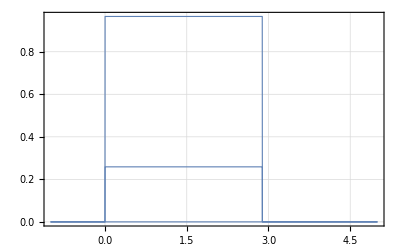

```mathematica
RadPlotOptions[];
Plot[radFld[final, "m", {5,y, 5}], {y, -1, 5}]
```

```mathematica
(* 2 segments of the Halbach array by hand *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
R = 10
mx1 = Cos[φ+dφ/2]
my1 =Sin[φ+dφ/2]
mz1 = 0

(* create first segment, place same shape at z=0, z=R *)
segment1 = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment1 = Append[segment1, {segment1[[1]][[1]], R}]

(* Iterate on the variables for the second segment *)
φ += dφ
mx2 = Cos[φ+dφ/2]
my2 =Sin[φ+dφ/2]
mz2 = 0

(* add new segments at z=0, z=R *)
segment2 = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment2 = Append[segment2, {segment2[[1]][[1]], R}]
Print["segment is now: ", segment2]

(* first attempt to create segments, then define group for segments *)
s1 = radObjMltExtPgn[segment1, {mx1, my1, mz1}]
s2 = radObjMltExtPgn[segment2, {mx2, my2, mz2}]
group = radObjCnt[{s1, s2}]


(* color the object *)
radObjDrwAtr[group, {0, 0.5, 0.8}]

(* plot + show the object *)
RadPlot3DOptions[];
s = radObjDrw[group];
Show[Graphics3D[s]]
```

0

π/6

10

(1+√3)/(2 √2)

(-1+√3)/(2 √2)

0

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0}}

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0},{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},10}}

π/6

1/(√2)

1/(√2)

0

{{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0}}

{{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0},{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},10}}

segment is now: {{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0},{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},10}}

6

8

9

9

-Graphics3D-

```mathematica
(* Plot the magnetic field's x-component *)
```

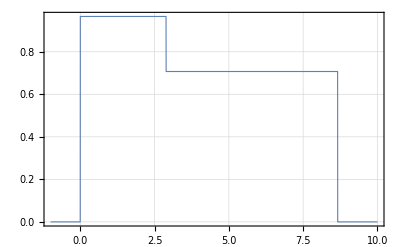

```mathematica
RadPlotOptions[];
Plot[radFld[group, "mx", {5,y, 5}], {y, -1, 10}]
```

```mathematica
(* Draw all 12 segments of the array, outward pointing magnetization *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
R = 25.4
halbach = radObjCnt[{}]

For[i=1, i< 13, i++,
(* set magnetization *)
mx = Cos[φ+dφ/2];
my =Sin[φ+dφ/2];
mz = 0;

(* create segment geometry *)
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, -R/2}};
segment = Append[segment, {segment[[1]][[1]], R/2}];
created = radObjMltExtPgn[segment, {mx, my, mz}];

(* iterate on variables *) 
φ += dφ;

(* add to group *)
radObjAddToCnt[halbach, {created}];
]

(* color the object *)
radObjDrwAtr[halbach, {0, 0.5, 0.8}];

(* plot + show the object *)
RadPlot3DOptions[];
g = radObjDrw[halbach];
Show[Graphics3D[g]]
```

0

π/6

25.4

10

-Graphics3D-

```mathematica
(* Create new Halbach array with spatially rotating magnetization *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
θ=π/12
dθ = π/2
(* outer radius *)
R = 25.4
halbach = radObjCnt[{}]

For[i=1, i< 13, i++,
(* set magnetization *)
mx = Cos[θ];
my =Sin[θ];
mz = 0;

Print["Magnetization angle for ", i," is: ", θ];

(* create segment geometry *)
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, -R/2}};
segment = Append[segment, {segment[[1]][[1]], R/2}];
created = radObjMltExtPgn[segment, {mx, my, mz}];

(* iterate on variables *) 
φ += dφ;
θ+=dφ + dθ;

(* add to group *)
radObjAddToCnt[halbach, {created}];
]

(* color the object *)
radObjDrwAtr[halbach, {0, 0.5, 0.8}];

(* plot + show the object *)
RadPlot3DOptions[];
g = radObjDrw[halbach];
Show[Graphics3D[g]]
```

0

π/6

π/12

π/2

25.4

35

Magnetization angle for 1 is: π/12

Magnetization angle for 2 is: (3 π)/4

Magnetization angle for 3 is: (17 π)/12

Magnetization angle for 4 is: (25 π)/12

Magnetization angle for 5 is: (11 π)/4

Magnetization angle for 6 is: (41 π)/12

Magnetization angle for 7 is: (49 π)/12

Magnetization angle for 8 is: (19 π)/4

Magnetization angle for 9 is: (65 π)/12

Magnetization angle for 10 is: (73 π)/12

Magnetization angle for 11 is: (27 π)/4

Magnetization angle for 12 is: (89 π)/12

-Graphics3D-

```mathematica
(* Plot the y-component of the magnetic field to demonstrate spatial rotation *)
```

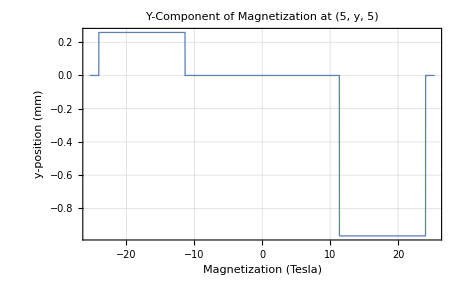

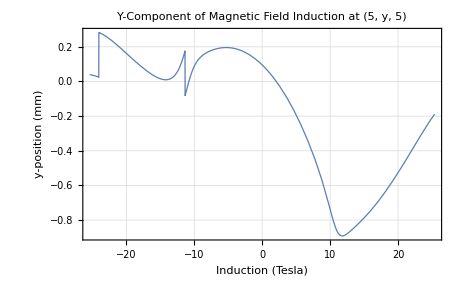

```mathematica
RadPlotOptions[];
Plot[radFld[halbach, "my", {5,y, 5}], {y, -R, R}, PlotLabel->"Y-Component of Magnetization at (5, y, 5)", AxesLabel->{"Magnetization (Tesla)", "y-position (mm)"}]
Plot[radFld[halbach, "By", {5,y, 5}], {y, -R, R}, PlotLabel->"Y-Component of Magnetic Field Induction at (5, y, 5)", AxesLabel->{"Induction (Tesla)", "y-position (mm)"}]
```

```mathematica
(* Plot the B-field *)
```

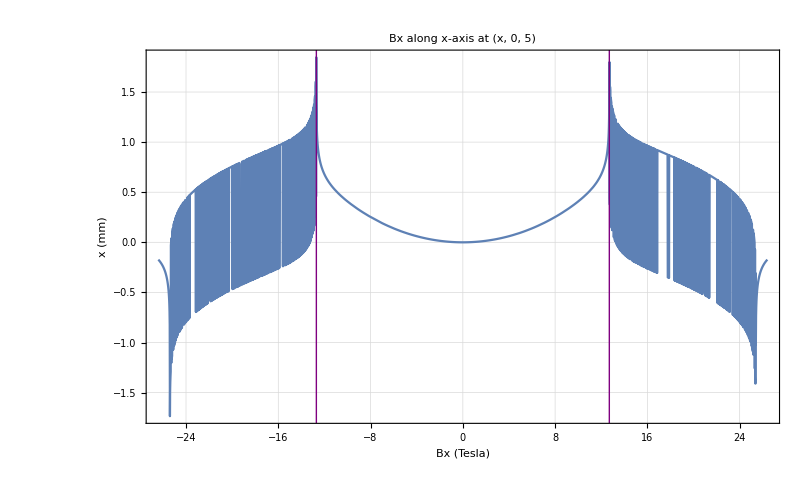

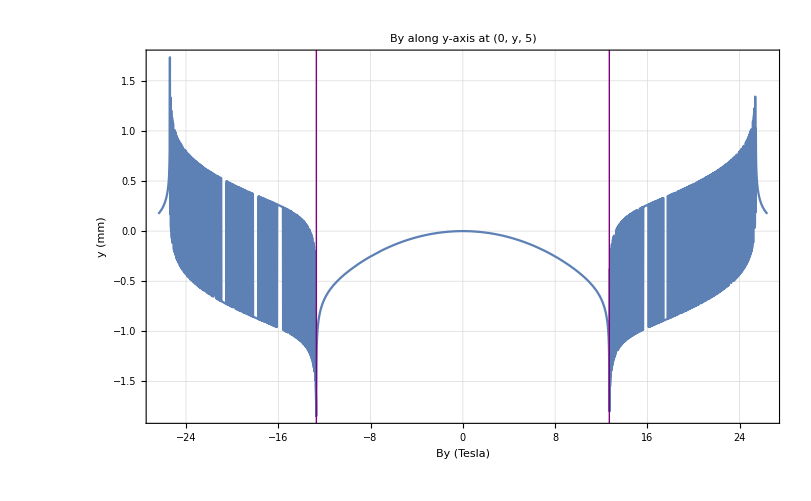

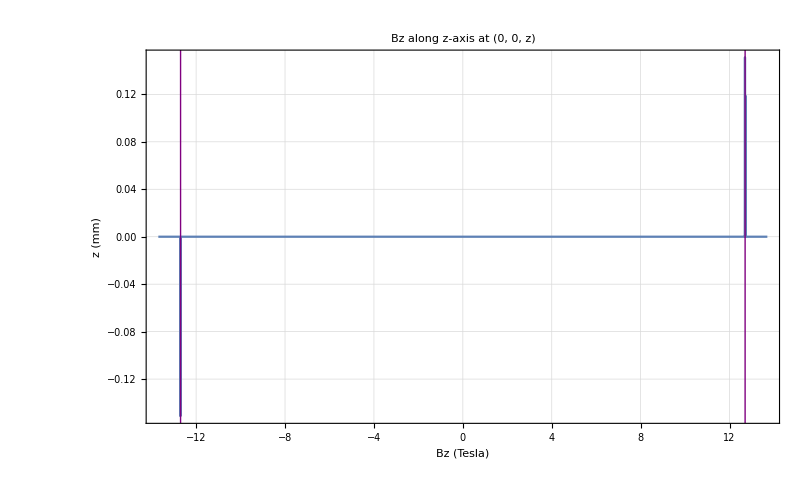

```mathematica
lineStyle={Thick,Purple};

(* draw lines at boundary of the inner radius *)
line1=Line[{{R/2,-10},{R/2,10}}];
line2=Line[{{-R/2,-10},{-R/2,10}}];

Plot[radFld[halbach, "Bx", {x, 0, 5}], {x, -R -1, R + 1}, PlotLabel->"Bx along x-axis at (x, 0, 5)", AxesLabel->{"Bx (Tesla)", "x (mm)"}, Epilog->{Directive[lineStyle], line1, line2}]

Plot[radFld[halbach, "By", {0, y, 5}], {y, -R -1, R + 1}, PlotLabel->"By along y-axis at (0, y, 5)", AxesLabel->{"By (Tesla)", "y (mm)"}, Epilog->{Directive[lineStyle], line1, line2}]

Plot[radFld[halbach, "Bz", {0, 0, z}], {z, -R/2  - 1, R/2 + 1}, PlotLabel->"Bz along z-axis at (0, 0, z)", AxesLabel->{"Bz (Tesla)", "z (mm)"},Epilog->{Directive[lineStyle], Line[{{-R/2, -10}, {-R/2, 10}}], Line[{{R/2, -10}, {R/2, 10}}]}]
```

```mathematica
(* Plot the norm of the B-field *)
```

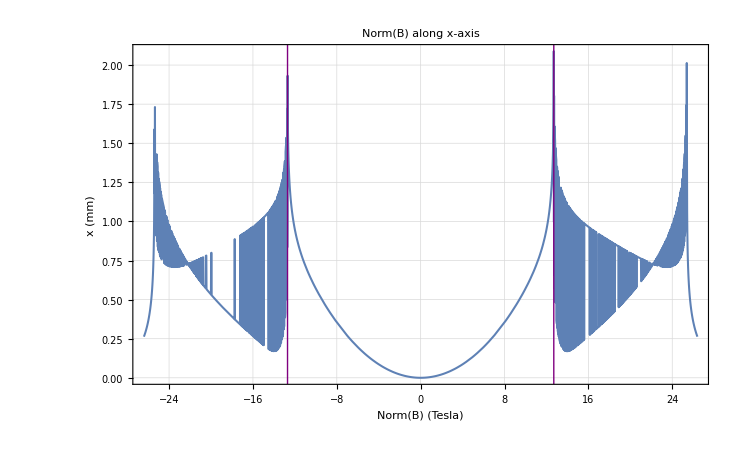

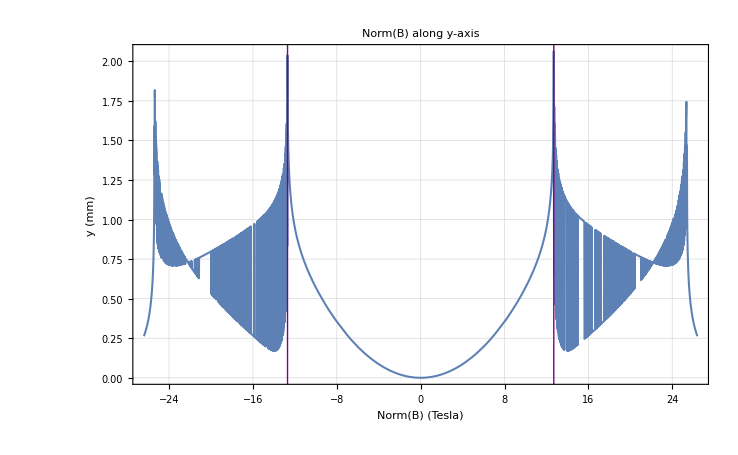

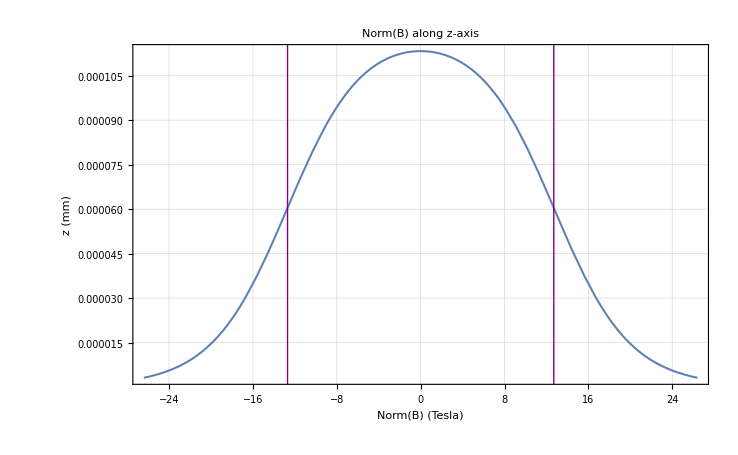

```mathematica
(* define norm function *)
norm [x_, y_, z_]:= Module[{bx, by, bz}, 
bx = radFld[halbach, "Bx", {x, y, z}];
by = radFld[halbach, "By", {x, y, z}];
bz = radFld[halbach, "Bz", {x, y, z}];
Return[Sqrt[bx^2 + by^2 + bz^2]];
]

lineStyle={Thick,Purple};
line1=Line[{{R/2,-10},{R/2,10}}];
line2=Line[{{-R/2,-10},{-R/2,10}}];

Plot[norm[x, 0, 5], {x, -R-1, R+1}, PlotLabel->"Norm(B) along x-axis", AxesLabel->{"Norm(B) (Tesla)", "x (mm)"},Epilog->{Directive[lineStyle],line1,line2}]

Plot[norm[0, y, 5], {y,-R-1, R+1}, PlotLabel->"Norm(B) along y-axis", AxesLabel->{"Norm(B) (Tesla)", "y (mm)"},Epilog->{Directive[lineStyle],line1,line2}]

Plot[norm[0.1, 0.1, z], {z, -R - 1, R+ 1}, PlotLabel->"Norm(B) along z-axis", AxesLabel->{"Norm(B) (Tesla)", "z (mm)"},Epilog->{Directive[lineStyle],Line[{{-R/2,-10},{-R/2,10}}],Line[{{R/2,-10},{R/2,10}}]}]
```

```mathematica
(* Make a matrix of the B-field values for use with Python, export to a .csv file *)
```

```mathematica
(* initialize variables *)
xStart = -R/2;
yStart = -R/2;
zStart = -R/2;
m=18;
bxMatrix = {};
byMatrix = {};
bzMatrix = {};
normbMatrix = {};
bMatrix = {};

(* iterate through points on x, y, z axes *)
For[i=1, i≤ m, i++,
bxMatrix=Append[bxMatrix, {}];
For[j=1, j≤ m, j++,
bxMatrix[[i]]=Append[bxMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bxMatrix[[i]][[j]]=Append[bxMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "Bx", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
byMatrix=Append[byMatrix, {}];
For[j=1, j≤ m, j++,
byMatrix[[i]]=Append[byMatrix[[i]], {}];
For[k=1,k≤ m, k++,
byMatrix[[i]][[j]]=Append[byMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "By", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
bzMatrix=Append[bzMatrix, {}];
For[j=1, j≤ m, j++,
bzMatrix[[i]]=Append[bzMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bzMatrix[[i]][[j]]=Append[bzMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "Bz", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
normbMatrix=Append[normbMatrix, {}];
For[j=1, j≤ m, j++,
normbMatrix[[i]]=Append[normbMatrix[[i]], {}];
For[k=1,k≤ m, k++,
normbMatrix[[i]][[j]]=Append[normbMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
norm[xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)]]
];
];
];

(* iterate through points on x, y, z axes *)
For[i=1, i≤ m, i++,
bMatrix=Append[bMatrix, {}];
For[j=1, j≤ m, j++,
bMatrix[[i]]=Append[bMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bMatrix[[i]][[j]]=Append[bMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "B", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

Print["bxMatrix: ", MatrixForm[bxMatrix]]
Print["byMatrix: ", MatrixForm[byMatrix]]
Print["bzMatrix: ", MatrixForm[bzMatrix]]
Print["normbMatrix: ", MatrixForm[normbMatrix]]
Print["bMatrix: ", MatrixForm[bMatrix]]

SetDirectory["/Users/andrewwinnicki/Desktop/Andrew/2019-2020/Doyle Lab/Modeling Magnetic Lens/magnetic_lens_monte_carlo/bmatrix"];
Export["bxMatrix.fits",bxMatrix];
Export["byMatrix.fits",byMatrix];
Export["bzMatrix.fits",bzMatrix];
Export["normbMatrix.fits",normbMatrix];
Export["bMatrix.fits",bMatrix];
```

bxMatrix: ((-0.458163
-0.376199
-0.315138
-0.276609
-0.253749
-0.240694
-0.233986
-0.23192
-0.233986
-0.240694
-0.253749
-0.276609
-0.315138
-0.376199
0.248943) | (-0.453443
-0.363956
-0.302213
-0.264942
-0.24304
-0.230507
-0.224045
-0.22205
-0.224045
-0.230507
-0.24304
-0.264942
-0.302213
-0.363956
0.253664) | (-0.433922
-0.311009
-0.252143
-0.21975
-0.200635
-0.189498
-0.183673
-0.181862
-0.183673
-0.189498
-0.200635
-0.21975
-0.252143
-0.311009
0.273185) | (0.965357
0.857792
0.890615
0.914015
0.929293
0.938655
0.943682
0.945263
0.943682
0.938655
0.929293
0.914015
0.890615
0.857792
-0.000568335) | (0.946412
0.86229
0.867918
0.883487
0.895598
0.903463
0.907792
0.909167
0.907792
0.903463
0.895598
0.883487
0.867918
0.86229
-0.0195136) | (0.905146
0.78677
0.791308
0.80537
0.816285
0.823348
0.827227
0.828458
0.827227
0.823348
0.816285
0.80537
0.791308
0.78677
-0.0607798) | (0.913165
0.782613
0.805623
0.823362
0.834694
0.841529
0.84517
0.846311
0.84517
0.841529
0.834694
0.823362
0.805623
0.782613
-0.0527609) | (2.69282
4.00967
4.37103
4.4952
3.45805
4.01595
4.01794
3.31412
4.34567
3.79335
3.80508
4.29264
4.24992
4.35341
1.63643) | (-0.10363
-0.0368488
0.000177676
0.0199384
0.0309819
0.0371706
0.0403319
0.0413041
0.0403319
0.0371706
0.0309819
0.0199384
0.000177676
-0.0368488
0.155189) | (-0.14902
-0.10912
-0.0819178
-0.0657582
-0.0563442
-0.0509822
-0.0482283
-0.0473804
-0.0482283
-0.0509822
-0.0563442
-0.0657582
-0.0819178
-0.10912
0.109799) | (-0.133523
-0.0688081
-0.0426765
-0.0294317
-0.0217343
-0.0172754
-0.0149607
-0.0142451
-0.0149607
-0.0172754
-0.0217343
-0.0294317
-0.0426765
-0.0688081
0.125296) | (-0.038557
0.137568
0.154881
0.16507
0.171397
0.17516
0.177129
0.177739
0.177129
0.17516
0.171397
0.16507
0.154881
0.137568
0.220262) | (-0.716636
-0.752634
-0.74834
-0.740129
-0.734248
-0.730705
-0.728875
-0.728316
-0.728875
-0.730705
-0.734248
-0.740129
-0.74834
-0.752634
-0.716636) | (-0.660843
-0.652643
-0.639811
-0.628807
-0.621744
-0.617774
-0.615827
-0.615248
-0.615827
-0.617774
-0.621744
-0.628807
-0.639811
-0.652643
-0.660843) | (-0.603122
-0.563366
-0.533971
-0.51619
-0.506517
-0.501594
-0.499332
-0.498683
-0.499332
-0.501594
-0.506517
-0.51619
-0.533971
-0.563366
-0.603122)
(-0.400484
-0.286322
-0.21095
-0.167073
-0.141681
-0.12723
-0.119798
-0.117507
-0.119798
-0.12723
-0.141681
-0.167073
-0.21095
-0.286322
0.306623) | (-0.40739
-0.302623
-0.22818
-0.183035
-0.156704
-0.141752
-0.134088
-0.131729
-0.134088
-0.141752
-0.156704
-0.183035
-0.22818
-0.302623
0.299717) | (-0.391171
-0.269513
-0.192829
-0.148712
-0.123194
-0.108674
-0.101209
-0.0989083
-0.101209
-0.108674
-0.123194
-0.148712
-0.192829
-0.269513
0.315936) | (-0.297388
-0.0758132
0.00282934
0.0436497
0.0671217
0.0805892
0.0875627
0.0897199
0.0875627
0.0805892
0.0671217
0.0436497
0.00282934
-0.0758132
0.409718) | (0.484096
0.800839
0.869438
0.905572
0.926649
0.938864
0.945228
0.947202
0.945228
0.938864
0.926649
0.905572
0.869438
0.800839
0.484096) | (0.376824
0.598927
0.663785
0.697017
0.716192
0.727241
0.732982
0.734761
0.732982
0.727241
0.716192
0.697017
0.663785
0.598927
0.376824) | (0.330582
0.511877
0.578769
0.610712
0.628302
0.638197
0.643277
0.644843
0.643277
0.638197
0.628302
0.610712
0.578769
0.511877
0.330582) | (0.261927
0.393792
0.453053
0.481372
0.496588
0.504997
0.50927
0.510581
0.50927
0.504997
0.496588
0.481372
0.453053
0.393792
0.261927) | (0.149522
0.209855
0.246878
0.267219
0.278624
0.285009
0.288264
0.289263
0.288264
0.285009
0.278624
0.267219
0.246878
0.209855
0.149522) | (0.0657016
0.0852533
0.101059
0.111871
0.118666
0.122679
0.124774
0.125423
0.124774
0.122679
0.118666
0.111871
0.101059
0.0852533
0.0657016) | (-0.0137067
-0.0369412
-0.0379723
-0.0351906
-0.03258
-0.0308095
-0.0298343
-0.0295267
-0.0298343
-0.0308095
-0.03258
-0.0351906
-0.0379723
-0.0369412
-0.0137067) | (-0.694396
-0.673247
-0.67929
-0.680436
-0.680445
-0.680295
-0.680194
-0.680163
-0.680194
-0.680295
-0.680445
-0.680436
-0.67929
-0.673247
-0.694396) | (-0.679848
-0.652133
-0.646804
-0.646371
-0.646842
-0.647402
-0.647798
-0.647938
-0.647798
-0.647402
-0.646842
-0.646371
-0.646804
-0.652133
-0.679848) | (-0.653703
-0.616055
-0.598252
-0.592914
-0.592086
-0.592504
-0.593012
-0.593213
-0.593012
-0.592504
-0.592086
-0.592914
-0.598252
-0.616055
-0.653703) | (-0.607565
-0.544329
-0.51276
-0.501815
-0.498958
-0.498735
-0.499085
-0.499264
-0.499085
-0.498735
-0.498958
-0.501815
-0.51276
-0.544329
-0.607565)
(-0.34465
-0.164542
-0.0877815
-0.0483294
-0.0255486
-0.0123846
-0.00553769
-0.00341584
-0.00553769
-0.0123846
-0.0255486
-0.0483294
-0.0877815
-0.164542
0.362456) | (-0.381257
-0.249598
-0.171104
-0.127156
-0.101843
-0.0874234
-0.0800049
-0.0777184
-0.0800049
-0.0874234
-0.101843
-0.127156
-0.171104
-0.249598
0.32585) | (-0.404217
-0.294701
-0.219531
-0.174797
-0.148767
-0.133958
-0.126356
-0.124016
-0.126356
-0.133958
-0.148767
-0.174797
-0.219531
-0.294701
0.302889) | (0.324345
0.453906
0.532398
0.576678
0.602165
0.616654
0.624098
0.62639
0.624098
0.616654
0.602165
0.576678
0.532398
0.453906
0.324345) | (0.33063
0.472562
0.550986
0.59326
0.617312
0.630967
0.637986
0.640149
0.637986
0.630967
0.617312
0.59326
0.550986
0.472562
0.33063) | (0.288263
0.405994
0.476221
0.514802
0.536717
0.549119
0.555483
0.557443
0.555483
0.549119
0.536717
0.514802
0.476221
0.405994
0.288263) | (0.238974
0.332184
0.391607
0.425035
0.443987
0.454652
0.460102
0.461777
0.460102
0.454652
0.443987
0.425035
0.391607
0.332184
0.238974) | (0.176628
0.242347
0.286653
0.312392
0.327095
0.335367
0.339588
0.340884
0.339588
0.335367
0.327095
0.312392
0.286653
0.242347
0.176628) | (0.0975561
0.130431
0.154498
0.169597
0.178619
0.183813
0.186491
0.187317
0.186491
0.183813
0.178619
0.169597
0.154498
0.130431
0.0975561) | (0.0093069
0.00638037
0.00756346
0.0104328
0.0129668
0.0146815
0.01563
0.0159302
0.01563
0.0146815
0.0129668
0.0104328
0.00756346
0.00638037
0.0093069) | (-0.102429
-0.163699
-0.187599
-0.196178
-0.199701
-0.201315
-0.202053
-0.20227
-0.202053
-0.201315
-0.199701
-0.196178
-0.187599
-0.163699
-0.102429) | (-0.23263
-0.39322
-0.428281
-0.443036
-0.450691
-0.454884
-0.457016
-0.457672
-0.457016
-0.454884
-0.450691
-0.443036
-0.428281
-0.39322
-0.23263) | (-0.656701
-0.550672
-0.562357
-0.575485
-0.584639
-0.59034
-0.593417
-0.594387
-0.593417
-0.59034
-0.584639
-0.575485
-0.562357
-0.550672
-0.656701) | (-0.669691
-0.596756
-0.588397
-0.597093
-0.606023
-0.612303
-0.61587
-0.617016
-0.61587
-0.612303
-0.606023
-0.597093
-0.588397
-0.596756
-0.669691) | (-0.626818
-0.517762
-0.502704
-0.509356
-0.517796
-0.524123
-0.527831
-0.52904
-0.527831
-0.524123
-0.517796
-0.509356
-0.502704
-0.517762
-0.626818)
(-0.0913629
-0.550367
-0.513789
-0.489146
-0.473317
-0.463731
-0.45864
-0.45705
-0.45864
-0.463731
-0.473317
-0.489146
-0.513789
-0.550367
-0.350182) | (-0.36665
-0.172126
-0.112783
-0.0808995
-0.061921
-0.0508349
-0.0450539
-0.0432621
-0.0450539
-0.0508349
-0.061921
-0.0808995
-0.112783
-0.172126
0.340457) | (0.232378
0.315669
0.371507
0.405797
0.426451
0.438451
0.444675
0.446599
0.444675
0.438451
0.426451
0.405797
0.371507
0.315669
0.232378) | (0.222051
0.294726
0.348921
0.383726
0.404886
0.417188
0.423565
0.425535
0.423565
0.417188
0.404886
0.383726
0.348921
0.294726
0.222051) | (0.217903
0.289772
0.342975
0.376964
0.39759
0.409579
0.415793
0.417713
0.415793
0.409579
0.39759
0.376964
0.342975
0.289772
0.217903) | (0.197238
0.261324
0.30948
0.340552
0.359465
0.370461
0.376159
0.377919
0.376159
0.370461
0.359465
0.340552
0.30948
0.261324
0.197238) | (0.161841
0.213222
0.25265
0.278525
0.294375
0.3036
0.308379
0.309854
0.308379
0.3036
0.294375
0.278525
0.25265
0.213222
0.161841) | (0.11264
0.14753
0.174808
0.193041
0.204324
0.210921
0.214344
0.215401
0.214344
0.210921
0.204324
0.193041
0.174808
0.14753
0.11264) | (0.0492299
0.0633669
0.074894
0.0830284
0.0882852
0.0914443
0.0931082
0.0936255
0.0931082
0.0914443
0.0882852
0.0830284
0.074894
0.0633669
0.0492299) | (-0.0280908
-0.0403464
-0.0482215
-0.0521202
-0.0539001
-0.0547159
-0.0550778
-0.0551818
-0.0550778
-0.0547159
-0.0539001
-0.0521202
-0.0482215
-0.0403464
-0.0280908) | (-0.120509
-0.16968
-0.200463
-0.216955
-0.225851
-0.230687
-0.233112
-0.233851
-0.233112
-0.230687
-0.225851
-0.216955
-0.200463
-0.16968
-0.120509) | (-0.222176
-0.324066
-0.375925
-0.40252
-0.417321
-0.425647
-0.429913
-0.431226
-0.429913
-0.425647
-0.417321
-0.40252
-0.375925
-0.324066
-0.222176) | (-0.324435
-0.505787
-0.562318
-0.593545
-0.612166
-0.623053
-0.628744
-0.630511
-0.628744
-0.623053
-0.612166
-0.593545
-0.562318
-0.505787
-0.324435) | (-0.763271
-0.678586
-0.722813
-0.755085
-0.775791
-0.788283
-0.794911
-0.796983
-0.794911
-0.788283
-0.775791
-0.755085
-0.722813
-0.678586
-0.763271) | (-0.482248
0.158386
0.105691
0.0712247
0.049231
0.0359062
0.0288034
0.0265779
0.0288034
0.0359062
0.049231
0.0712247
0.105691
0.158386
0.483678)
(0.00377857
-0.286732
-0.282759
-0.273494
-0.26628
-0.26166
-0.259161
-0.258376
-0.259161
-0.26166
-0.26628
-0.273494
-0.282759
-0.286732
-0.25504) | (0.0134358
-0.0321005
-0.0155931
-0.00155894
0.00795625
0.013802
0.016915
0.0178872
0.016915
0.013802
0.00795625
-0.00155894
-0.0155931
-0.0321005
0.0134358) | (0.102237
0.128689
0.152718
0.170312
0.181864
0.188866
0.192572
0.193726
0.192572
0.188866
0.181864
0.170312
0.152718
0.128689
0.102237) | (0.120396
0.154359
0.182378
0.202385
0.215416
0.223281
0.227433
0.228725
0.227433
0.223281
0.215416
0.202385
0.182378
0.154359
0.120396) | (0.126597
0.162639
0.192165
0.213125
0.226735
0.234938
0.239266
0.240612
0.239266
0.234938
0.226735
0.213125
0.192165
0.162639
0.126597) | (0.119622
0.153458
0.181296
0.201149
0.214076
0.221877
0.225995
0.227276
0.225995
0.221877
0.214076
0.201149
0.181296
0.153458
0.119622) | (0.0985052
0.126033
0.148855
0.165273
0.176022
0.182525
0.185961
0.187031
0.185961
0.182525
0.176022
0.165273
0.148855
0.126033
0.0985052) | (0.0633235
0.080787
0.0953694
0.105955
0.112935
0.117175
0.119421
0.12012
0.119421
0.117175
0.112935
0.105955
0.0953694
0.080787
0.0633235) | (0.0140666
0.0175187
0.0205593
0.0229354
0.0246056
0.0256658
0.0262415
0.0264229
0.0262415
0.0256658
0.0246056
0.0229354
0.0205593
0.0175187
0.0140666) | (-0.0492801
-0.0646618
-0.0767259
-0.0847545
-0.089663
-0.0924963
-0.0939533
-0.0944014
-0.0939533
-0.0924963
-0.089663
-0.0847545
-0.0767259
-0.0646618
-0.0492801) | (-0.126643
-0.167595
-0.198594
-0.218659
-0.230849
-0.237916
-0.24157
-0.242698
-0.24157
-0.237916
-0.230849
-0.218659
-0.198594
-0.167595
-0.126643) | (-0.217928
-0.295017
-0.348394
-0.380863
-0.400178
-0.41133
-0.4171
-0.418882
-0.4171
-0.41133
-0.400178
-0.380863
-0.348394
-0.295017
-0.217928) | (-0.330592
-0.467539
-0.545102
-0.588561
-0.613952
-0.628575
-0.636145
-0.638484
-0.636145
-0.628575
-0.613952
-0.588561
-0.545102
-0.467539
-0.330592) | (-0.483947
-0.73263
-0.830418
-0.882016
-0.911872
-0.929031
-0.937912
-0.940657
-0.937912
-0.929031
-0.911872
-0.882016
-0.830418
-0.73263
-0.483947) | (-0.463144
0.293794
0.189699
0.13347
0.101013
0.0824214
0.0728166
0.0698496
0.0728166
0.0824214
0.101013
0.13347
0.189699
0.293794
0.502782)
(0.0194826
-0.210259
-0.210942
-0.213271
-0.215014
-0.216134
-0.216751
-0.216948
-0.216751
-0.216134
-0.215014
-0.213271
-0.210942
-0.210259
-0.239336) | (-0.0658249
-0.117691
-0.126999
-0.129518
-0.130352
-0.130674
-0.130807
-0.130844
-0.130807
-0.130674
-0.130352
-0.129518
-0.126999
-0.117691
-0.0658249) | (-0.00940759
-0.021191
-0.0242177
-0.0235111
-0.0222234
-0.0212187
-0.020634
-0.0204456
-0.020634
-0.0212187
-0.0222234
-0.0235111
-0.0242177
-0.021191
-0.00940759) | (0.0280226
0.033287
0.0389587
0.0440543
0.0478508
0.0503114
0.0516567
0.0520813
0.0516567
0.0503114
0.0478508
0.0440543
0.0389587
0.033287
0.0280226) | (0.0492449
0.0617588
0.0726215
0.0809325
0.0866628
0.0902514
0.0921845
0.0927913
0.0921845
0.0902514
0.0866628
0.0809325
0.0726215
0.0617588
0.0492449) | (0.0562741
0.070881
0.0834105
0.0928654
0.0993221
0.103344
0.105505
0.106183
0.105505
0.103344
0.0993221
0.0928654
0.0834105
0.070881
0.0562741) | (0.0492392
0.0619574
0.0728926
0.0811707
0.0868386
0.0903752
0.0922771
0.0928737
0.0922771
0.0903752
0.0868386
0.0811707
0.0728926
0.0619574
0.0492392) | (0.0281359
0.0353521
0.0415756
0.0463076
0.0495604
0.0515957
0.052692
0.0530362
0.052692
0.0515957
0.0495604
0.0463076
0.0415756
0.0353521
0.0281359) | (-0.00703643
-0.00899332
-0.0106288
-0.0118122
-0.0125858
-0.0130512
-0.0132957
-0.0133716
-0.0132957
-0.0130512
-0.0125858
-0.0118122
-0.0106288
-0.00899332
-0.00703643) | (-0.0562839
-0.0715807
-0.084441
-0.0938672
-0.100135
-0.103966
-0.106001
-0.106636
-0.106001
-0.103966
-0.100135
-0.0938672
-0.084441
-0.0715807
-0.0562839) | (-0.119622
-0.153507
-0.181342
-0.201171
-0.214081
-0.221876
-0.225991
-0.227272
-0.225991
-0.221876
-0.214081
-0.201171
-0.181342
-0.153507
-0.119622) | (-0.197201
-0.256984
-0.303986
-0.335912
-0.356054
-0.368007
-0.374266
-0.376207
-0.374266
-0.368007
-0.356054
-0.335912
-0.303986
-0.256984
-0.197201) | (-0.288152
-0.383988
-0.45409
-0.498716
-0.525845
-0.541646
-0.549847
-0.552382
-0.549847
-0.541646
-0.525845
-0.498716
-0.45409
-0.383988
-0.288152) | (-0.376599
-0.512183
-0.604748
-0.660419
-0.693207
-0.712
-0.721682
-0.724667
-0.721682
-0.712
-0.693207
-0.660419
-0.604748
-0.512183
-0.376599) | (-0.421806
0.390901
0.286178
0.224103
0.188074
0.167606
0.157106
0.153875
0.157106
0.167606
0.188074
0.224103
0.286178
0.390901
0.54412)
(-0.284521
-0.237999
-0.255164
-0.272346
-0.284326
-0.291764
-0.295754
-0.297005
-0.295754
-0.291764
-0.284326
-0.272346
-0.255164
-0.237999
-0.284521) | (-0.149494
-0.214404
-0.246459
-0.265289
-0.276742
-0.283487
-0.287018
-0.288115
-0.287018
-0.283487
-0.276742
-0.265289
-0.246459
-0.214404
-0.149494) | (-0.0975567
-0.132055
-0.155733
-0.170203
-0.178887
-0.183935
-0.186556
-0.187367
-0.186556
-0.183935
-0.178887
-0.170203
-0.155733
-0.132055
-0.0975567) | (-0.0492411
-0.064587
-0.0764819
-0.0843969
-0.0893027
-0.0921805
-0.0936777
-0.0941409
-0.0936777
-0.0921805
-0.0893027
-0.0843969
-0.0764819
-0.064587
-0.0492411) | (-0.0140769
-0.0182881
-0.0216772
-0.0240062
-0.0254643
-0.0263173
-0.0267588
-0.026895
-0.0267588
-0.0263173
-0.0254643
-0.0240062
-0.0216772
-0.0182881
-0.0140769) | (0.00703151
0.00868438
0.0101608
0.0113425
0.0121945
0.0127463
0.0130499
0.0131461
0.0130499
0.0127463
0.0121945
0.0113425
0.0101608
0.00868438
0.00703151) | (0.0140657
0.0175407
0.0205809
0.0229438
0.0246035
0.0256591
0.0262337
0.0264149
0.0262337
0.0256591
0.0246035
0.0229438
0.0205809
0.0175407
0.0140657) | (0.00703277
0.00876566
0.0102832
0.0114645
0.0122954
0.0128246
0.0131128
0.0132037
0.0131128
0.0128246
0.0122954
0.0114645
0.0102832
0.00876566
0.00703277) | (-0.0140664
-0.017578
-0.0206385
-0.023003
-0.0246539
-0.025699
-0.0262662
-0.0264448
-0.0262662
-0.025699
-0.0246539
-0.023003
-0.0206385
-0.017578
-0.0140664) | (-0.0492365
-0.0617868
-0.0726346
-0.0809122
-0.0866236
-0.0902078
-0.0921422
-0.09275
-0.0921422
-0.0902078
-0.0866236
-0.0809122
-0.0726346
-0.0617868
-0.0492365) | (-0.0984864
-0.124591
-0.146774
-0.163294
-0.174443
-0.181332
-0.185016
-0.186168
-0.185016
-0.181332
-0.174443
-0.163294
-0.146774
-0.124591
-0.0984864) | (-0.161784
-0.207334
-0.24488
-0.271739
-0.289282
-0.299893
-0.305501
-0.307247
-0.305501
-0.299893
-0.289282
-0.271739
-0.24488
-0.207334
-0.161784) | (-0.238849
-0.312303
-0.369562
-0.40806
-0.432157
-0.446387
-0.453818
-0.45612
-0.453818
-0.446387
-0.432157
-0.40806
-0.369562
-0.312303
-0.238849) | (-0.330357
-0.446793
-0.527207
-0.57659
-0.606139
-0.62323
-0.632073
-0.634803
-0.632073
-0.62323
-0.606139
-0.57659
-0.527207
-0.446793
-0.330357) | (-0.429846
0.354956
0.254607
0.198643
0.166165
0.147574
0.137987
0.135029
0.137987
0.147574
0.166165
0.198643
0.254607
0.354956
0.536079)
(-1.70589
-2.91216
-4.10048
-3.46682
-3.46496
-3.88115
-3.39046
-3.05477
-3.4201
-4.2427
-3.99863
-3.89057
-3.90798
-3.59873
-2.11196) | (-0.261774
-0.364135
-0.424805
-0.460775
-0.482479
-0.495177
-0.501797
-0.503848
-0.501797
-0.495177
-0.482479
-0.460775
-0.424805
-0.364135
-0.261774) | (-0.176546
-0.23207
-0.274187
-0.302143
-0.319663
-0.330054
-0.335497
-0.337187
-0.335497
-0.330054
-0.319663
-0.302143
-0.274187
-0.23207
-0.176546) | (-0.112603
-0.144211
-0.170249
-0.188911
-0.201145
-0.208571
-0.212504
-0.21373
-0.212504
-0.208571
-0.201145
-0.188911
-0.170249
-0.144211
-0.112603) | (-0.0633111
-0.0799007
-0.0940674
-0.104694
-0.111913
-0.116396
-0.1188
-0.119553
-0.1188
-0.116396
-0.111913
-0.104694
-0.0940674
-0.0799007
-0.0633111) | (-0.0281334
-0.0351962
-0.0413378
-0.0460669
-0.0493584
-0.0514375
-0.0525641
-0.0529187
-0.0525641
-0.0514375
-0.0493584
-0.0460669
-0.0413378
-0.0351962
-0.0281334) | (-0.00703261
-0.00875655
-0.010269
-0.0114498
-0.0122828
-0.0128146
-0.0131046
-0.0131962
-0.0131046
-0.0128146
-0.0122828
-0.0114498
-0.010269
-0.00875655
-0.00703261) | (-0.120741
-0.0883883
0.441942
-0.0323524
0.32987
0.32987
-0.562682
-0.20046
0.209129
-0.153093
-0.0647048
0.056036
0.241481
0.056036
-0.385906) | (-0.00703261
-0.00875655
-0.010269
-0.0114498
-0.0122828
-0.0128146
-0.0131046
-0.0131962
-0.0131046
-0.0128146
-0.0122828
-0.0114498
-0.010269
-0.00875655
-0.00703261) | (-0.0281334
-0.0351962
-0.0413378
-0.0460669
-0.0493584
-0.0514375
-0.0525641
-0.0529187
-0.0525641
-0.0514375
-0.0493584
-0.0460669
-0.0413378
-0.0351962
-0.0281334) | (-0.0633111
-0.0799007
-0.0940674
-0.104694
-0.111913
-0.116396
-0.1188
-0.119553
-0.1188
-0.116396
-0.111913
-0.104694
-0.0940674
-0.0799007
-0.0633111) | (-0.112603
-0.144211
-0.170249
-0.188911
-0.201145
-0.208571
-0.212504
-0.21373
-0.212504
-0.208571
-0.201145
-0.188911
-0.170249
-0.144211
-0.112603) | (-0.176546
-0.23207
-0.274187
-0.302143
-0.319663
-0.330054
-0.335497
-0.337187
-0.335497
-0.330054
-0.319663
-0.302143
-0.274187
-0.23207
-0.176546) | (-0.261774
-0.364135
-0.424805
-0.460775
-0.482479
-0.495177
-0.501797
-0.503848
-0.501797
-0.495177
-0.482479
-0.460775
-0.424805
-0.364135
-0.261774) | (-1.70176
-3.0692
-3.14339
-3.5386
-3.36795
-3.53657
-3.6367
-3.65576
-3.60979
-3.11608
-4.08966
-3.89109
-3.4349
-3.82176
-0.93835)
(-0.429846
0.354956
0.254607
0.198643
0.166165
0.147574
0.137987
0.135029
0.137987
0.147574
0.166165
0.198643
0.254607
0.354956
0.536079) | (-0.330357
-0.446793
-0.527207
-0.57659
-0.606139
-0.62323
-0.632073
-0.634803
-0.632073
-0.62323
-0.606139
-0.57659
-0.527207
-0.446793
-0.330357) | (-0.238849
-0.312303
-0.369562
-0.40806
-0.432157
-0.446387
-0.453818
-0.45612
-0.453818
-0.446387
-0.432157
-0.40806
-0.369562
-0.312303
-0.238849) | (-0.161784
-0.207334
-0.24488
-0.271739
-0.289282
-0.299893
-0.305501
-0.307247
-0.305501
-0.299893
-0.289282
-0.271739
-0.24488
-0.207334
-0.161784) | (-0.0984864
-0.124591
-0.146774
-0.163294
-0.174443
-0.181332
-0.185016
-0.186168
-0.185016
-0.181332
-0.174443
-0.163294
-0.146774
-0.124591
-0.0984864) | (-0.0492365
-0.0617868
-0.0726346
-0.0809122
-0.0866236
-0.0902078
-0.0921422
-0.09275
-0.0921422
-0.0902078
-0.0866236
-0.0809122
-0.0726346
-0.0617868
-0.0492365) | (-0.0140664
-0.017578
-0.0206385
-0.023003
-0.0246539
-0.025699
-0.0262662
-0.0264448
-0.0262662
-0.025699
-0.0246539
-0.023003
-0.0206385
-0.017578
-0.0140664) | (0.00703277
0.00876566
0.0102832
0.0114645
0.0122954
0.0128246
0.0131128
0.0132037
0.0131128
0.0128246
0.0122954
0.0114645
0.0102832
0.00876566
0.00703277) | (0.0140657
0.0175407
0.0205809
0.0229438
0.0246035
0.0256591
0.0262337
0.0264149
0.0262337
0.0256591
0.0246035
0.0229438
0.0205809
0.0175407
0.0140657) | (0.00703151
0.00868438
0.0101608
0.0113425
0.0121945
0.0127463
0.0130499
0.0131461
0.0130499
0.0127463
0.0121945
0.0113425
0.0101608
0.00868438
0.00703151) | (-0.0140769
-0.0182881
-0.0216772
-0.0240062
-0.0254643
-0.0263173
-0.0267588
-0.026895
-0.0267588
-0.0263173
-0.0254643
-0.0240062
-0.0216772
-0.0182881
-0.0140769) | (-0.0492411
-0.064587
-0.0764819
-0.0843969
-0.0893027
-0.0921805
-0.0936777
-0.0941409
-0.0936777
-0.0921805
-0.0893027
-0.0843969
-0.0764819
-0.064587
-0.0492411) | (-0.0975567
-0.132055
-0.155733
-0.170203
-0.178887
-0.183935
-0.186556
-0.187367
-0.186556
-0.183935
-0.178887
-0.170203
-0.155733
-0.132055
-0.0975567) | (-0.149494
-0.214404
-0.246459
-0.265289
-0.276742
-0.283487
-0.287018
-0.288115
-0.287018
-0.283487
-0.276742
-0.265289
-0.246459
-0.214404
-0.149494) | (-0.0257016
-0.237999
-0.255164
-0.272346
-0.284326
-0.291764
-0.295754
-0.297005
-0.295754
-0.291764
-0.284326
-0.272346
-0.255164
-0.237999
-0.0257016)
(-0.421806
0.390901
0.286178
0.224103
0.188074
0.167606
0.157106
0.153875
0.157106
0.167606
0.188074
0.224103
0.286178
0.390901
-0.421806) | (-0.376599
-0.512183
-0.604748
-0.660419
-0.693207
-0.712
-0.721682
-0.724667
-0.721682
-0.712
-0.693207
-0.660419
-0.604748
-0.512183
-0.376599) | (-0.288152
-0.383988
-0.45409
-0.498716
-0.525845
-0.541646
-0.549847
-0.552382
-0.549847
-0.541646
-0.525845
-0.498716
-0.45409
-0.383988
-0.288152) | (-0.197201
-0.256984
-0.303986
-0.335912
-0.356054
-0.368007
-0.374266
-0.376207
-0.374266
-0.368007
-0.356054
-0.335912
-0.303986
-0.256984
-0.197201) | (-0.119622
-0.153507
-0.181342
-0.201171
-0.214081
-0.221876
-0.225991
-0.227272
-0.225991
-0.221876
-0.214081
-0.201171
-0.181342
-0.153507
-0.119622) | (-0.0562839
-0.0715807
-0.084441
-0.0938672
-0.100135
-0.103966
-0.106001
-0.106636
-0.106001
-0.103966
-0.100135
-0.0938672
-0.084441
-0.0715807
-0.0562839) | (-0.00703643
-0.00899332
-0.0106288
-0.0118122
-0.0125858
-0.0130512
-0.0132957
-0.0133716
-0.0132957
-0.0130512
-0.0125858
-0.0118122
-0.0106288
-0.00899332
-0.00703643) | (0.0281359
0.0353521
0.0415756
0.0463076
0.0495604
0.0515957
0.052692
0.0530362
0.052692
0.0515957
0.0495604
0.0463076
0.0415756
0.0353521
0.0281359) | (0.0492392
0.0619574
0.0728926
0.0811707
0.0868386
0.0903752
0.0922771
0.0928737
0.0922771
0.0903752
0.0868386
0.0811707
0.0728926
0.0619574
0.0492392) | (0.0562741
0.070881
0.0834105
0.0928654
0.0993221
0.103344
0.105505
0.106183
0.105505
0.103344
0.0993221
0.0928654
0.0834105
0.070881
0.0562741) | (0.0492449
0.0617588
0.0726215
0.0809325
0.0866628
0.0902514
0.0921845
0.0927913
0.0921845
0.0902514
0.0866628
0.0809325
0.0726215
0.0617588
0.0492449) | (0.0280226
0.033287
0.0389587
0.0440543
0.0478508
0.0503114
0.0516567
0.0520813
0.0516567
0.0503114
0.0478508
0.0440543
0.0389587
0.033287
0.0280226) | (-0.00940759
-0.021191
-0.0242177
-0.0235111
-0.0222234
-0.0212187
-0.020634
-0.0204456
-0.020634
-0.0212187
-0.0222234
-0.0235111
-0.0242177
-0.021191
-0.00940759) | (-0.0658249
-0.117691
-0.126999
-0.129518
-0.130352
-0.130674
-0.130807
-0.130844
-0.130807
-0.130674
-0.130352
-0.129518
-0.126999
-0.117691
-0.0658249) | (0.0194826
-0.210259
-0.210942
-0.213271
-0.215014
-0.216134
-0.216751
-0.216948
-0.216751
-0.216134
-0.215014
-0.213271
-0.210942
-0.210259
0.0194826)
(-0.463144
0.293794
0.189699
0.13347
0.101013
0.0824214
0.0728166
0.0698496
0.0728166
0.0824214
0.101013
0.13347
0.189699
0.293794
-0.463144) | (-0.483947
-0.73263
-0.830418
-0.882016
-0.911872
-0.929031
-0.937912
-0.940657
-0.937912
-0.929031
-0.911872
-0.882016
-0.830418
-0.73263
-0.483947) | (-0.330592
-0.467539
-0.545102
-0.588561
-0.613952
-0.628575
-0.636145
-0.638484
-0.636145
-0.628575
-0.613952
-0.588561
-0.545102
-0.467539
-0.330592) | (-0.217928
-0.295017
-0.348394
-0.380863
-0.400178
-0.41133
-0.4171
-0.418882
-0.4171
-0.41133
-0.400178
-0.380863
-0.348394
-0.295017
-0.217928) | (-0.126643
-0.167595
-0.198594
-0.218659
-0.230849
-0.237916
-0.24157
-0.242698
-0.24157
-0.237916
-0.230849
-0.218659
-0.198594
-0.167595
-0.126643) | (-0.0492801
-0.0646618
-0.0767259
-0.0847545
-0.089663
-0.0924963
-0.0939533
-0.0944014
-0.0939533
-0.0924963
-0.089663
-0.0847545
-0.0767259
-0.0646618
-0.0492801) | (0.0140666
0.0175187
0.0205593
0.0229354
0.0246056
0.0256658
0.0262415
0.0264229
0.0262415
0.0256658
0.0246056
0.0229354
0.0205593
0.0175187
0.0140666) | (0.0633235
0.080787
0.0953694
0.105955
0.112935
0.117175
0.119421
0.12012
0.119421
0.117175
0.112935
0.105955
0.0953694
0.080787
0.0633235) | (0.0985052
0.126033
0.148855
0.165273
0.176022
0.182525
0.185961
0.187031
0.185961
0.182525
0.176022
0.165273
0.148855
0.126033
0.0985052) | (0.119622
0.153458
0.181296
0.201149
0.214076
0.221877
0.225995
0.227276
0.225995
0.221877
0.214076
0.201149
0.181296
0.153458
0.119622) | (0.126597
0.162639
0.192165
0.213125
0.226735
0.234938
0.239266
0.240612
0.239266
0.234938
0.226735
0.213125
0.192165
0.162639
0.126597) | (0.120396
0.154359
0.182378
0.202385
0.215416
0.223281
0.227433
0.228725
0.227433
0.223281
0.215416
0.202385
0.182378
0.154359
0.120396) | (0.102237
0.128689
0.152718
0.170312
0.181864
0.188866
0.192572
0.193726
0.192572
0.188866
0.181864
0.170312
0.152718
0.128689
0.102237) | (0.0134358
-0.0321005
-0.0155931
-0.00155894
0.00795625
0.013802
0.016915
0.0178872
0.016915
0.013802
0.00795625
-0.00155894
-0.0155931
-0.0321005
0.0134358) | (0.00377857
-0.286732
-0.282759
-0.273494
-0.26628
-0.26166
-0.259161
-0.258376
-0.259161
-0.26166
-0.26628
-0.273494
-0.282759
-0.286732
0.00377857)
(-0.482248
0.158386
0.105691
0.0712247
0.049231
0.0359062
0.0288034
0.0265779
0.0288034
0.0359062
0.049231
0.0712247
0.105691
0.158386
-0.482248) | (-0.0561639
-0.678586
-0.722813
-0.755085
-0.775791
-0.788283
-0.794911
-0.796983
-0.794911
-0.788283
-0.775791
-0.755085
-0.722813
-0.678586
-0.763271) | (-0.324435
-0.505787
-0.562318
-0.593545
-0.612166
-0.623053
-0.628744
-0.630511
-0.628744
-0.623053
-0.612166
-0.593545
-0.562318
-0.505787
-0.324435) | (-0.222176
-0.324066
-0.375925
-0.40252
-0.417321
-0.425647
-0.429913
-0.431226
-0.429913
-0.425647
-0.417321
-0.40252
-0.375925
-0.324066
-0.222176) | (-0.120509
-0.16968
-0.200463
-0.216955
-0.225851
-0.230687
-0.233112
-0.233851
-0.233112
-0.230687
-0.225851
-0.216955
-0.200463
-0.16968
-0.120509) | (-0.0280908
-0.0403464
-0.0482215
-0.0521202
-0.0539001
-0.0547159
-0.0550778
-0.0551818
-0.0550778
-0.0547159
-0.0539001
-0.0521202
-0.0482215
-0.0403464
-0.0280908) | (0.0492299
0.0633669
0.074894
0.0830284
0.0882852
0.0914443
0.0931082
0.0936255
0.0931082
0.0914443
0.0882852
0.0830284
0.074894
0.0633669
0.0492299) | (0.11264
0.14753
0.174808
0.193041
0.204324
0.210921
0.214344
0.215401
0.214344
0.210921
0.204324
0.193041
0.174808
0.14753
0.11264) | (0.161841
0.213222
0.25265
0.278525
0.294375
0.3036
0.308379
0.309854
0.308379
0.3036
0.294375
0.278525
0.25265
0.213222
0.161841) | (0.197238
0.261324
0.30948
0.340552
0.359465
0.370461
0.376159
0.377919
0.376159
0.370461
0.359465
0.340552
0.30948
0.261324
0.197238) | (0.217903
0.289772
0.342975
0.376964
0.39759
0.409579
0.415793
0.417713
0.415793
0.409579
0.39759
0.376964
0.342975
0.289772
0.217903) | (0.222051
0.294726
0.348921
0.383726
0.404886
0.417188
0.423565
0.425535
0.423565
0.417188
0.404886
0.383726
0.348921
0.294726
0.222051) | (0.232378
0.315669
0.371507
0.405797
0.426451
0.438451
0.444675
0.446599
0.444675
0.438451
0.426451
0.405797
0.371507
0.315669
0.232378) | (-0.36665
-0.172126
-0.112783
-0.0808995
-0.061921
-0.0508349
-0.0450539
-0.0432621
-0.0450539
-0.0508349
-0.061921
-0.0808995
-0.112783
-0.172126
0.340457) | (-0.0913629
-0.550367
-0.513789
-0.489146
-0.473317
-0.463731
-0.45864
-0.45705
-0.45864
-0.463731
-0.473317
-0.489146
-0.513789
-0.550367
-0.0913628)
(0.0802883
-0.517762
-0.502704
-0.509356
-0.517796
-0.524123
-0.527831
-0.52904
-0.527831
-0.524123
-0.517796
-0.509356
-0.502704
-0.517762
-0.626818) | (0.0374163
-0.596756
-0.588397
-0.597093
-0.606023
-0.612303
-0.61587
-0.617016
-0.61587
-0.612303
-0.606023
-0.597093
-0.588397
-0.596756
-0.669691) | (0.0504062
-0.550672
-0.562357
-0.575485
-0.584639
-0.59034
-0.593417
-0.594387
-0.593417
-0.59034
-0.584639
-0.575485
-0.562357
-0.550672
-0.656701) | (-0.23263
-0.39322
-0.428281
-0.443036
-0.450691
-0.454884
-0.457016
-0.457672
-0.457016
-0.454884
-0.450691
-0.443036
-0.428281
-0.39322
-0.23263) | (-0.102429
-0.163699
-0.187599
-0.196178
-0.199701
-0.201315
-0.202053
-0.20227
-0.202053
-0.201315
-0.199701
-0.196178
-0.187599
-0.163699
-0.102429) | (0.0093069
0.00638037
0.00756346
0.0104328
0.0129668
0.0146815
0.01563
0.0159302
0.01563
0.0146815
0.0129668
0.0104328
0.00756346
0.00638037
0.0093069) | (0.0975561
0.130431
0.154498
0.169597
0.178619
0.183813
0.186491
0.187317
0.186491
0.183813
0.178619
0.169597
0.154498
0.130431
0.0975561) | (0.176628
0.242347
0.286653
0.312392
0.327095
0.335367
0.339588
0.340884
0.339588
0.335367
0.327095
0.312392
0.286653
0.242347
0.176628) | (0.238974
0.332184
0.391607
0.425035
0.443987
0.454652
0.460102
0.461777
0.460102
0.454652
0.443987
0.425035
0.391607
0.332184
0.238974) | (0.288263
0.405994
0.476221
0.514802
0.536717
0.549119
0.555483
0.557443
0.555483
0.549119
0.536717
0.514802
0.476221
0.405994
0.288263) | (0.33063
0.472562
0.550986
0.59326
0.617312
0.630967
0.637986
0.640149
0.637986
0.630967
0.617312
0.59326
0.550986
0.472562
0.33063) | (0.324345
0.453906
0.532398
0.576678
0.602165
0.616654
0.624098
0.62639
0.624098
0.616654
0.602165
0.576678
0.532398
0.453906
0.324345) | (-0.404217
-0.294701
-0.219531
-0.174797
-0.148767
-0.133958
-0.126356
-0.124016
-0.126356
-0.133958
-0.148767
-0.174797
-0.219531
-0.294701
0.302889) | (-0.381257
-0.249598
-0.171104
-0.127156
-0.101843
-0.0874234
-0.0800049
-0.0777184
-0.0800049
-0.0874234
-0.101843
-0.127156
-0.171104
-0.249598
0.32585) | (-0.34465
-0.164542
-0.0877815
-0.0483294
-0.0255486
-0.0123846
-0.00553769
-0.00341584
-0.00553769
-0.0123846
-0.0255486
-0.0483294
-0.0877815
-0.164542
0.362456)
(0.0995417
-0.544329
-0.51276
-0.501815
-0.498958
-0.498735
-0.499085
-0.499264
-0.499085
-0.498735
-0.498958
-0.501815
-0.51276
-0.544329
-0.607565) | (0.0534037
-0.616055
-0.598252
-0.592914
-0.592086
-0.592504
-0.593012
-0.593213
-0.593012
-0.592504
-0.592086
-0.592914
-0.598252
-0.616055
0.0534037) | (0.0272589
-0.652133
-0.646804
-0.646371
-0.646842
-0.647402
-0.647798
-0.647938
-0.647798
-0.647402
-0.646842
-0.646371
-0.646804
-0.652133
0.0272589) | (0.0127108
-0.673247
-0.67929
-0.680436
-0.680445
-0.680295
-0.680194
-0.680163
-0.680194
-0.680295
-0.680445
-0.680436
-0.67929
-0.673247
-0.694396) | (-0.0137067
-0.0369412
-0.0379723
-0.0351906
-0.03258
-0.0308095
-0.0298343
-0.0295267
-0.0298343
-0.0308095
-0.03258
-0.0351906
-0.0379723
-0.0369412
-0.0137067) | (0.0657016
0.0852533
0.101059
0.111871
0.118666
0.122679
0.124774
0.125423
0.124774
0.122679
0.118666
0.111871
0.101059
0.0852533
0.0657016) | (0.149522
0.209855
0.246878
0.267219
0.278624
0.285009
0.288264
0.289263
0.288264
0.285009
0.278624
0.267219
0.246878
0.209855
0.149522) | (0.261927
0.393792
0.453053
0.481372
0.496588
0.504997
0.50927
0.510581
0.50927
0.504997
0.496588
0.481372
0.453053
0.393792
0.261927) | (0.330582
0.511877
0.578769
0.610712
0.628302
0.638197
0.643277
0.644843
0.643277
0.638197
0.628302
0.610712
0.578769
0.511877
0.330582) | (0.376824
0.598927
0.663785
0.697017
0.716192
0.727241
0.732982
0.734761
0.732982
0.727241
0.716192
0.697017
0.663785
0.598927
0.376824) | (0.484096
0.800839
0.869438
0.905572
0.926649
0.938864
0.945228
0.947202
0.945228
0.938864
0.926649
0.905572
0.869438
0.800839
0.484096) | (-0.297388
-0.0758132
0.00282934
0.0436497
0.0671217
0.0805892
0.0875627
0.0897199
0.0875627
0.0805892
0.0671217
0.0436497
0.00282934
-0.0758132
0.409718) | (-0.391171
-0.269513
-0.192829
-0.148712
-0.123194
-0.108674
-0.101209
-0.0989083
-0.101209
-0.108674
-0.123194
-0.148712
-0.192829
-0.269513
0.315936) | (-0.40739
-0.302623
-0.22818
-0.183035
-0.156704
-0.141752
-0.134088
-0.131729
-0.134088
-0.141752
-0.156704
-0.183035
-0.22818
-0.302623
0.299717) | (-0.400484
-0.286322
-0.21095
-0.167073
-0.141681
-0.12723
-0.119798
-0.117507
-0.119798
-0.12723
-0.141681
-0.167073
-0.21095
-0.286322
0.306623)
(0.103985
-0.563366
-0.533971
-0.51619
-0.506517
-0.501594
-0.499332
-0.498683
-0.499332
-0.501594
-0.506517
-0.51619
-0.533971
-0.563366
-0.603122) | (0.0462637
-0.652643
-0.639811
-0.628807
-0.621744
-0.617774
-0.615827
-0.615248
-0.615827
-0.617774
-0.621744
-0.628807
-0.639811
-0.652643
-0.660843) | (-0.00952957
-0.752634
-0.74834
-0.740129
-0.734248
-0.730705
-0.728875
-0.728316
-0.728875
-0.730705
-0.734248
-0.740129
-0.74834
-0.752634
-0.00952957) | (-0.038557
0.137568
0.154881
0.16507
0.171397
0.17516
0.177129
0.177739
0.177129
0.17516
0.171397
0.16507
0.154881
0.137568
0.220262) | (-0.133523
-0.0688081
-0.0426765
-0.0294317
-0.0217343
-0.0172754
-0.0149607
-0.0142451
-0.0149607
-0.0172754
-0.0217343
-0.0294317
-0.0426765
-0.0688081
0.125296) | (-0.14902
-0.10912
-0.0819178
-0.0657582
-0.0563442
-0.0509822
-0.0482283
-0.0473804
-0.0482283
-0.0509822
-0.0563442
-0.0657582
-0.0819178
-0.10912
0.109799) | (-0.10363
-0.0368488
0.000177676
0.0199384
0.0309819
0.0371706
0.0403319
0.0413041
0.0403319
0.0371706
0.0309819
0.0199384
0.000177676
-0.0368488
0.155189) | (2.06562
4.08506
4.20397
3.31379
4.39654
4.46788
4.5586
3.32551
4.25453
4.27481
4.44442
3.77843
4.11393
4.12501
1.59714) | (-0.0527609
0.782613
0.805623
0.823362
0.834694
0.841529
0.84517
0.846311
0.84517
0.841529
0.834694
0.823362
0.805623
0.782613
-0.0527609) | (-0.0607798
0.78677
0.791308
0.80537
0.816285
0.823348
0.827227
0.828458
0.827227
0.823348
0.816285
0.80537
0.791308
0.78677
-0.0607798) | (-0.0195136
0.86229
0.867918
0.883487
0.895598
0.903463
0.907792
0.909167
0.907792
0.903463
0.895598
0.883487
0.867918
0.86229
-0.0195136) | (-0.000568346
0.857792
0.890615
0.914015
0.929293
0.938655
0.943682
0.945263
0.943682
0.938655
0.929293
0.914015
0.890615
0.857792
-0.000568336) | (-0.433922
-0.311009
-0.252143
-0.21975
-0.200635
-0.189498
-0.183673
-0.181862
-0.183673
-0.189498
-0.200635
-0.21975
-0.252143
-0.311009
0.273185) | (-0.453443
-0.363956
-0.302213
-0.264942
-0.24304
-0.230507
-0.224045
-0.22205
-0.224045
-0.230507
-0.24304
-0.264942
-0.302213
-0.363956
0.253664) | (-0.458163
-0.376199
-0.315138
-0.276609
-0.253749
-0.240694
-0.233986
-0.23192
-0.233986
-0.240694
-0.253749
-0.276609
-0.315138
-0.376199
0.248943))

byMatrix: ((0.458163
0.376199
0.315138
0.276609
0.253749
0.240694
0.233986
0.23192
0.233986
0.240694
0.253749
0.276609
0.315138
0.376199
-0.248943) | (0.400484
0.286322
0.21095
0.167073
0.141681
0.12723
0.119798
0.117507
0.119798
0.12723
0.141681
0.167073
0.21095
0.286322
-0.306623) | (0.34465
0.164542
0.0877815
0.0483294
0.0255486
0.0123846
0.00553769
0.00341584
0.00553769
0.0123846
0.0255486
0.0483294
0.0877815
0.164542
-0.362456) | (0.350182
0.550367
0.513789
0.489146
0.473317
0.463731
0.45864
0.45705
0.45864
0.463731
0.473317
0.489146
0.513789
0.550367
0.0913628) | (0.25504
0.286732
0.282759
0.273494
0.26628
0.26166
0.259161
0.258376
0.259161
0.26166
0.26628
0.273494
0.282759
0.286732
-0.00377857) | (0.239336
0.210259
0.210942
0.213271
0.215014
0.216134
0.216751
0.216948
0.216751
0.216134
0.215014
0.213271
0.210942
0.210259
-0.0194826) | (0.284521
0.237999
0.255164
0.272346
0.284326
0.291764
0.295754
0.297005
0.295754
0.291764
0.284326
0.272346
0.255164
0.237999
0.0257016) | (2.13707
3.75891
4.08277
3.78132
3.45457
3.37603
3.54029
3.53788
4.00254
3.39054
3.69618
3.33232
4.04406
3.37568
1.71573) | (-0.536079
-0.354956
-0.254607
-0.198643
-0.166165
-0.147574
-0.137987
-0.135029
-0.137987
-0.147574
-0.166165
-0.198643
-0.254607
-0.354956
0.429846) | (-0.54412
-0.390901
-0.286178
-0.224103
-0.188074
-0.167606
-0.157106
-0.153875
-0.157106
-0.167606
-0.188074
-0.224103
-0.286178
-0.390901
0.421806) | (-0.502782
-0.293794
-0.189699
-0.13347
-0.101013
-0.0824214
-0.0728166
-0.0698496
-0.0728166
-0.0824214
-0.101013
-0.13347
-0.189699
-0.293794
0.463144) | (-0.483678
-0.158386
-0.105691
-0.0712247
-0.049231
-0.0359062
-0.0288034
-0.0265779
-0.0288034
-0.0359062
-0.049231
-0.0712247
-0.105691
-0.158386
0.482248) | (0.626818
0.517762
0.502704
0.509356
0.517796
0.524123
0.527831
0.52904
0.527831
0.524123
0.517796
0.509356
0.502704
0.517762
0.626818) | (0.607565
0.544329
0.51276
0.501815
0.498958
0.498735
0.499085
0.499264
0.499085
0.498735
0.498958
0.501815
0.51276
0.544329
0.607565) | (0.603122
0.563366
0.533971
0.51619
0.506517
0.501594
0.499332
0.498683
0.499332
0.501594
0.506517
0.51619
0.533971
0.563366
0.603122)
(0.453443
0.363956
0.302213
0.264942
0.24304
0.230507
0.224045
0.22205
0.224045
0.230507
0.24304
0.264942
0.302213
0.363956
-0.253664) | (0.40739
0.302623
0.22818
0.183035
0.156704
0.141752
0.134088
0.131729
0.134088
0.141752
0.156704
0.183035
0.22818
0.302623
-0.299717) | (0.381257
0.249598
0.171104
0.127156
0.101843
0.0874234
0.0800049
0.0777184
0.0800049
0.0874234
0.101843
0.127156
0.171104
0.249598
-0.32585) | (0.36665
0.172126
0.112783
0.0808995
0.061921
0.0508349
0.0450539
0.0432621
0.0450539
0.0508349
0.061921
0.0808995
0.112783
0.172126
-0.340457) | (-0.0134358
0.0321005
0.0155931
0.00155894
-0.00795625
-0.013802
-0.016915
-0.0178872
-0.016915
-0.013802
-0.00795625
0.00155894
0.0155931
0.0321005
-0.0134358) | (0.0658249
0.117691
0.126999
0.129518
0.130352
0.130674
0.130807
0.130844
0.130807
0.130674
0.130352
0.129518
0.126999
0.117691
0.0658249) | (0.149494
0.214404
0.246459
0.265289
0.276742
0.283487
0.287018
0.288115
0.287018
0.283487
0.276742
0.265289
0.246459
0.214404
0.149494) | (0.261774
0.364135
0.424805
0.460775
0.482479
0.495177
0.501797
0.503848
0.501797
0.495177
0.482479
0.460775
0.424805
0.364135
0.261774) | (0.330357
0.446793
0.527207
0.57659
0.606139
0.62323
0.632073
0.634803
0.632073
0.62323
0.606139
0.57659
0.527207
0.446793
0.330357) | (0.376599
0.512183
0.604748
0.660419
0.693207
0.712
0.721682
0.724667
0.721682
0.712
0.693207
0.660419
0.604748
0.512183
0.376599) | (0.483947
0.73263
0.830418
0.882016
0.911872
0.929031
0.937912
0.940657
0.937912
0.929031
0.911872
0.882016
0.830418
0.73263
0.483947) | (0.763271
0.678586
0.722813
0.755085
0.775791
0.788283
0.794911
0.796983
0.794911
0.788283
0.775791
0.755085
0.722813
0.678586
0.763271) | (0.669691
0.596756
0.588397
0.597093
0.606023
0.612303
0.61587
0.617016
0.61587
0.612303
0.606023
0.597093
0.588397
0.596756
0.669691) | (0.653703
0.616055
0.598252
0.592914
0.592086
0.592504
0.593012
0.593213
0.593012
0.592504
0.592086
0.592914
0.598252
0.616055
0.653703) | (0.660843
0.652643
0.639811
0.628807
0.621744
0.617774
0.615827
0.615248
0.615827
0.617774
0.621744
0.628807
0.639811
0.652643
0.660843)
(0.433922
0.311009
0.252143
0.21975
0.200635
0.189498
0.183673
0.181862
0.183673
0.189498
0.200635
0.21975
0.252143
0.311009
-0.273185) | (0.391171
0.269513
0.192829
0.148712
0.123194
0.108674
0.101209
0.0989083
0.101209
0.108674
0.123194
0.148712
0.192829
0.269513
-0.315936) | (0.404217
0.294701
0.219531
0.174797
0.148767
0.133958
0.126356
0.124016
0.126356
0.133958
0.148767
0.174797
0.219531
0.294701
-0.302889) | (-0.232378
-0.315669
-0.371507
-0.405797
-0.426451
-0.438451
-0.444675
-0.446599
-0.444675
-0.438451
-0.426451
-0.405797
-0.371507
-0.315669
-0.232378) | (-0.102237
-0.128689
-0.152718
-0.170312
-0.181864
-0.188866
-0.192572
-0.193726
-0.192572
-0.188866
-0.181864
-0.170312
-0.152718
-0.128689
-0.102237) | (0.00940759
0.021191
0.0242177
0.0235111
0.0222234
0.0212187
0.020634
0.0204456
0.020634
0.0212187
0.0222234
0.0235111
0.0242177
0.021191
0.00940759) | (0.0975567
0.132055
0.155733
0.170203
0.178887
0.183935
0.186556
0.187367
0.186556
0.183935
0.178887
0.170203
0.155733
0.132055
0.0975567) | (0.176546
0.23207
0.274187
0.302143
0.319663
0.330054
0.335497
0.337187
0.335497
0.330054
0.319663
0.302143
0.274187
0.23207
0.176546) | (0.238849
0.312303
0.369562
0.40806
0.432157
0.446387
0.453818
0.45612
0.453818
0.446387
0.432157
0.40806
0.369562
0.312303
0.238849) | (0.288152
0.383988
0.45409
0.498716
0.525845
0.541646
0.549847
0.552382
0.549847
0.541646
0.525845
0.498716
0.45409
0.383988
0.288152) | (0.330592
0.467539
0.545102
0.588561
0.613952
0.628575
0.636145
0.638484
0.636145
0.628575
0.613952
0.588561
0.545102
0.467539
0.330592) | (0.324435
0.505787
0.562318
0.593545
0.612166
0.623053
0.628744
0.630511
0.628744
0.623053
0.612166
0.593545
0.562318
0.505787
0.324435) | (0.656701
0.550672
0.562357
0.575485
0.584639
0.59034
0.593417
0.594387
0.593417
0.59034
0.584639
0.575485
0.562357
0.550672
0.656701) | (0.679848
0.652133
0.646804
0.646371
0.646842
0.647402
0.647798
0.647938
0.647798
0.647402
0.646842
0.646371
0.646804
0.652133
0.679848) | (0.716636
0.752634
0.74834
0.740129
0.734248
0.730705
0.728875
0.728316
0.728875
0.730705
0.734248
0.740129
0.74834
0.752634
0.716636)
(-0.965357
-0.857792
-0.890615
-0.914015
-0.929293
-0.938655
-0.943682
-0.945263
-0.943682
-0.938655
-0.929293
-0.914015
-0.890615
-0.857792
-0.965357) | (0.297388
0.0758132
-0.00282934
-0.0436497
-0.0671217
-0.0805892
-0.0875627
-0.0897199
-0.0875627
-0.0805892
-0.0671217
-0.0436497
-0.00282934
0.0758132
-0.409718) | (-0.324345
-0.453906
-0.532398
-0.576678
-0.602165
-0.616654
-0.624098
-0.62639
-0.624098
-0.616654
-0.602165
-0.576678
-0.532398
-0.453906
-0.324345) | (-0.222051
-0.294726
-0.348921
-0.383726
-0.404886
-0.417188
-0.423565
-0.425535
-0.423565
-0.417188
-0.404886
-0.383726
-0.348921
-0.294726
-0.222051) | (-0.120396
-0.154359
-0.182378
-0.202385
-0.215416
-0.223281
-0.227433
-0.228725
-0.227433
-0.223281
-0.215416
-0.202385
-0.182378
-0.154359
-0.120396) | (-0.0280226
-0.033287
-0.0389587
-0.0440543
-0.0478508
-0.0503114
-0.0516567
-0.0520813
-0.0516567
-0.0503114
-0.0478508
-0.0440543
-0.0389587
-0.033287
-0.0280226) | (0.0492411
0.064587
0.0764819
0.0843969
0.0893027
0.0921805
0.0936777
0.0941409
0.0936777
0.0921805
0.0893027
0.0843969
0.0764819
0.064587
0.0492411) | (0.112603
0.144211
0.170249
0.188911
0.201145
0.208571
0.212504
0.21373
0.212504
0.208571
0.201145
0.188911
0.170249
0.144211
0.112603) | (0.161784
0.207334
0.24488
0.271739
0.289282
0.299893
0.305501
0.307247
0.305501
0.299893
0.289282
0.271739
0.24488
0.207334
0.161784) | (0.197201
0.256984
0.303986
0.335912
0.356054
0.368007
0.374266
0.376207
0.374266
0.368007
0.356054
0.335912
0.303986
0.256984
0.197201) | (0.217928
0.295017
0.348394
0.380863
0.400178
0.41133
0.4171
0.418882
0.4171
0.41133
0.400178
0.380863
0.348394
0.295017
0.217928) | (0.222176
0.324066
0.375925
0.40252
0.417321
0.425647
0.429913
0.431226
0.429913
0.425647
0.417321
0.40252
0.375925
0.324066
0.222176) | (0.23263
0.39322
0.428281
0.443036
0.450691
0.454884
0.457016
0.457672
0.457016
0.454884
0.450691
0.443036
0.428281
0.39322
0.23263) | (0.694396
0.673247
0.67929
0.680436
0.680445
0.680295
0.680194
0.680163
0.680194
0.680295
0.680445
0.680436
0.67929
0.673247
0.694396) | (-0.220262
-0.137568
-0.154881
-0.16507
-0.171397
-0.17516
-0.177129
-0.177739
-0.177129
-0.17516
-0.171397
-0.16507
-0.154881
-0.137568
0.038557)
(-0.946412
-0.86229
-0.867918
-0.883487
-0.895598
-0.903463
-0.907792
-0.909167
-0.907792
-0.903463
-0.895598
-0.883487
-0.867918
-0.86229
-0.946412) | (-0.484096
-0.800839
-0.869438
-0.905572
-0.926649
-0.938864
-0.945228
-0.947202
-0.945228
-0.938864
-0.926649
-0.905572
-0.869438
-0.800839
-0.484096) | (-0.33063
-0.472562
-0.550986
-0.59326
-0.617312
-0.630967
-0.637986
-0.640149
-0.637986
-0.630967
-0.617312
-0.59326
-0.550986
-0.472562
-0.33063) | (-0.217903
-0.289772
-0.342975
-0.376964
-0.39759
-0.409579
-0.415793
-0.417713
-0.415793
-0.409579
-0.39759
-0.376964
-0.342975
-0.289772
-0.217903) | (-0.126597
-0.162639
-0.192165
-0.213125
-0.226735
-0.234938
-0.239266
-0.240612
-0.239266
-0.234938
-0.226735
-0.213125
-0.192165
-0.162639
-0.126597) | (-0.0492449
-0.0617588
-0.0726215
-0.0809325
-0.0866628
-0.0902514
-0.0921845
-0.0927913
-0.0921845
-0.0902514
-0.0866628
-0.0809325
-0.0726215
-0.0617588
-0.0492449) | (0.0140769
0.0182881
0.0216772
0.0240062
0.0254643
0.0263173
0.0267588
0.026895
0.0267588
0.0263173
0.0254643
0.0240062
0.0216772
0.0182881
0.0140769) | (0.0633111
0.0799007
0.0940674
0.104694
0.111913
0.116396
0.1188
0.119553
0.1188
0.116396
0.111913
0.104694
0.0940674
0.0799007
0.0633111) | (0.0984864
0.124591
0.146774
0.163294
0.174443
0.181332
0.185016
0.186168
0.185016
0.181332
0.174443
0.163294
0.146774
0.124591
0.0984864) | (0.119622
0.153507
0.181342
0.201171
0.214081
0.221876
0.225991
0.227272
0.225991
0.221876
0.214081
0.201171
0.181342
0.153507
0.119622) | (0.126643
0.167595
0.198594
0.218659
0.230849
0.237916
0.24157
0.242698
0.24157
0.237916
0.230849
0.218659
0.198594
0.167595
0.126643) | (0.120509
0.16968
0.200463
0.216955
0.225851
0.230687
0.233112
0.233851
0.233112
0.230687
0.225851
0.216955
0.200463
0.16968
0.120509) | (0.102429
0.163699
0.187599
0.196178
0.199701
0.201315
0.202053
0.20227
0.202053
0.201315
0.199701
0.196178
0.187599
0.163699
0.102429) | (0.0137067
0.0369412
0.0379723
0.0351906
0.03258
0.0308095
0.0298343
0.0295267
0.0298343
0.0308095
0.03258
0.0351906
0.0379723
0.0369412
0.0137067) | (-0.125296
0.0688081
0.0426765
0.0294317
0.0217343
0.0172754
0.0149607
0.0142451
0.0149607
0.0172754
0.0217343
0.0294317
0.0426765
0.0688081
0.133523)
(0.0607798
-0.78677
-0.791308
-0.80537
-0.816285
-0.823348
-0.827227
-0.828458
-0.827227
-0.823348
-0.816285
-0.80537
-0.791308
-0.78677
-0.905146) | (-0.376824
-0.598927
-0.663785
-0.697017
-0.716192
-0.727241
-0.732982
-0.734761
-0.732982
-0.727241
-0.716192
-0.697017
-0.663785
-0.598927
-0.376824) | (-0.288263
-0.405994
-0.476221
-0.514802
-0.536717
-0.549119
-0.555483
-0.557443
-0.555483
-0.549119
-0.536717
-0.514802
-0.476221
-0.405994
-0.288263) | (-0.197238
-0.261324
-0.30948
-0.340552
-0.359465
-0.370461
-0.376159
-0.377919
-0.376159
-0.370461
-0.359465
-0.340552
-0.30948
-0.261324
-0.197238) | (-0.119622
-0.153458
-0.181296
-0.201149
-0.214076
-0.221877
-0.225995
-0.227276
-0.225995
-0.221877
-0.214076
-0.201149
-0.181296
-0.153458
-0.119622) | (-0.0562741
-0.070881
-0.0834105
-0.0928654
-0.0993221
-0.103344
-0.105505
-0.106183
-0.105505
-0.103344
-0.0993221
-0.0928654
-0.0834105
-0.070881
-0.0562741) | (-0.00703151
-0.00868438
-0.0101608
-0.0113425
-0.0121945
-0.0127463
-0.0130499
-0.0131461
-0.0130499
-0.0127463
-0.0121945
-0.0113425
-0.0101608
-0.00868438
-0.00703151) | (0.0281334
0.0351962
0.0413378
0.0460669
0.0493584
0.0514375
0.0525641
0.0529187
0.0525641
0.0514375
0.0493584
0.0460669
0.0413378
0.0351962
0.0281334) | (0.0492365
0.0617868
0.0726346
0.0809122
0.0866236
0.0902078
0.0921422
0.09275
0.0921422
0.0902078
0.0866236
0.0809122
0.0726346
0.0617868
0.0492365) | (0.0562839
0.0715807
0.084441
0.0938672
0.100135
0.103966
0.106001
0.106636
0.106001
0.103966
0.100135
0.0938672
0.084441
0.0715807
0.0562839) | (0.0492801
0.0646618
0.0767259
0.0847545
0.089663
0.0924963
0.0939533
0.0944014
0.0939533
0.0924963
0.089663
0.0847545
0.0767259
0.0646618
0.0492801) | (0.0280908
0.0403464
0.0482215
0.0521202
0.0539001
0.0547159
0.0550778
0.0551818
0.0550778
0.0547159
0.0539001
0.0521202
0.0482215
0.0403464
0.0280908) | (-0.0093069
-0.00638037
-0.00756346
-0.0104328
-0.0129668
-0.0146815
-0.01563
-0.0159302
-0.01563
-0.0146815
-0.0129668
-0.0104328
-0.00756346
-0.00638037
-0.0093069) | (-0.0657016
-0.0852533
-0.101059
-0.111871
-0.118666
-0.122679
-0.124774
-0.125423
-0.124774
-0.122679
-0.118666
-0.111871
-0.101059
-0.0852533
-0.0657016) | (-0.109799
0.10912
0.0819178
0.0657582
0.0563442
0.0509822
0.0482283
0.0473804
0.0482283
0.0509822
0.0563442
0.0657582
0.0819178
0.10912
0.14902)
(0.0527609
-0.782613
-0.805623
-0.823362
-0.834694
-0.841529
-0.84517
-0.846311
-0.84517
-0.841529
-0.834694
-0.823362
-0.805623
-0.782613
-0.913165) | (-0.330582
-0.511877
-0.578769
-0.610712
-0.628302
-0.638197
-0.643277
-0.644843
-0.643277
-0.638197
-0.628302
-0.610712
-0.578769
-0.511877
-0.330582) | (-0.238974
-0.332184
-0.391607
-0.425035
-0.443987
-0.454652
-0.460102
-0.461777
-0.460102
-0.454652
-0.443987
-0.425035
-0.391607
-0.332184
-0.238974) | (-0.161841
-0.213222
-0.25265
-0.278525
-0.294375
-0.3036
-0.308379
-0.309854
-0.308379
-0.3036
-0.294375
-0.278525
-0.25265
-0.213222
-0.161841) | (-0.0985052
-0.126033
-0.148855
-0.165273
-0.176022
-0.182525
-0.185961
-0.187031
-0.185961
-0.182525
-0.176022
-0.165273
-0.148855
-0.126033
-0.0985052) | (-0.0492392
-0.0619574
-0.0728926
-0.0811707
-0.0868386
-0.0903752
-0.0922771
-0.0928737
-0.0922771
-0.0903752
-0.0868386
-0.0811707
-0.0728926
-0.0619574
-0.0492392) | (-0.0140657
-0.0175407
-0.0205809
-0.0229438
-0.0246035
-0.0256591
-0.0262337
-0.0264149
-0.0262337
-0.0256591
-0.0246035
-0.0229438
-0.0205809
-0.0175407
-0.0140657) | (0.00703261
0.00875655
0.010269
0.0114498
0.0122828
0.0128146
0.0131046
0.0131962
0.0131046
0.0128146
0.0122828
0.0114498
0.010269
0.00875655
0.00703261) | (0.0140664
0.017578
0.0206385
0.023003
0.0246539
0.025699
0.0262662
0.0264448
0.0262662
0.025699
0.0246539
0.023003
0.0206385
0.017578
0.0140664) | (0.00703643
0.00899332
0.0106288
0.0118122
0.0125858
0.0130512
0.0132957
0.0133716
0.0132957
0.0130512
0.0125858
0.0118122
0.0106288
0.00899332
0.00703643) | (-0.0140666
-0.0175187
-0.0205593
-0.0229354
-0.0246056
-0.0256658
-0.0262415
-0.0264229
-0.0262415
-0.0256658
-0.0246056
-0.0229354
-0.0205593
-0.0175187
-0.0140666) | (-0.0492299
-0.0633669
-0.074894
-0.0830284
-0.0882852
-0.0914443
-0.0931082
-0.0936255
-0.0931082
-0.0914443
-0.0882852
-0.0830284
-0.074894
-0.0633669
-0.0492299) | (-0.0975561
-0.130431
-0.154498
-0.169597
-0.178619
-0.183813
-0.186491
-0.187317
-0.186491
-0.183813
-0.178619
-0.169597
-0.154498
-0.130431
-0.0975561) | (-0.149522
-0.209855
-0.246878
-0.267219
-0.278624
-0.285009
-0.288264
-0.289263
-0.288264
-0.285009
-0.278624
-0.267219
-0.246878
-0.209855
-0.149522) | (-0.155189
0.0368488
-0.000177676
-0.0199384
-0.0309819
-0.0371706
-0.0403319
-0.0413041
-0.0403319
-0.0371706
-0.0309819
-0.0199384
-0.000177676
0.0368488
0.10363)
(-1.68816
-3.75747
-4.00651
-4.06216
-3.94689
-4.33899
-4.41993
-4.4843
-4.387
-3.34618
-4.3022
-4.35677
-4.21216
-3.32373
-1.64239) | (-0.261927
-0.393792
-0.453053
-0.481372
-0.496588
-0.504997
-0.50927
-0.510581
-0.50927
-0.504997
-0.496588
-0.481372
-0.453053
-0.393792
-0.261927) | (-0.176628
-0.242347
-0.286653
-0.312392
-0.327095
-0.335367
-0.339588
-0.340884
-0.339588
-0.335367
-0.327095
-0.312392
-0.286653
-0.242347
-0.176628) | (-0.11264
-0.14753
-0.174808
-0.193041
-0.204324
-0.210921
-0.214344
-0.215401
-0.214344
-0.210921
-0.204324
-0.193041
-0.174808
-0.14753
-0.11264) | (-0.0633235
-0.080787
-0.0953694
-0.105955
-0.112935
-0.117175
-0.119421
-0.12012
-0.119421
-0.117175
-0.112935
-0.105955
-0.0953694
-0.080787
-0.0633235) | (-0.0281359
-0.0353521
-0.0415756
-0.0463076
-0.0495604
-0.0515957
-0.052692
-0.0530362
-0.052692
-0.0515957
-0.0495604
-0.0463076
-0.0415756
-0.0353521
-0.0281359) | (-0.00703277
-0.00876566
-0.0102832
-0.0114645
-0.0122954
-0.0128246
-0.0131128
-0.0132037
-0.0131128
-0.0128246
-0.0122954
-0.0114645
-0.0102832
-0.00876566
-0.00703277) | (-0.0883883
0.265165
0.0323524
2.38876×10^-11
0.185445
1.34346×10^-11
0.0323524
0.120741
0.185445
0.176777
-7.76307×10^-12
-0.362222
-0.273834
-0.153093
-0.153093) | (-0.00703277
-0.00876566
-0.0102832
-0.0114645
-0.0122954
-0.0128246
-0.0131128
-0.0132037
-0.0131128
-0.0128246
-0.0122954
-0.0114645
-0.0102832
-0.00876566
-0.00703277) | (-0.0281359
-0.0353521
-0.0415756
-0.0463076
-0.0495604
-0.0515957
-0.052692
-0.0530362
-0.052692
-0.0515957
-0.0495604
-0.0463076
-0.0415756
-0.0353521
-0.0281359) | (-0.0633235
-0.080787
-0.0953694
-0.105955
-0.112935
-0.117175
-0.119421
-0.12012
-0.119421
-0.117175
-0.112935
-0.105955
-0.0953694
-0.080787
-0.0633235) | (-0.11264
-0.14753
-0.174808
-0.193041
-0.204324
-0.210921
-0.214344
-0.215401
-0.214344
-0.210921
-0.204324
-0.193041
-0.174808
-0.14753
-0.11264) | (-0.176628
-0.242347
-0.286653
-0.312392
-0.327095
-0.335367
-0.339588
-0.340884
-0.339588
-0.335367
-0.327095
-0.312392
-0.286653
-0.242347
-0.176628) | (-0.261927
-0.393792
-0.453053
-0.481372
-0.496588
-0.504997
-0.50927
-0.510581
-0.50927
-0.504997
-0.496588
-0.481372
-0.453053
-0.393792
-0.261927) | (-1.60704
-3.94693
-4.0723
-4.3634
-4.33068
-4.32225
-4.26001
-4.09862
-4.31393
-4.1925
-3.52022
-4.40049
-4.2849
-3.44734
-1.85914)
(-0.155189
0.0368488
-0.000177676
-0.0199384
-0.0309819
-0.0371706
-0.0403319
-0.0413041
-0.0403319
-0.0371706
-0.0309819
-0.0199384
-0.000177676
0.0368488
0.10363) | (-0.149522
-0.209855
-0.246878
-0.267219
-0.278624
-0.285009
-0.288264
-0.289263
-0.288264
-0.285009
-0.278624
-0.267219
-0.246878
-0.209855
-0.149522) | (-0.0975561
-0.130431
-0.154498
-0.169597
-0.178619
-0.183813
-0.186491
-0.187317
-0.186491
-0.183813
-0.178619
-0.169597
-0.154498
-0.130431
-0.0975561) | (-0.0492299
-0.0633669
-0.074894
-0.0830284
-0.0882852
-0.0914443
-0.0931082
-0.0936255
-0.0931082
-0.0914443
-0.0882852
-0.0830284
-0.074894
-0.0633669
-0.0492299) | (-0.0140666
-0.0175187
-0.0205593
-0.0229354
-0.0246056
-0.0256658
-0.0262415
-0.0264229
-0.0262415
-0.0256658
-0.0246056
-0.0229354
-0.0205593
-0.0175187
-0.0140666) | (0.00703643
0.00899332
0.0106288
0.0118122
0.0125858
0.0130512
0.0132957
0.0133716
0.0132957
0.0130512
0.0125858
0.0118122
0.0106288
0.00899332
0.00703643) | (0.0140664
0.017578
0.0206385
0.023003
0.0246539
0.025699
0.0262662
0.0264448
0.0262662
0.025699
0.0246539
0.023003
0.0206385
0.017578
0.0140664) | (0.00703261
0.00875655
0.010269
0.0114498
0.0122828
0.0128146
0.0131046
0.0131962
0.0131046
0.0128146
0.0122828
0.0114498
0.010269
0.00875655
0.00703261) | (-0.0140657
-0.0175407
-0.0205809
-0.0229438
-0.0246035
-0.0256591
-0.0262337
-0.0264149
-0.0262337
-0.0256591
-0.0246035
-0.0229438
-0.0205809
-0.0175407
-0.0140657) | (-0.0492392
-0.0619574
-0.0728926
-0.0811707
-0.0868386
-0.0903752
-0.0922771
-0.0928737
-0.0922771
-0.0903752
-0.0868386
-0.0811707
-0.0728926
-0.0619574
-0.0492392) | (-0.0985052
-0.126033
-0.148855
-0.165273
-0.176022
-0.182525
-0.185961
-0.187031
-0.185961
-0.182525
-0.176022
-0.165273
-0.148855
-0.126033
-0.0985052) | (-0.161841
-0.213222
-0.25265
-0.278525
-0.294375
-0.3036
-0.308379
-0.309854
-0.308379
-0.3036
-0.294375
-0.278525
-0.25265
-0.213222
-0.161841) | (-0.238974
-0.332184
-0.391607
-0.425035
-0.443987
-0.454652
-0.460102
-0.461777
-0.460102
-0.454652
-0.443987
-0.425035
-0.391607
-0.332184
-0.238974) | (-0.330582
-0.511877
-0.578769
-0.610712
-0.628302
-0.638197
-0.643277
-0.644843
-0.643277
-0.638197
-0.628302
-0.610712
-0.578769
-0.511877
-0.330582) | (0.0527609
-0.782613
-0.805623
-0.823362
-0.834694
-0.841529
-0.84517
-0.846311
-0.84517
-0.841529
-0.834694
-0.823362
-0.805623
-0.782613
0.0527609)
(-0.109799
0.10912
0.0819178
0.0657582
0.0563442
0.0509822
0.0482283
0.0473804
0.0482283
0.0509822
0.0563442
0.0657582
0.0819178
0.10912
0.14902) | (-0.0657016
-0.0852533
-0.101059
-0.111871
-0.118666
-0.122679
-0.124774
-0.125423
-0.124774
-0.122679
-0.118666
-0.111871
-0.101059
-0.0852533
-0.0657016) | (-0.0093069
-0.00638037
-0.00756346
-0.0104328
-0.0129668
-0.0146815
-0.01563
-0.0159302
-0.01563
-0.0146815
-0.0129668
-0.0104328
-0.00756346
-0.00638037
-0.0093069) | (0.0280908
0.0403464
0.0482215
0.0521202
0.0539001
0.0547159
0.0550778
0.0551818
0.0550778
0.0547159
0.0539001
0.0521202
0.0482215
0.0403464
0.0280908) | (0.0492801
0.0646618
0.0767259
0.0847545
0.089663
0.0924963
0.0939533
0.0944014
0.0939533
0.0924963
0.089663
0.0847545
0.0767259
0.0646618
0.0492801) | (0.0562839
0.0715807
0.084441
0.0938672
0.100135
0.103966
0.106001
0.106636
0.106001
0.103966
0.100135
0.0938672
0.084441
0.0715807
0.0562839) | (0.0492365
0.0617868
0.0726346
0.0809122
0.0866236
0.0902078
0.0921422
0.09275
0.0921422
0.0902078
0.0866236
0.0809122
0.0726346
0.0617868
0.0492365) | (0.0281334
0.0351962
0.0413378
0.0460669
0.0493584
0.0514375
0.0525641
0.0529187
0.0525641
0.0514375
0.0493584
0.0460669
0.0413378
0.0351962
0.0281334) | (-0.00703151
-0.00868438
-0.0101608
-0.0113425
-0.0121945
-0.0127463
-0.0130499
-0.0131461
-0.0130499
-0.0127463
-0.0121945
-0.0113425
-0.0101608
-0.00868438
-0.00703151) | (-0.0562741
-0.070881
-0.0834105
-0.0928654
-0.0993221
-0.103344
-0.105505
-0.106183
-0.105505
-0.103344
-0.0993221
-0.0928654
-0.0834105
-0.070881
-0.0562741) | (-0.119622
-0.153458
-0.181296
-0.201149
-0.214076
-0.221877
-0.225995
-0.227276
-0.225995
-0.221877
-0.214076
-0.201149
-0.181296
-0.153458
-0.119622) | (-0.197238
-0.261324
-0.30948
-0.340552
-0.359465
-0.370461
-0.376159
-0.377919
-0.376159
-0.370461
-0.359465
-0.340552
-0.30948
-0.261324
-0.197238) | (-0.288263
-0.405994
-0.476221
-0.514802
-0.536717
-0.549119
-0.555483
-0.557443
-0.555483
-0.549119
-0.536717
-0.514802
-0.476221
-0.405994
-0.288263) | (-0.376824
-0.598927
-0.663785
-0.697017
-0.716192
-0.727241
-0.732982
-0.734761
-0.732982
-0.727241
-0.716192
-0.697017
-0.663785
-0.598927
-0.376824) | (0.0607798
-0.78677
-0.791308
-0.80537
-0.816285
-0.823348
-0.827227
-0.828458
-0.827227
-0.823348
-0.816285
-0.80537
-0.791308
-0.78677
0.0607798)
(-0.125296
0.0688081
0.0426765
0.0294317
0.0217343
0.0172754
0.0149607
0.0142451
0.0149607
0.0172754
0.0217343
0.0294317
0.0426765
0.0688081
0.133523) | (0.0137067
0.0369412
0.0379723
0.0351906
0.03258
0.0308095
0.0298343
0.0295267
0.0298343
0.0308095
0.03258
0.0351906
0.0379723
0.0369412
0.0137067) | (0.102429
0.163699
0.187599
0.196178
0.199701
0.201315
0.202053
0.20227
0.202053
0.201315
0.199701
0.196178
0.187599
0.163699
0.102429) | (0.120509
0.16968
0.200463
0.216955
0.225851
0.230687
0.233112
0.233851
0.233112
0.230687
0.225851
0.216955
0.200463
0.16968
0.120509) | (0.126643
0.167595
0.198594
0.218659
0.230849
0.237916
0.24157
0.242698
0.24157
0.237916
0.230849
0.218659
0.198594
0.167595
0.126643) | (0.119622
0.153507
0.181342
0.201171
0.214081
0.221876
0.225991
0.227272
0.225991
0.221876
0.214081
0.201171
0.181342
0.153507
0.119622) | (0.0984864
0.124591
0.146774
0.163294
0.174443
0.181332
0.185016
0.186168
0.185016
0.181332
0.174443
0.163294
0.146774
0.124591
0.0984864) | (0.0633111
0.0799007
0.0940674
0.104694
0.111913
0.116396
0.1188
0.119553
0.1188
0.116396
0.111913
0.104694
0.0940674
0.0799007
0.0633111) | (0.0140769
0.0182881
0.0216772
0.0240062
0.0254643
0.0263173
0.0267588
0.026895
0.0267588
0.0263173
0.0254643
0.0240062
0.0216772
0.0182881
0.0140769) | (-0.0492449
-0.0617588
-0.0726215
-0.0809325
-0.0866628
-0.0902514
-0.0921845
-0.0927913
-0.0921845
-0.0902514
-0.0866628
-0.0809325
-0.0726215
-0.0617588
-0.0492449) | (-0.126597
-0.162639
-0.192165
-0.213125
-0.226735
-0.234938
-0.239266
-0.240612
-0.239266
-0.234938
-0.226735
-0.213125
-0.192165
-0.162639
-0.126597) | (-0.217903
-0.289772
-0.342975
-0.376964
-0.39759
-0.409579
-0.415793
-0.417713
-0.415793
-0.409579
-0.39759
-0.376964
-0.342975
-0.289772
-0.217903) | (-0.33063
-0.472562
-0.550986
-0.59326
-0.617312
-0.630967
-0.637986
-0.640149
-0.637986
-0.630967
-0.617312
-0.59326
-0.550986
-0.472562
-0.33063) | (-0.484096
-0.800839
-0.869438
-0.905572
-0.926649
-0.938864
-0.945228
-0.947202
-0.945228
-0.938864
-0.926649
-0.905572
-0.869438
-0.800839
-0.484096) | (0.0195136
-0.86229
-0.867918
-0.883487
-0.895598
-0.903463
-0.907792
-0.909167
-0.907792
-0.903463
-0.895598
-0.883487
-0.867918
-0.86229
0.0195136)
(-0.220262
-0.137568
-0.154881
-0.16507
-0.171397
-0.17516
-0.177129
-0.177739
-0.177129
-0.17516
-0.171397
-0.16507
-0.154881
-0.137568
-0.220262) | (-0.0127108
0.673247
0.67929
0.680436
0.680445
0.680295
0.680194
0.680163
0.680194
0.680295
0.680445
0.680436
0.67929
0.673247
0.694396) | (0.23263
0.39322
0.428281
0.443036
0.450691
0.454884
0.457016
0.457672
0.457016
0.454884
0.450691
0.443036
0.428281
0.39322
0.23263) | (0.222176
0.324066
0.375925
0.40252
0.417321
0.425647
0.429913
0.431226
0.429913
0.425647
0.417321
0.40252
0.375925
0.324066
0.222176) | (0.217928
0.295017
0.348394
0.380863
0.400178
0.41133
0.4171
0.418882
0.4171
0.41133
0.400178
0.380863
0.348394
0.295017
0.217928) | (0.197201
0.256984
0.303986
0.335912
0.356054
0.368007
0.374266
0.376207
0.374266
0.368007
0.356054
0.335912
0.303986
0.256984
0.197201) | (0.161784
0.207334
0.24488
0.271739
0.289282
0.299893
0.305501
0.307247
0.305501
0.299893
0.289282
0.271739
0.24488
0.207334
0.161784) | (0.112603
0.144211
0.170249
0.188911
0.201145
0.208571
0.212504
0.21373
0.212504
0.208571
0.201145
0.188911
0.170249
0.144211
0.112603) | (0.0492411
0.064587
0.0764819
0.0843969
0.0893027
0.0921805
0.0936777
0.0941409
0.0936777
0.0921805
0.0893027
0.0843969
0.0764819
0.064587
0.0492411) | (-0.0280226
-0.033287
-0.0389587
-0.0440543
-0.0478508
-0.0503114
-0.0516567
-0.0520813
-0.0516567
-0.0503114
-0.0478508
-0.0440543
-0.0389587
-0.033287
-0.0280226) | (-0.120396
-0.154359
-0.182378
-0.202385
-0.215416
-0.223281
-0.227433
-0.228725
-0.227433
-0.223281
-0.215416
-0.202385
-0.182378
-0.154359
-0.120396) | (-0.222051
-0.294726
-0.348921
-0.383726
-0.404886
-0.417188
-0.423565
-0.425535
-0.423565
-0.417188
-0.404886
-0.383726
-0.348921
-0.294726
-0.222051) | (-0.324345
-0.453906
-0.532398
-0.576678
-0.602165
-0.616654
-0.624098
-0.62639
-0.624098
-0.616654
-0.602165
-0.576678
-0.532398
-0.453906
-0.324345) | (0.297388
0.0758132
-0.00282934
-0.0436497
-0.0671217
-0.0805892
-0.0875627
-0.0897199
-0.0875627
-0.0805892
-0.0671217
-0.0436497
-0.00282934
0.0758132
-0.409718) | (0.000568346
-0.857792
-0.890615
-0.914015
-0.929293
-0.938655
-0.943682
-0.945263
-0.943682
-0.938655
-0.929293
-0.914015
-0.890615
-0.857792
0.000568338)
(0.00952957
0.752634
0.74834
0.740129
0.734248
0.730705
0.728875
0.728316
0.728875
0.730705
0.734248
0.740129
0.74834
0.752634
0.716636) | (-0.0272589
0.652133
0.646804
0.646371
0.646842
0.647402
0.647798
0.647938
0.647798
0.647402
0.646842
0.646371
0.646804
0.652133
-0.0272589) | (-0.0504062
0.550672
0.562357
0.575485
0.584639
0.59034
0.593417
0.594387
0.593417
0.59034
0.584639
0.575485
0.562357
0.550672
-0.0504062) | (0.324435
0.505787
0.562318
0.593545
0.612166
0.623053
0.628744
0.630511
0.628744
0.623053
0.612166
0.593545
0.562318
0.505787
0.324435) | (0.330592
0.467539
0.545102
0.588561
0.613952
0.628575
0.636145
0.638484
0.636145
0.628575
0.613952
0.588561
0.545102
0.467539
0.330592) | (0.288152
0.383988
0.45409
0.498716
0.525845
0.541646
0.549847
0.552382
0.549847
0.541646
0.525845
0.498716
0.45409
0.383988
0.288152) | (0.238849
0.312303
0.369562
0.40806
0.432157
0.446387
0.453818
0.45612
0.453818
0.446387
0.432157
0.40806
0.369562
0.312303
0.238849) | (0.176546
0.23207
0.274187
0.302143
0.319663
0.330054
0.335497
0.337187
0.335497
0.330054
0.319663
0.302143
0.274187
0.23207
0.176546) | (0.0975567
0.132055
0.155733
0.170203
0.178887
0.183935
0.186556
0.187367
0.186556
0.183935
0.178887
0.170203
0.155733
0.132055
0.0975567) | (0.00940759
0.021191
0.0242177
0.0235111
0.0222234
0.0212187
0.020634
0.0204456
0.020634
0.0212187
0.0222234
0.0235111
0.0242177
0.021191
0.00940759) | (-0.102237
-0.128689
-0.152718
-0.170312
-0.181864
-0.188866
-0.192572
-0.193726
-0.192572
-0.188866
-0.181864
-0.170312
-0.152718
-0.128689
-0.102237) | (-0.232378
-0.315669
-0.371507
-0.405797
-0.426451
-0.438451
-0.444675
-0.446599
-0.444675
-0.438451
-0.426451
-0.405797
-0.371507
-0.315669
-0.232378) | (0.404217
0.294701
0.219531
0.174797
0.148767
0.133958
0.126356
0.124016
0.126356
0.133958
0.148767
0.174797
0.219531
0.294701
-0.302889) | (0.391171
0.269513
0.192829
0.148712
0.123194
0.108674
0.101209
0.0989083
0.101209
0.108674
0.123194
0.148712
0.192829
0.269513
-0.315936) | (0.433922
0.311009
0.252143
0.21975
0.200635
0.189498
0.183673
0.181862
0.183673
0.189498
0.200635
0.21975
0.252143
0.311009
-0.273185)
(-0.0462637
0.652643
0.639811
0.628807
0.621744
0.617774
0.615827
0.615248
0.615827
0.617774
0.621744
0.628807
0.639811
0.652643
0.660843) | (-0.0534037
0.616055
0.598252
0.592914
0.592086
0.592504
0.593012
0.593213
0.593012
0.592504
0.592086
0.592914
0.598252
0.616055
0.653703) | (-0.0374163
0.596756
0.588397
0.597093
0.606023
0.612303
0.61587
0.617016
0.61587
0.612303
0.606023
0.597093
0.588397
0.596756
-0.0374163) | (0.0561639
0.678586
0.722813
0.755085
0.775791
0.788283
0.794911
0.796983
0.794911
0.788283
0.775791
0.755085
0.722813
0.678586
0.0561639) | (0.483947
0.73263
0.830418
0.882016
0.911872
0.929031
0.937912
0.940657
0.937912
0.929031
0.911872
0.882016
0.830418
0.73263
0.483947) | (0.376599
0.512183
0.604748
0.660419
0.693207
0.712
0.721682
0.724667
0.721682
0.712
0.693207
0.660419
0.604748
0.512183
0.376599) | (0.330357
0.446793
0.527207
0.57659
0.606139
0.62323
0.632073
0.634803
0.632073
0.62323
0.606139
0.57659
0.527207
0.446793
0.330357) | (0.261774
0.364135
0.424805
0.460775
0.482479
0.495177
0.501797
0.503848
0.501797
0.495177
0.482479
0.460775
0.424805
0.364135
0.261774) | (0.149494
0.214404
0.246459
0.265289
0.276742
0.283487
0.287018
0.288115
0.287018
0.283487
0.276742
0.265289
0.246459
0.214404
0.149494) | (0.0658249
0.117691
0.126999
0.129518
0.130352
0.130674
0.130807
0.130844
0.130807
0.130674
0.130352
0.129518
0.126999
0.117691
0.0658249) | (-0.0134358
0.0321005
0.0155931
0.00155894
-0.00795625
-0.013802
-0.016915
-0.0178872
-0.016915
-0.013802
-0.00795625
0.00155894
0.0155931
0.0321005
-0.0134358) | (0.36665
0.172126
0.112783
0.0808995
0.061921
0.0508349
0.0450539
0.0432621
0.0450539
0.0508349
0.061921
0.0808995
0.112783
0.172126
-0.340457) | (0.381257
0.249598
0.171104
0.127156
0.101843
0.0874234
0.0800049
0.0777184
0.0800049
0.0874234
0.101843
0.127156
0.171104
0.249598
-0.32585) | (0.40739
0.302623
0.22818
0.183035
0.156704
0.141752
0.134088
0.131729
0.134088
0.141752
0.156704
0.183035
0.22818
0.302623
-0.299717) | (0.453443
0.363956
0.302213
0.264942
0.24304
0.230507
0.224045
0.22205
0.224045
0.230507
0.24304
0.264942
0.302213
0.363956
-0.253664)
(-0.103985
0.563366
0.533971
0.51619
0.506517
0.501594
0.499332
0.498683
0.499332
0.501594
0.506517
0.51619
0.533971
0.563366
-0.103985) | (-0.0995417
0.544329
0.51276
0.501815
0.498958
0.498735
0.499085
0.499264
0.499085
0.498735
0.498958
0.501815
0.51276
0.544329
0.607565) | (-0.0802883
0.517762
0.502704
0.509356
0.517796
0.524123
0.527831
0.52904
0.527831
0.524123
0.517796
0.509356
0.502704
0.517762
0.626818) | (-0.483678
-0.158386
-0.105691
-0.0712247
-0.049231
-0.0359062
-0.0288034
-0.0265779
-0.0288034
-0.0359062
-0.049231
-0.0712247
-0.105691
-0.158386
0.482248) | (-0.502782
-0.293794
-0.189699
-0.13347
-0.101013
-0.0824214
-0.0728166
-0.0698496
-0.0728166
-0.0824214
-0.101013
-0.13347
-0.189699
-0.293794
0.463144) | (-0.54412
-0.390901
-0.286178
-0.224103
-0.188074
-0.167606
-0.157106
-0.153875
-0.157106
-0.167606
-0.188074
-0.224103
-0.286178
-0.390901
0.421806) | (-0.536079
-0.354956
-0.254607
-0.198643
-0.166165
-0.147574
-0.137987
-0.135029
-0.137987
-0.147574
-0.166165
-0.198643
-0.254607
-0.354956
0.429846) | (1.05149
3.18986
3.62381
3.31006
3.72866
3.33982
3.9845
3.61461
3.54289
4.11052
3.34795
3.28607
3.33173
3.92627
1.72758) | (0.0257016
0.237999
0.255164
0.272346
0.284326
0.291764
0.295754
0.297005
0.295754
0.291764
0.284326
0.272346
0.255164
0.237999
0.0257016) | (-0.0194826
0.210259
0.210942
0.213271
0.215014
0.216134
0.216751
0.216948
0.216751
0.216134
0.215014
0.213271
0.210942
0.210259
-0.0194826) | (-0.00377857
0.286732
0.282759
0.273494
0.26628
0.26166
0.259161
0.258376
0.259161
0.26166
0.26628
0.273494
0.282759
0.286732
-0.00377857) | (0.0913629
0.550367
0.513789
0.489146
0.473317
0.463731
0.45864
0.45705
0.45864
0.463731
0.473317
0.489146
0.513789
0.550367
0.0913628) | (0.34465
0.164542
0.0877815
0.0483294
0.0255486
0.0123846
0.00553769
0.00341584
0.00553769
0.0123846
0.0255486
0.0483294
0.0877815
0.164542
-0.362456) | (0.400484
0.286322
0.21095
0.167073
0.141681
0.12723
0.119798
0.117507
0.119798
0.12723
0.141681
0.167073
0.21095
0.286322
-0.306623) | (0.458163
0.376199
0.315138
0.276609
0.253749
0.240694
0.233986
0.23192
0.233986
0.240694
0.253749
0.276609
0.315138
0.376199
-0.248943))

bzMatrix: ((2.43936×10^-11
3.44763×10^-11
3.28521×10^-11
4.39282×10^-11
3.60995×10^-11
2.93418×10^-11
3.2237×10^-11
3.18829×10^-11
3.33594×10^-11
3.38576×10^-11
3.8007×10^-11
4.87226×10^-11
2.57389×10^-11
4.88709×10^-11
2.0342×10^-11) | (-0.103455
-0.084347
-0.0536102
-0.0317484
-0.0184101
-0.0101377
-0.00450881
4.77302×10^-11
0.00450881
0.0101377
0.0184101
0.0317484
0.0536102
0.084347
0.103455) | (-0.27132
-0.190856
-0.109769
-0.0635501
-0.0368412
-0.0203536
-0.00907289
5.97516×10^-11
0.00907289
0.0203536
0.0368412
0.0635501
0.109769
0.190856
0.27132) | (-0.928754
-0.27953
-0.152019
-0.0884654
-0.0518252
-0.0288415
-0.0129049
6.73086×10^-11
0.0129049
0.0288415
0.0518252
0.0884654
0.152019
0.27953
0.928754) | (-0.40294
-0.2858
-0.170594
-0.102553
-0.0610096
-0.0342068
-0.0153559
7.96853×10^-11
0.0153559
0.0342068
0.0610096
0.102553
0.170594
0.2858
0.40294) | (-0.419033
-0.285103
-0.173718
-0.105808
-0.0632945
-0.0355632
-0.0159755
7.4018×10^-11
0.0159755
0.0355632
0.0632945
0.105808
0.173718
0.285103
0.419033) | (-0.522783
-0.285434
-0.163957
-0.097728
-0.0579022
-0.0323757
-0.0145084
7.32563×10^-11
0.0145084
0.0323757
0.0579022
0.097728
0.163957
0.285434
0.522783) | (-3.70662
-0.241261
-0.130444
-0.0756546
-0.044168
-0.0244988
-0.0109347
6.5776×10^-11
0.0109347
0.0244988
0.044168
0.0756546
0.130444
0.241261
3.73527) | (-0.156108
-0.115394
-0.0677638
-0.039316
-0.0227623
-0.0125467
-0.00558097
5.23381×10^-11
0.00558097
0.0125467
0.0227623
0.039316
0.0677638
0.115394
0.156108) | (0.0205098
0.016276
0.00997115
0.00581039
0.00335468
0.00184447
0.000819328
3.73326×10^-11
-0.000819328
-0.00184447
-0.00335468
-0.00581039
-0.00997115
-0.016276
-0.0205098) | (0.218149
0.154707
0.088632
0.0510605
0.0295002
0.0162546
0.0072316
2.48551×10^-11
-0.0072316
-0.0162546
-0.0295002
-0.0510605
-0.088632
-0.154707
-0.218149) | (0.9232
0.275104
0.149028
0.0865147
0.0506052
0.0281372
0.0125839
1.35812×10^-11
-0.0125839
-0.0281372
-0.0506052
-0.0865147
-0.149028
-0.275104
-0.9232) | (0.364448
0.272633
0.170204
0.104581
0.0630239
0.035642
0.0160849
6.08107×10^-12
-0.0160849
-0.035642
-0.0630239
-0.104581
-0.170205
-0.272633
-0.364448) | (0.257086
0.223081
0.160117
0.105631
0.0661247
0.0382132
0.0174455
7.7088×10^-12
-0.0174455
-0.0382132
-0.0661247
-0.105631
-0.160117
-0.223081
-0.257086) | (0.201604
0.181474
0.138538
0.0958272
0.0619407
0.0365504
0.0168875
1.70604×10^-12
-0.0168875
-0.0365504
-0.0619407
-0.0958272
-0.138538
-0.181474
-0.201604)
(0.103455
0.084347
0.0536102
0.0317484
0.0184101
0.0101377
0.00450881
2.93212×10^-11
-0.00450881
-0.0101377
-0.0184101
-0.0317484
-0.0536102
-0.084347
-0.103455) | (-3.48278×10^-11
6.30554×10^-11
6.74181×10^-11
5.30943×10^-11
4.97113×10^-11
4.4601×10^-11
4.14085×10^-11
4.299×10^-11
4.62994×10^-11
5.4544×10^-11
6.1682×10^-11
6.8744×10^-11
9.23742×10^-11
4.66118×10^-11
6.08825×10^-12) | (-0.127483
-0.0983068
-0.0589349
-0.0341601
-0.0197022
-0.0108338
-0.00481422
5.52356×10^-11
0.00481422
0.0108338
0.0197022
0.0341601
0.0589349
0.0983068
0.127483) | (-0.339283
-0.199691
-0.109754
-0.063242
-0.0366977
-0.0202811
-0.0090361
6.75939×10^-11
0.0090361
0.0202811
0.0366977
0.063242
0.109754
0.199691
0.339283) | (-0.529933
-0.249453
-0.138526
-0.0813644
-0.0478166
-0.0266088
-0.0118931
7.21419×10^-11
0.0118931
0.0266088
0.0478166
0.0813644
0.138526
0.249453
0.529933) | (-0.389748
-0.244868
-0.144055
-0.0865264
-0.051372
-0.0287218
-0.0128628
6.89528×10^-11
0.0128628
0.0287218
0.051372
0.0865264
0.144055
0.244868
0.389748) | (-0.303081
-0.215061
-0.130137
-0.0786177
-0.0467414
-0.0261371
-0.0117036
6.56267×10^-11
0.0117036
0.0261371
0.0467414
0.0786177
0.130137
0.215061
0.303081) | (-0.203543
-0.154274
-0.0952296
-0.057403
-0.033979
-0.0189404
-0.00846621
5.87946×10^-11
0.00846621
0.0189404
0.033979
0.057403
0.0952296
0.154274
0.203543) | (-0.0776166
-0.0628286
-0.0401714
-0.0242234
-0.0142644
-0.00791984
-0.00353259
4.84018×10^-11
0.00353259
0.00791984
0.0142644
0.0242234
0.0401714
0.0628286
0.0776166) | (0.0542934
0.0437036
0.0275851
0.0164617
0.00963612
0.00533421
0.00237619
3.47776×10^-11
-0.00237619
-0.00533421
-0.00963612
-0.0164617
-0.0275851
-0.0437036
-0.0542934) | (0.268431
0.17389
0.0989388
0.0576915
0.0336359
0.0186215
0.00830067
2.29528×10^-11
-0.00830067
-0.0186215
-0.0336359
-0.0576915
-0.0989388
-0.17389
-0.268431) | (0.537218
0.280527
0.15451
0.0905565
0.0532333
0.0296522
0.0132651
1.56276×10^-11
-0.0132651
-0.0296522
-0.0532333
-0.0905565
-0.15451
-0.280527
-0.537218) | (0.351181
0.275038
0.175591
0.108311
0.0651825
0.0367613
0.016551
1.02081×10^-11
-0.016551
-0.0367613
-0.0651825
-0.108311
-0.175591
-0.275038
-0.351181) | (0.280999
0.242727
0.171868
0.111609
0.0689288
0.0394305
0.0178868
4.19695×10^-12
-0.0178868
-0.0394305
-0.0689288
-0.111609
-0.171868
-0.242727
-0.280999) | (0.257086
0.223081
0.160117
0.105631
0.0661247
0.0382132
0.0174455
1.30433×10^-12
-0.0174455
-0.0382132
-0.0661247
-0.105631
-0.160117
-0.223081
-0.257086)
(0.27132
0.190856
0.109769
0.0635501
0.0368412
0.0203536
0.00907289
2.45326×10^-11
-0.00907289
-0.0203536
-0.0368412
-0.0635501
-0.109769
-0.190856
-0.27132) | (0.127483
0.0983068
0.0589349
0.0341601
0.0197022
0.0108338
0.00481422
3.71231×10^-11
-0.00481422
-0.0108338
-0.0197022
-0.0341601
-0.0589349
-0.0983068
-0.127483) | (4.91723×10^-11
5.43188×10^-11
5.07997×10^-11
5.12097×10^-11
5.34607×10^-11
5.07273×10^-11
4.8644×10^-11
4.98938×10^-11
5.28769×10^-11
6.09138×10^-11
8.02915×10^-11
9.50196×10^-11
1.1906×10^-10
7.46596×10^-11
9.35818×10^-12) | (-0.107125
-0.0837583
-0.0516801
-0.0306524
-0.0179203
-0.00991883
-0.00441883
5.9403×10^-11
0.00441883
0.00991883
0.0179203
0.0306524
0.0516801
0.0837583
0.107125) | (-0.16767
-0.132415
-0.0841612
-0.0512509
-0.0304494
-0.0169962
-0.0076007
6.35522×10^-11
0.0076007
0.0169962
0.0304494
0.0512509
0.0841612
0.132415
0.16767) | (-0.17005
-0.140691
-0.0941696
-0.0590267
-0.0356027
-0.0200224
-0.00898411
6.42943×10^-11
0.00898411
0.0200224
0.0356027
0.0590267
0.0941696
0.140691
0.17005) | (-0.143493
-0.122149
-0.0846162
-0.0540125
-0.0328624
-0.0185558
-0.0083403
6.19143×10^-11
0.0083403
0.0185558
0.0328624
0.0540125
0.0846162
0.122149
0.143493) | (-0.0953135
-0.0823028
-0.0579703
-0.0372471
-0.0226991
-0.012819
-0.005761
5.07866×10^-11
0.005761
0.012819
0.0226991
0.0372471
0.0579703
0.0823028
0.0953135) | (-0.0272725
-0.0236628
-0.0167025
-0.0106926
-0.00648906
-0.00365432
-0.0016399
4.20403×10^-11
0.0016399
0.00365432
0.00648906
0.0106926
0.0167025
0.0236628
0.0272725) | (0.0608122
0.0517277
0.0354277
0.0222584
0.0133809
0.00750209
0.0033602
3.08006×10^-11
-0.0033602
-0.00750209
-0.0133809
-0.0222584
-0.0354277
-0.0517277
-0.0608122) | (0.187766
0.146853
0.0928425
0.0565333
0.0336162
0.0187763
0.00839991
1.95362×10^-11
-0.00839991
-0.0187763
-0.0336162
-0.0565333
-0.0928425
-0.146853
-0.187766) | (0.408202
0.246025
0.142843
0.0853434
0.050548
0.0282299
0.0126366
9.15311×10^-12
-0.0126366
-0.0282299
-0.050548
-0.0853434
-0.142843
-0.246025
-0.408202) | (0.489194
0.286861
0.170196
0.102891
0.0613482
0.0344068
0.0154404
5.96005×10^-12
-0.0154404
-0.0344068
-0.0613482
-0.102891
-0.170196
-0.286861
-0.489194) | (0.351181
0.275038
0.175591
0.108311
0.0651825
0.0367613
0.016551
1.08825×10^-12
-0.016551
-0.0367613
-0.0651825
-0.108311
-0.175591
-0.275038
-0.351181) | (0.364448
0.272633
0.170205
0.104581
0.0630239
0.035642
0.0160849
5.42907×10^-12
-0.0160849
-0.035642
-0.0630239
-0.104581
-0.170204
-0.272633
-0.364448)
(0.928754
0.27953
0.152019
0.0884654
0.0518252
0.0288415
0.0129049
2.3581×10^-11
-0.0129049
-0.0288415
-0.0518252
-0.0884654
-0.152019
-0.27953
-0.928754) | (0.339283
0.199691
0.109754
0.063242
0.0366977
0.0202811
0.0090361
3.41292×10^-11
-0.0090361
-0.0202811
-0.0366977
-0.063242
-0.109754
-0.199691
-0.339283) | (0.107125
0.0837583
0.0516801
0.0306524
0.0179203
0.00991883
0.00441883
4.23198×10^-11
-0.00441883
-0.00991883
-0.0179203
-0.0306524
-0.0516801
-0.0837583
-0.107125) | (2.62158×10^-11
5.06892×10^-11
5.10813×10^-11
6.23542×10^-11
5.64533×10^-11
5.03179×10^-11
4.79527×10^-11
5.04172×10^-11
5.6116×10^-11
6.68049×10^-11
7.84527×10^-11
7.18136×10^-11
8.47759×10^-11
8.72527×10^-11
2.90804×10^-12) | (-0.0550239
-0.0478231
-0.0339212
-0.0218282
-0.0132943
-0.00750182
-0.00336972
5.36194×10^-11
0.00336972
0.00750182
0.0132943
0.0218282
0.0339212
0.0478231
0.0550239) | (-0.0742048
-0.0658085
-0.0484774
-0.0321561
-0.0199521
-0.0113717
-0.00513199
5.50331×10^-11
0.00513199
0.0113717
0.0199521
0.0321561
0.0484774
0.0658085
0.0742048) | (-0.0681644
-0.0611806
-0.0461149
-0.0311691
-0.0195675
-0.011224
-0.00508072
5.02278×10^-11
0.00508072
0.011224
0.0195675
0.0311691
0.0461149
0.0611806
0.0681644) | (-0.0434729
-0.0392125
-0.0298264
-0.0202968
-0.0127901
-0.00735007
-0.00332984
4.30185×10^-11
0.00332984
0.00735007
0.0127901
0.0202968
0.0298264
0.0392125
0.0434729) | (-0.00342372
-0.00308233
-0.00233319
-0.00157919
-0.000991014
-0.000568055
-0.000257016
3.47386×10^-11
0.000257016
0.000568055
0.000991014
0.00157919
0.00233319
0.00308233
0.00342372) | (0.0511853
0.0454908
0.0336011
0.0223043
0.0138352
0.00788204
0.00355613
2.44688×10^-11
-0.00355613
-0.00788204
-0.0138352
-0.0223043
-0.0336011
-0.0454908
-0.0511853) | (0.123481
0.106125
0.074411
0.0477882
0.0291497
0.0164762
0.00740841
1.58831×10^-11
-0.00740841
-0.0164762
-0.0291497
-0.0477882
-0.074411
-0.106125
-0.123481) | (0.223104
0.176657
0.113838
0.0703027
0.042164
0.0236612
0.0106089
9.94881×10^-12
-0.0106089
-0.0236612
-0.042164
-0.0703027
-0.113838
-0.176657
-0.223104) | (0.408202
0.246025
0.142843
0.0853434
0.050548
0.0282299
0.0126366
2.41115×10^-12
-0.0126366
-0.0282299
-0.050548
-0.0853434
-0.142843
-0.246025
-0.408202) | (0.537218
0.280527
0.15451
0.0905565
0.0532333
0.0296522
0.0132651
-2.48745×10^-13
-0.0132651
-0.0296522
-0.0532333
-0.0905565
-0.15451
-0.280527
-0.537218) | (0.9232
0.275104
0.149028
0.0865147
0.0506052
0.0281372
0.0125839
3.201×10^-12
-0.0125839
-0.0281372
-0.0506052
-0.0865147
-0.149028
-0.275104
-0.9232)
(0.40294
0.2858
0.170594
0.102553
0.0610096
0.0342068
0.0153559
1.77535×10^-11
-0.0153559
-0.0342068
-0.0610096
-0.102553
-0.170594
-0.2858
-0.40294) | (0.529933
0.249453
0.138526
0.0813644
0.0478166
0.0266088
0.0118931
2.77839×10^-11
-0.0118931
-0.0266088
-0.0478166
-0.0813644
-0.138526
-0.249453
-0.529933) | (0.16767
0.132415
0.0841612
0.0512509
0.0304494
0.0169962
0.0076007
3.63624×10^-11
-0.0076007
-0.0169962
-0.0304494
-0.0512509
-0.0841612
-0.132415
-0.16767) | (0.0550239
0.0478231
0.0339212
0.0218282
0.0132943
0.00750182
0.00336972
4.29329×10^-11
-0.00336972
-0.00750182
-0.0132943
-0.0218282
-0.0339212
-0.0478231
-0.0550239) | (1.56484×10^-12
3.18063×10^-11
3.82815×10^-11
4.52959×10^-11
4.59821×10^-11
4.48575×10^-11
4.25621×10^-11
4.45918×10^-11
4.73506×10^-11
5.34794×10^-11
6.0316×10^-11
6.58823×10^-11
5.75491×10^-11
3.74663×10^-11
2.36046×10^-12) | (-0.0243157
-0.0221467
-0.0171917
-0.0119156
-0.007601
-0.00439856
-0.00199947
4.43246×10^-11
0.00199947
0.00439856
0.007601
0.0119156
0.0171917
0.0221467
0.0243157) | (-0.0280704
-0.0257598
-0.0203409
-0.0143418
-0.00926384
-0.00540175
-0.002465
4.08722×10^-11
0.002465
0.00540175
0.00926384
0.0143418
0.0203409
0.0257598
0.0280704) | (-0.0170516
-0.015688
-0.0124594
-0.00883536
-0.00573096
-0.00335022
-0.0015308
3.47935×10^-11
0.0015308
0.00335022
0.00573096
0.00883536
0.0124594
0.015688
0.0170516) | (0.00509955
0.00468164
0.0036992
0.00260899
0.00168522
0.000982543
0.000448328
2.73473×10^-11
-0.000448328
-0.000982542
-0.00168522
-0.00260899
-0.0036992
-0.00468164
-0.00509955) | (0.0361738
0.0329335
0.025549
0.0177035
0.0112935
0.00653604
0.00297134
1.99777×10^-11
-0.00297134
-0.00653604
-0.0112935
-0.0177035
-0.025549
-0.0329335
-0.0361738) | (0.075269
0.0672761
0.0503095
0.0337892
0.0211306
0.0120956
0.00546994
1.12323×10^-11
-0.00546994
-0.0120956
-0.0211306
-0.0337892
-0.0503095
-0.0672761
-0.075269) | (0.123481
0.106125
0.074411
0.0477882
0.0291497
0.0164762
0.00740841
5.24748×10^-12
-0.00740841
-0.0164762
-0.0291497
-0.0477882
-0.074411
-0.106125
-0.123481) | (0.187766
0.146853
0.0928425
0.0565333
0.0336162
0.0187763
0.00839991
2.39029×10^-12
-0.00839991
-0.0187763
-0.0336162
-0.0565333
-0.0928425
-0.146853
-0.187766) | (0.268431
0.17389
0.0989388
0.0576915
0.0336359
0.0186215
0.00830067
1.64159×10^-12
-0.00830067
-0.0186215
-0.0336359
-0.0576915
-0.0989388
-0.17389
-0.268431) | (0.218149
0.154707
0.088632
0.0510605
0.0295002
0.0162546
0.0072316
-1.7877×10^-12
-0.0072316
-0.0162546
-0.0295002
-0.0510605
-0.088632
-0.154707
-0.218149)
(0.419033
0.285103
0.173718
0.105808
0.0632945
0.0355632
0.0159755
2.12531×10^-11
-0.0159755
-0.0355632
-0.0632945
-0.105808
-0.173718
-0.285103
-0.419033) | (0.389748
0.244868
0.144055
0.0865264
0.051372
0.0287218
0.0128628
2.43677×10^-11
-0.0128628
-0.0287218
-0.051372
-0.0865264
-0.144055
-0.244868
-0.389748) | (0.17005
0.140691
0.0941696
0.0590267
0.0356027
0.0200224
0.00898411
3.03851×10^-11
-0.00898411
-0.0200224
-0.0356027
-0.0590267
-0.0941696
-0.140691
-0.17005) | (0.0742048
0.0658085
0.0484774
0.0321561
0.0199521
0.0113717
0.00513199
3.52466×10^-11
-0.00513199
-0.0113717
-0.0199521
-0.0321561
-0.0484774
-0.0658085
-0.0742048) | (0.0243157
0.0221467
0.0171917
0.0119156
0.007601
0.00439856
0.00199947
3.60594×10^-11
-0.00199947
-0.00439856
-0.007601
-0.0119156
-0.0171917
-0.0221467
-0.0243157) | (4.40968×10^-12
1.77458×10^-11
2.65365×10^-11
3.19168×10^-11
3.33755×10^-11
3.26715×10^-11
3.30542×10^-11
3.45472×10^-11
3.76734×10^-11
4.03741×10^-11
4.21333×10^-11
4.07768×10^-11
3.86458×10^-11
2.38029×10^-11
2.63616×10^-12) | (-0.00791166
-0.00733921
-0.00594483
-0.00430642
-0.00284041
-0.00167843
-0.000771299
3.1396×10^-11
0.000771299
0.00167843
0.00284041
0.00430642
0.00594483
0.00733921
0.00791166) | (-0.00482587
-0.00448483
-0.00364904
-0.00265675
-0.00175961
-0.00104266
-0.00047986
2.63259×10^-11
0.00047986
0.00104266
0.00175961
0.00265675
0.00364904
0.00448483
0.00482587) | (0.00547712
0.0050809
0.00411568
0.00298144
0.00196648
0.00116201
0.000533984
2.02968×10^-11
-0.000533984
-0.00116201
-0.00196648
-0.00298144
-0.00411568
-0.0050809
-0.00547712) | (0.0200216
0.0184598
0.0147352
0.0105059
0.00684314
0.00401105
0.00183531
1.41388×10^-11
-0.00183531
-0.00401105
-0.00684314
-0.0105059
-0.0147352
-0.0184598
-0.0200216) | (0.0361738
0.0329335
0.025549
0.0177035
0.0112935
0.00653604
0.00297134
8.01103×10^-12
-0.00297134
-0.00653604
-0.0112935
-0.0177035
-0.025549
-0.0329335
-0.0361738) | (0.0511853
0.0454908
0.0336011
0.0223043
0.0138352
0.00788204
0.00355613
1.97184×10^-12
-0.00355613
-0.00788204
-0.0138352
-0.0223043
-0.0336011
-0.0454908
-0.0511853) | (0.0608122
0.0517277
0.0354277
0.0222584
0.0133809
0.00750209
0.0033602
-1.0968×10^-12
-0.0033602
-0.00750209
-0.0133809
-0.0222584
-0.0354277
-0.0517277
-0.0608122) | (0.0542934
0.0437036
0.0275851
0.0164617
0.00963612
0.00533421
0.00237619
-3.85353×10^-12
-0.00237619
-0.00533421
-0.00963612
-0.0164617
-0.0275851
-0.0437036
-0.0542934) | (0.0205098
0.016276
0.00997115
0.00581039
0.00335468
0.00184447
0.000819328
-5.72672×10^-12
-0.000819328
-0.00184447
-0.00335468
-0.00581039
-0.00997115
-0.016276
-0.0205098)
(0.522783
0.285434
0.163957
0.097728
0.0579022
0.0323757
0.0145084
1.65747×10^-11
-0.0145084
-0.0323757
-0.0579022
-0.097728
-0.163957
-0.285434
-0.522783) | (0.303081
0.215061
0.130137
0.0786177
0.0467414
0.0261371
0.0117036
2.40425×10^-11
-0.0117036
-0.0261371
-0.0467414
-0.0786177
-0.130137
-0.215061
-0.303081) | (0.143493
0.122149
0.0846162
0.0540125
0.0328624
0.0185558
0.0083403
2.52185×10^-11
-0.0083403
-0.0185558
-0.0328624
-0.0540125
-0.0846162
-0.122149
-0.143493) | (0.0681644
0.0611806
0.0461149
0.0311691
0.0195675
0.011224
0.00508072
2.81866×10^-11
-0.00508072
-0.011224
-0.0195675
-0.0311691
-0.0461149
-0.0611806
-0.0681644) | (0.0280704
0.0257598
0.0203409
0.0143418
0.00926384
0.00540175
0.002465
2.73907×10^-11
-0.002465
-0.00540175
-0.00926384
-0.0143418
-0.0203409
-0.0257598
-0.0280704) | (0.00791166
0.00733921
0.00594483
0.00430642
0.00284041
0.00167843
0.000771299
2.60308×10^-11
-0.000771299
-0.00167843
-0.00284041
-0.00430642
-0.00594483
-0.00733921
-0.00791166) | (6.18913×10^-12
1.02631×10^-11
1.33548×10^-11
1.65923×10^-11
1.75989×10^-11
1.9295×10^-11
2.09018×10^-11
2.29611×10^-11
2.51193×10^-11
2.70676×10^-11
2.79578×10^-11
2.59981×10^-11
2.06348×10^-11
1.16354×10^-11
5.71015×10^-13) | (-0.000588041
-0.000549171
-0.000452395
-0.000334171
-0.000224065
-0.000133897
-0.0000619126
1.8568×10^-11
0.0000619126
0.000133897
0.000224065
0.000334171
0.000452395
0.000549171
0.000588041) | (0.00237189
0.00221166
0.0018147
0.00133417
0.000890944
0.000530904
0.000245094
1.33799×10^-11
-0.000245094
-0.000530904
-0.000890944
-0.00133417
-0.0018147
-0.00221166
-0.00237189) | (0.00547712
0.0050809
0.00411568
0.00298144
0.00196648
0.00116201
0.000533984
8.01986×10^-12
-0.000533984
-0.00116201
-0.00196648
-0.00298144
-0.00411568
-0.0050809
-0.00547712) | (0.00509955
0.00468164
0.0036992
0.00260899
0.00168522
0.000982543
0.000448328
2.63014×10^-12
-0.000448328
-0.000982543
-0.00168522
-0.00260899
-0.0036992
-0.00468164
-0.00509955) | (-0.00342372
-0.00308233
-0.00233319
-0.00157919
-0.000991014
-0.000568055
-0.000257016
-1.89205×10^-12
0.000257016
0.000568055
0.000991014
0.00157919
0.00233319
0.00308233
0.00342372) | (-0.0272725
-0.0236628
-0.0167025
-0.0106926
-0.00648906
-0.00365432
-0.0016399
-5.7763×10^-12
0.0016399
0.00365432
0.00648906
0.0106926
0.0167025
0.0236628
0.0272725) | (-0.0776166
-0.0628286
-0.0401714
-0.0242234
-0.0142644
-0.00791984
-0.00353259
-7.63587×10^-12
0.00353259
0.00791984
0.0142644
0.0242234
0.0401714
0.0628286
0.0776166) | (-0.156108
-0.115394
-0.0677638
-0.039316
-0.0227623
-0.0125467
-0.00558097
-9.88071×10^-12
0.00558097
0.0125467
0.0227623
0.039316
0.0677638
0.115394
0.156108)
(3.91987
0.241261
0.130444
0.0756546
0.044168
0.0244988
0.0109347
1.80906×10^-11
-0.0109347
-0.0244988
-0.044168
-0.0756546
-0.130444
-0.241261
-3.86288) | (0.203543
0.154274
0.0952296
0.057403
0.033979
0.0189404
0.00846621
2.23853×10^-11
-0.00846621
-0.0189404
-0.033979
-0.057403
-0.0952296
-0.154274
-0.203543) | (0.0953135
0.0823028
0.0579703
0.0372471
0.0226991
0.012819
0.005761
2.22952×10^-11
-0.005761
-0.012819
-0.0226991
-0.0372471
-0.0579703
-0.0823028
-0.0953135) | (0.0434729
0.0392125
0.0298264
0.0202968
0.0127901
0.00735007
0.00332984
2.19825×10^-11
-0.00332984
-0.00735007
-0.0127901
-0.0202968
-0.0298264
-0.0392125
-0.0434729) | (0.0170516
0.015688
0.0124594
0.00883536
0.00573096
0.00335022
0.0015308
2.1167×10^-11
-0.0015308
-0.00335022
-0.00573096
-0.00883536
-0.0124594
-0.015688
-0.0170516) | (0.00482587
0.00448483
0.00364904
0.00265675
0.00175961
0.00104266
0.00047986
1.87999×10^-11
-0.00047986
-0.00104266
-0.00175961
-0.00265675
-0.00364904
-0.00448483
-0.00482587) | (0.000588041
0.000549171
0.000452395
0.000334171
0.000224065
0.000133897
0.0000619126
1.5632×10^-11
-0.0000619126
-0.000133897
-0.000224065
-0.000334171
-0.000452395
-0.000549171
-0.000588041) | (8.09755×10^-11
4.7524×10^-12
5.03593×10^-12
5.71899×10^-12
6.81151×10^-12
8.25228×10^-12
9.92292×10^-12
1.1661×10^-11
1.32338×10^-11
1.43113×10^-11
1.44558×10^-11
1.31795×10^-11
1.01125×10^-11
5.28104×10^-12
-5.58411×10^-11) | (-0.000588041
-0.000549171
-0.000452395
-0.000334171
-0.000224065
-0.000133897
-0.0000619126
7.20273×10^-12
0.0000619126
0.000133897
0.000224065
0.000334171
0.000452395
0.000549171
0.000588041) | (-0.00482587
-0.00448483
-0.00364904
-0.00265675
-0.00175961
-0.00104266
-0.00047986
2.47872×10^-12
0.00047986
0.00104266
0.00175961
0.00265675
0.00364904
0.00448483
0.00482587) | (-0.0170516
-0.015688
-0.0124594
-0.00883536
-0.00573096
-0.00335022
-0.0015308
-2.00714×10^-12
0.0015308
0.00335022
0.00573096
0.00883536
0.0124594
0.015688
0.0170516) | (-0.0434729
-0.0392125
-0.0298264
-0.0202968
-0.0127901
-0.00735007
-0.00332984
-6.2336×10^-12
0.00332984
0.00735007
0.0127901
0.0202968
0.0298264
0.0392125
0.0434729) | (-0.0953135
-0.0823028
-0.0579703
-0.0372471
-0.0226991
-0.012819
-0.005761
-8.96022×10^-12
0.005761
0.012819
0.0226991
0.0372471
0.0579703
0.0823028
0.0953135) | (-0.203543
-0.154274
-0.0952296
-0.057403
-0.033979
-0.0189404
-0.00846621
-1.27498×10^-11
0.00846621
0.0189404
0.033979
0.057403
0.0952296
0.154274
0.203543) | (-3.70117
-0.241261
-0.130444
-0.0756546
-0.044168
-0.0244988
-0.0109347
-9.62805×10^-12
0.0109347
0.0244988
0.044168
0.0756546
0.130444
0.241261
4.02098)
(0.156108
0.115394
0.0677638
0.039316
0.0227623
0.0125467
0.00558097
1.4682×10^-11
-0.00558097
-0.0125467
-0.0227623
-0.039316
-0.0677638
-0.115394
-0.156108) | (0.0776166
0.0628286
0.0401714
0.0242234
0.0142644
0.00791984
0.00353259
1.65209×10^-11
-0.00353259
-0.00791984
-0.0142644
-0.0242234
-0.0401714
-0.0628286
-0.0776166) | (0.0272725
0.0236628
0.0167025
0.0106926
0.00648906
0.00365432
0.0016399
1.68834×10^-11
-0.0016399
-0.00365432
-0.00648906
-0.0106926
-0.0167025
-0.0236628
-0.0272725) | (0.00342372
0.00308233
0.00233319
0.00157919
0.000991014
0.000568055
0.000257016
1.65469×10^-11
-0.000257016
-0.000568055
-0.000991014
-0.00157919
-0.00233319
-0.00308233
-0.00342372) | (-0.00509955
-0.00468164
-0.0036992
-0.00260899
-0.00168522
-0.000982543
-0.000448328
1.49376×10^-11
0.000448328
0.000982543
0.00168522
0.00260899
0.0036992
0.00468164
0.00509955) | (-0.00547712
-0.0050809
-0.00411568
-0.00298144
-0.00196648
-0.00116201
-0.000533984
1.23756×10^-11
0.000533984
0.00116201
0.00196648
0.00298144
0.00411568
0.0050809
0.00547712) | (-0.00237189
-0.00221166
-0.0018147
-0.00133417
-0.000890944
-0.000530904
-0.000245094
9.13416×10^-12
0.000245094
0.000530904
0.000890944
0.00133417
0.0018147
0.00221166
0.00237189) | (0.000588041
0.000549171
0.000452395
0.000334171
0.000224065
0.000133897
0.0000619126
5.40049×10^-12
-0.0000619126
-0.000133897
-0.000224065
-0.000334171
-0.000452395
-0.000549171
-0.000588041) | (4.21975×10^-12
1.85464×10^-12
-2.11311×10^-12
-1.31405×10^-12
-1.49401×10^-12
-1.16982×10^-12
2.50403×10^-13
1.37726×10^-12
2.22058×10^-12
2.63968×10^-12
2.57964×10^-12
1.23575×10^-12
2.00215×10^-13
-2.05069×10^-13
-4.43746×10^-13) | (-0.00791166
-0.00733921
-0.00594483
-0.00430642
-0.00284041
-0.00167843
-0.000771299
-2.61637×10^-12
0.000771299
0.00167843
0.00284041
0.00430642
0.00594483
0.00733921
0.00791166) | (-0.0280704
-0.0257598
-0.0203409
-0.0143418
-0.00926384
-0.00540175
-0.002465
-6.41614×10^-12
0.002465
0.00540175
0.00926384
0.0143418
0.0203409
0.0257598
0.0280704) | (-0.0681644
-0.0611806
-0.0461149
-0.0311691
-0.0195675
-0.011224
-0.00508072
-9.11854×10^-12
0.00508072
0.011224
0.0195675
0.0311691
0.0461149
0.0611806
0.0681644) | (-0.143493
-0.122149
-0.0846162
-0.0540125
-0.0328624
-0.0185558
-0.0083403
-1.14039×10^-11
0.0083403
0.0185558
0.0328624
0.0540125
0.0846162
0.122149
0.143493) | (-0.303081
-0.215061
-0.130137
-0.0786177
-0.0467414
-0.0261371
-0.0117036
-9.58081×10^-12
0.0117036
0.0261371
0.0467414
0.0786177
0.130137
0.215061
0.303081) | (-0.522783
-0.285434
-0.163957
-0.097728
-0.0579022
-0.0323757
-0.0145084
-1.0165×10^-11
0.0145084
0.0323757
0.0579022
0.097728
0.163957
0.285434
0.522783)
(-0.0205098
-0.016276
-0.00997115
-0.00581039
-0.00335468
-0.00184447
-0.000819328
1.19235×10^-11
0.000819328
0.00184447
0.00335468
0.00581039
0.00997115
0.016276
0.0205098) | (-0.0542934
-0.0437036
-0.0275851
-0.0164617
-0.00963612
-0.00533421
-0.00237619
1.20191×10^-11
0.00237619
0.00533421
0.00963612
0.0164617
0.0275851
0.0437036
0.0542934) | (-0.0608122
-0.0517277
-0.0354277
-0.0222584
-0.0133809
-0.00750209
-0.0033602
1.17043×10^-11
0.0033602
0.00750209
0.0133809
0.0222584
0.0354277
0.0517277
0.0608122) | (-0.0511853
-0.0454908
-0.0336011
-0.0223043
-0.0138352
-0.00788204
-0.00355613
1.12681×10^-11
0.00355613
0.00788204
0.0138352
0.0223043
0.0336011
0.0454908
0.0511853) | (-0.0361738
-0.0329335
-0.025549
-0.0177035
-0.0112935
-0.00653604
-0.00297134
9.33425×10^-12
0.00297134
0.00653604
0.0112935
0.0177035
0.025549
0.0329335
0.0361738) | (-0.0200216
-0.0184598
-0.0147352
-0.0105059
-0.00684314
-0.00401105
-0.00183531
6.48053×10^-12
0.00183531
0.00401105
0.00684314
0.0105059
0.0147352
0.0184598
0.0200216) | (-0.00547712
-0.0050809
-0.00411568
-0.00298144
-0.00196648
-0.00116201
-0.000533984
3.25851×10^-12
0.000533984
0.00116201
0.00196648
0.00298144
0.00411568
0.0050809
0.00547712) | (0.00482587
0.00448483
0.00364904
0.00265675
0.00175961
0.00104266
0.00047986
-3.68031×10^-13
-0.00047986
-0.00104266
-0.00175961
-0.00265675
-0.00364904
-0.00448483
-0.00482587) | (0.00791166
0.00733921
0.00594483
0.00430642
0.00284041
0.00167843
0.000771299
-4.14083×10^-12
-0.000771299
-0.00167843
-0.00284041
-0.00430642
-0.00594483
-0.00733921
-0.00791166) | (4.02888×10^-12
-1.87505×10^-12
-3.72792×10^-12
-8.50008×10^-12
-9.27412×10^-12
-9.03122×10^-12
-8.00068×10^-12
-7.6711×10^-12
-7.59289×10^-12
-7.7152×10^-12
-1.06904×10^-11
-8.8832×10^-12
-9.99907×10^-12
-1.22774×10^-11
-6.86608×10^-12) | (-0.0243157
-0.0221467
-0.0171917
-0.0119156
-0.007601
-0.00439856
-0.00199947
-1.01345×10^-11
0.00199947
0.00439856
0.007601
0.0119156
0.0171917
0.0221467
0.0243157) | (-0.0742048
-0.0658085
-0.0484774
-0.0321561
-0.0199521
-0.0113717
-0.00513199
-1.13858×10^-11
0.00513199
0.0113717
0.0199521
0.0321561
0.0484774
0.0658085
0.0742048) | (-0.17005
-0.140691
-0.0941696
-0.0590267
-0.0356027
-0.0200224
-0.00898411
-1.08967×10^-11
0.00898411
0.0200224
0.0356027
0.0590267
0.0941696
0.140691
0.17005) | (-0.389748
-0.244868
-0.144055
-0.0865264
-0.051372
-0.0287218
-0.0128628
-9.43005×10^-12
0.0128628
0.0287218
0.051372
0.0865264
0.144055
0.244868
0.389748) | (-0.419033
-0.285103
-0.173718
-0.105808
-0.0632945
-0.0355632
-0.0159755
-8.2934×10^-12
0.0159755
0.0355632
0.0632945
0.105808
0.173718
0.285103
0.419033)
(-0.218149
-0.154707
-0.088632
-0.0510605
-0.0295002
-0.0162546
-0.0072316
7.39986×10^-12
0.0072316
0.0162546
0.0295002
0.0510605
0.088632
0.154707
0.218149) | (-0.268431
-0.17389
-0.0989388
-0.0576915
-0.0336359
-0.0186215
-0.00830067
6.71489×10^-12
0.00830067
0.0186215
0.0336359
0.0576915
0.0989388
0.17389
0.268431) | (-0.187766
-0.146853
-0.0928425
-0.0565333
-0.0336162
-0.0187763
-0.00839991
8.52859×10^-12
0.00839991
0.0187763
0.0336162
0.0565333
0.0928425
0.146853
0.187766) | (-0.123481
-0.106125
-0.0744111
-0.0477882
-0.0291497
-0.0164762
-0.00740841
5.65662×10^-12
0.00740841
0.0164762
0.0291497
0.0477882
0.0744111
0.106125
0.123481) | (-0.075269
-0.0672761
-0.0503095
-0.0337892
-0.0211306
-0.0120956
-0.00546994
5.21055×10^-12
0.00546994
0.0120956
0.0211306
0.0337892
0.0503095
0.0672761
0.075269) | (-0.0361738
-0.0329335
-0.025549
-0.0177035
-0.0112935
-0.00653604
-0.00297134
2.28646×10^-12
0.00297134
0.00653604
0.0112935
0.0177035
0.025549
0.0329335
0.0361738) | (-0.00509955
-0.00468164
-0.0036992
-0.00260899
-0.00168522
-0.000982543
-0.000448328
-2.19675×10^-12
0.000448328
0.000982543
0.00168522
0.00260899
0.0036992
0.00468164
0.00509955) | (0.0170516
0.015688
0.0124594
0.00883536
0.00573096
0.00335022
0.0015308
-6.47581×10^-12
-0.0015308
-0.00335022
-0.00573096
-0.00883536
-0.0124594
-0.015688
-0.0170516) | (0.0280704
0.0257598
0.0203409
0.0143418
0.00926384
0.00540175
0.002465
-9.51398×10^-12
-0.002465
-0.00540175
-0.00926384
-0.0143418
-0.0203409
-0.0257598
-0.0280704) | (0.0243157
0.0221467
0.0171917
0.0119156
0.007601
0.00439856
0.00199947
-1.30273×10^-11
-0.00199947
-0.00439856
-0.007601
-0.0119156
-0.0171917
-0.0221467
-0.0243157) | (1.24939×10^-11
-1.25689×10^-11
-1.33117×10^-11
-1.59859×10^-11
-1.42656×10^-11
-1.54588×10^-11
-1.56713×10^-11
-1.51232×10^-11
-1.55435×10^-11
-1.69693×10^-11
-2.3356×10^-11
-2.13518×10^-11
-2.65835×10^-11
-1.36095×10^-11
-1.15018×10^-12) | (-0.0550239
-0.0478231
-0.0339212
-0.0218282
-0.0132943
-0.00750182
-0.00336972
-1.56297×10^-11
0.00336972
0.00750182
0.0132943
0.0218282
0.0339212
0.0478231
0.0550239) | (-0.16767
-0.132415
-0.0841612
-0.0512509
-0.0304494
-0.0169962
-0.0076007
-1.40771×10^-11
0.0076007
0.0169962
0.0304494
0.0512509
0.0841612
0.132415
0.16767) | (-0.529933
-0.249453
-0.138526
-0.0813644
-0.0478166
-0.0266088
-0.0118931
-1.50251×10^-11
0.0118931
0.0266088
0.0478166
0.0813644
0.138526
0.249453
0.529933) | (-0.40294
-0.2858
-0.170594
-0.102553
-0.0610096
-0.0342068
-0.0153559
-8.38302×10^-12
0.0153559
0.0342068
0.0610096
0.102553
0.170594
0.2858
0.40294)
(-0.9232
-0.275104
-0.149028
-0.0865147
-0.0506052
-0.0281372
-0.0125839
4.76848×10^-12
0.0125839
0.0281372
0.0506052
0.0865147
0.149028
0.275104
0.9232) | (-0.537218
-0.280527
-0.15451
-0.0905565
-0.0532333
-0.0296522
-0.0132651
4.53013×10^-12
0.0132651
0.0296522
0.0532333
0.0905565
0.15451
0.280527
0.537218) | (-0.408202
-0.246025
-0.142843
-0.0853434
-0.050548
-0.0282299
-0.0126366
5.36635×10^-12
0.0126366
0.0282299
0.050548
0.0853434
0.142843
0.246025
0.408202) | (-0.223104
-0.176657
-0.113838
-0.0703027
-0.042164
-0.0236612
-0.0106089
7.18079×10^-12
0.0106089
0.0236612
0.042164
0.0703027
0.113838
0.176657
0.223104) | (-0.123481
-0.106125
-0.0744111
-0.0477882
-0.0291497
-0.0164762
-0.00740841
9.50617×10^-13
0.00740841
0.0164762
0.0291497
0.0477882
0.0744111
0.106125
0.123481) | (-0.0511853
-0.0454908
-0.0336011
-0.0223043
-0.0138352
-0.00788204
-0.00355613
-3.07491×10^-12
0.00355613
0.00788204
0.0138352
0.0223043
0.0336011
0.0454908
0.0511853) | (0.00342372
0.00308233
0.00233319
0.00157919
0.000991014
0.000568055
0.000257016
-7.13197×10^-12
-0.000257016
-0.000568055
-0.000991014
-0.00157919
-0.00233319
-0.00308233
-0.00342372) | (0.0434729
0.0392125
0.0298264
0.0202968
0.0127901
0.00735007
0.00332984
-1.21394×10^-11
-0.00332984
-0.00735007
-0.0127901
-0.0202968
-0.0298264
-0.0392125
-0.0434729) | (0.0681644
0.0611806
0.0461149
0.0311691
0.0195675
0.011224
0.00508072
-1.68773×10^-11
-0.00508072
-0.011224
-0.0195675
-0.0311691
-0.0461149
-0.0611806
-0.0681644) | (0.0742048
0.0658085
0.0484774
0.0321561
0.0199521
0.0113717
0.00513199
-1.8317×10^-11
-0.00513199
-0.0113717
-0.0199521
-0.0321561
-0.0484774
-0.0658085
-0.0742048) | (0.0550239
0.0478231
0.0339212
0.0218282
0.0132943
0.00750182
0.00336972
-2.01303×10^-11
-0.00336972
-0.00750182
-0.0132943
-0.0218282
-0.0339212
-0.0478231
-0.0550239) | (-2.45271×10^-12
1.05806×10^-11
-2.27451×10^-11
-2.3244×10^-11
-1.79322×10^-11
-1.61665×10^-11
-1.89699×10^-11
-2.03073×10^-11
-2.1159×10^-11
-2.39075×10^-11
-2.16583×10^-11
-2.9416×10^-11
-3.41447×10^-11
-1.17341×10^-12
1.13128×10^-11) | (-0.107125
-0.0837583
-0.0516801
-0.0306524
-0.0179203
-0.00991883
-0.00441883
-1.84615×10^-11
0.00441883
0.00991883
0.0179203
0.0306524
0.0516801
0.0837583
0.107125) | (-0.339283
-0.199691
-0.109754
-0.063242
-0.0366977
-0.0202811
-0.0090361
-1.39732×10^-11
0.0090361
0.0202811
0.0366977
0.063242
0.109754
0.199691
0.339283) | (-0.928754
-0.27953
-0.152019
-0.0884654
-0.0518252
-0.0288415
-0.0129049
-6.90307×10^-12
0.0129049
0.0288415
0.0518252
0.0884654
0.152019
0.27953
0.928754)
(-0.364448
-0.272633
-0.170205
-0.104581
-0.0630239
-0.035642
-0.0160849
4.45027×10^-12
0.0160849
0.035642
0.0630239
0.104581
0.170205
0.272633
0.364448) | (-0.351181
-0.275038
-0.175591
-0.108311
-0.0651825
-0.0367613
-0.016551
7.7714×10^-12
0.016551
0.0367613
0.0651825
0.108311
0.175591
0.275038
0.351181) | (-0.489194
-0.286861
-0.170196
-0.102891
-0.0613482
-0.0344068
-0.0154404
3.9597×10^-12
0.0154404
0.0344068
0.0613482
0.102891
0.170196
0.286861
0.489194) | (-0.408202
-0.246025
-0.142843
-0.0853434
-0.050548
-0.0282299
-0.0126366
4.66674×10^-12
0.0126366
0.0282299
0.050548
0.0853434
0.142843
0.246025
0.408202) | (-0.187766
-0.146853
-0.0928425
-0.0565333
-0.0336162
-0.0187763
-0.00839991
-1.24318×10^-12
0.00839991
0.0187763
0.0336162
0.0565333
0.0928425
0.146853
0.187766) | (-0.0608122
-0.0517277
-0.0354277
-0.0222584
-0.0133809
-0.00750209
-0.0033602
-6.67193×10^-12
0.0033602
0.00750209
0.0133809
0.0222584
0.0354277
0.0517277
0.0608122) | (0.0272725
0.0236628
0.0167025
0.0106926
0.00648906
0.00365432
0.0016399
-1.21199×10^-11
-0.0016399
-0.00365432
-0.00648906
-0.0106926
-0.0167025
-0.0236628
-0.0272725) | (0.0953135
0.0823028
0.0579703
0.0372471
0.0226991
0.012819
0.005761
-1.65713×10^-11
-0.005761
-0.012819
-0.0226991
-0.0372471
-0.0579703
-0.0823028
-0.0953135) | (0.143493
0.122149
0.0846162
0.0540125
0.0328624
0.0185558
0.0083403
-2.19509×10^-11
-0.0083403
-0.0185558
-0.0328624
-0.0540125
-0.0846162
-0.122149
-0.143493) | (0.17005
0.140691
0.0941696
0.0590267
0.0356027
0.0200224
0.00898411
-2.73828×10^-11
-0.00898411
-0.0200224
-0.0356027
-0.0590267
-0.0941696
-0.140691
-0.17005) | (0.16767
0.132415
0.0841612
0.0512509
0.0304494
0.0169962
0.0076007
-2.71519×10^-11
-0.0076007
-0.0169962
-0.0304494
-0.0512509
-0.0841612
-0.132415
-0.16767) | (0.107125
0.0837583
0.0516801
0.0306524
0.0179203
0.00991883
0.00441883
-2.60221×10^-11
-0.00441883
-0.00991883
-0.0179203
-0.0306524
-0.0516801
-0.0837583
-0.107125) | (5.22617×10^-11
-2.80675×10^-11
-2.63372×10^-11
-1.74538×10^-11
-1.76169×10^-11
-2.20775×10^-11
-2.08086×10^-11
-2.26446×10^-11
-2.30141×10^-11
-2.24282×10^-11
-3.05498×10^-11
-3.28991×10^-11
-1.21663×10^-11
-6.1741×10^-11
-2.88063×10^-11) | (-0.127483
-0.0983068
-0.0589349
-0.0341601
-0.0197022
-0.0108338
-0.00481422
-1.69752×10^-11
0.00481422
0.0108338
0.0197022
0.0341601
0.0589349
0.0983068
0.127483) | (-0.27132
-0.190856
-0.109769
-0.0635501
-0.0368412
-0.0203536
-0.00907289
-1.06139×10^-11
0.00907289
0.0203536
0.0368412
0.0635501
0.109769
0.190856
0.27132)
(-0.257086
-0.223081
-0.160117
-0.105631
-0.0661247
-0.0382132
-0.0174455
4.49112×10^-12
0.0174455
0.0382132
0.0661247
0.105631
0.160117
0.223081
0.257086) | (-0.280999
-0.242727
-0.171868
-0.111609
-0.0689288
-0.0394305
-0.0178868
2.14654×10^-12
0.0178868
0.0394305
0.0689288
0.111609
0.171868
0.242727
0.280999) | (-0.351181
-0.275038
-0.175591
-0.108311
-0.0651825
-0.0367613
-0.016551
7.98592×10^-12
0.016551
0.0367613
0.0651825
0.108311
0.175591
0.275038
0.351181) | (-0.537218
-0.280527
-0.15451
-0.0905565
-0.0532333
-0.0296522
-0.0132651
2.77421×10^-12
0.0132651
0.0296522
0.0532333
0.0905565
0.15451
0.280527
0.537218) | (-0.268431
-0.17389
-0.0989388
-0.0576915
-0.0336359
-0.0186215
-0.00830067
-2.12345×10^-12
0.00830067
0.0186215
0.0336359
0.0576915
0.0989388
0.17389
0.268431) | (-0.0542934
-0.0437036
-0.0275851
-0.0164617
-0.00963612
-0.00533421
-0.00237619
-9.53933×10^-12
0.00237619
0.00533421
0.00963612
0.0164617
0.0275851
0.0437036
0.0542934) | (0.0776166
0.0628286
0.0401714
0.0242234
0.0142644
0.00791984
0.00353259
-1.7174×10^-11
-0.00353259
-0.00791984
-0.0142644
-0.0242234
-0.0401714
-0.0628286
-0.0776166) | (0.203543
0.154274
0.0952296
0.057403
0.033979
0.0189404
0.00846621
-2.57222×10^-11
-0.00846621
-0.0189404
-0.033979
-0.057403
-0.0952296
-0.154274
-0.203543) | (0.303081
0.215061
0.130137
0.0786177
0.0467414
0.0261371
0.0117036
-2.91448×10^-11
-0.0117036
-0.0261371
-0.0467414
-0.0786177
-0.130137
-0.215061
-0.303081) | (0.389748
0.244868
0.144055
0.0865264
0.051372
0.0287218
0.0128628
-3.40186×10^-11
-0.0128628
-0.0287218
-0.051372
-0.0865264
-0.144055
-0.244868
-0.389748) | (0.529933
0.249453
0.138526
0.0813644
0.0478166
0.0266088
0.0118931
-3.39498×10^-11
-0.0118931
-0.0266088
-0.0478166
-0.0813644
-0.138526
-0.249453
-0.529933) | (0.339283
0.199691
0.109754
0.063242
0.0366977
0.0202811
0.0090361
-3.4791×10^-11
-0.0090361
-0.0202811
-0.0366977
-0.063242
-0.109754
-0.199691
-0.339283) | (0.127483
0.0983068
0.0589349
0.0341601
0.0197022
0.0108338
0.00481422
-2.7568×10^-11
-0.00481422
-0.0108338
-0.0197022
-0.0341601
-0.0589349
-0.0983068
-0.127483) | (-1.12152×10^-11
-4.50092×10^-12
-8.66622×10^-12
-1.01102×10^-11
-2.26093×10^-11
-2.11237×10^-11
-2.26776×10^-11
-2.21736×10^-11
-2.30717×10^-11
-2.27863×10^-11
-3.3687×10^-11
-2.75001×10^-11
-4.7711×10^-11
-1.74925×10^-11
-5.68725×10^-12) | (-0.103455
-0.084347
-0.0536102
-0.0317484
-0.0184101
-0.0101377
-0.00450881
-1.44585×10^-11
0.00450881
0.0101377
0.0184101
0.0317484
0.0536102
0.084347
0.103455)
(-0.201604
-0.181474
-0.138538
-0.0958272
-0.0619407
-0.0365504
-0.0168875
5.20015×10^-12
0.0168875
0.0365504
0.0619407
0.0958272
0.138538
0.181474
0.201604) | (-0.257086
-0.223081
-0.160117
-0.105631
-0.0661247
-0.0382132
-0.0174455
8.35882×10^-12
0.0174455
0.0382132
0.0661247
0.105631
0.160117
0.223081
0.257086) | (-0.364448
-0.272633
-0.170205
-0.104581
-0.0630239
-0.035642
-0.0160849
1.06144×10^-11
0.0160849
0.035642
0.0630239
0.104581
0.170205
0.272633
0.364448) | (-0.9232
-0.275104
-0.149028
-0.0865147
-0.0506052
-0.0281372
-0.0125839
4.95263×10^-12
0.0125839
0.0281372
0.0506052
0.0865147
0.149028
0.275104
0.9232) | (-0.218149
-0.154707
-0.088632
-0.0510605
-0.0295002
-0.0162546
-0.0072316
-6.04203×10^-12
0.0072316
0.0162546
0.0295002
0.0510605
0.088632
0.154707
0.218149) | (-0.0205098
-0.016276
-0.00997115
-0.00581039
-0.00335468
-0.00184447
-0.000819328
-1.31786×10^-11
0.000819328
0.00184447
0.00335468
0.00581039
0.00997115
0.016276
0.0205098) | (0.156108
0.115394
0.0677638
0.039316
0.0227623
0.0125467
0.00558097
-2.16398×10^-11
-0.00558097
-0.0125467
-0.0227623
-0.039316
-0.0677638
-0.115394
-0.156108) | (3.56741
0.241261
0.130444
0.0756546
0.044168
0.0244988
0.0109347
-2.92606×10^-11
-0.0109347
-0.0244988
-0.044168
-0.0756546
-0.130444
-0.241261
-3.52841) | (0.522783
0.285434
0.163957
0.097728
0.0579022
0.0323757
0.0145084
-3.46226×10^-11
-0.0145084
-0.0323757
-0.0579022
-0.097728
-0.163957
-0.285434
-0.522783) | (0.419033
0.285103
0.173718
0.105808
0.0632945
0.0355632
0.0159755
-3.71559×10^-11
-0.0159755
-0.0355632
-0.0632945
-0.105808
-0.173718
-0.285103
-0.419033) | (0.40294
0.2858
0.170594
0.102553
0.0610096
0.0342068
0.0153559
-4.14915×10^-11
-0.0153559
-0.0342068
-0.0610096
-0.102553
-0.170594
-0.2858
-0.40294) | (0.928754
0.27953
0.152019
0.0884654
0.0518252
0.0288415
0.0129049
-4.13246×10^-11
-0.0129049
-0.0288415
-0.0518252
-0.0884654
-0.152019
-0.27953
-0.928754) | (0.27132
0.190856
0.109769
0.0635501
0.0368412
0.0203536
0.00907289
-3.43265×10^-11
-0.00907289
-0.0203536
-0.0368412
-0.0635501
-0.109769
-0.190856
-0.27132) | (0.103455
0.084347
0.0536102
0.0317484
0.0184101
0.0101377
0.00450881
-2.93998×10^-11
-0.00450881
-0.0101377
-0.0184101
-0.0317484
-0.0536102
-0.084347
-0.103455) | (4.40581×10^-12
-1.12194×10^-11
-5.80163×10^-12
-1.34628×10^-11
-2.06596×10^-11
-1.82775×10^-11
-1.95885×10^-11
-1.96181×10^-11
-2.0996×10^-11
-2.42746×10^-11
-2.79328×10^-11
-2.06865×10^-11
-1.73217×10^-11
-1.25477×10^-11
3.45873×10^-11))

normbMatrix: ((0.647941
0.532026
0.445672
0.391184
0.358856
0.340393
0.330907
0.327984
0.330907
0.340393
0.358856
0.391184
0.445672
0.532026
0.352059) | (0.61376
0.4707
0.372434
0.314827
0.281924
0.263484
0.254103
0.251225
0.254103
0.263484
0.281924
0.314827
0.372434
0.4707
0.411176) | (0.616998
0.400283
0.288671
0.233804
0.205583
0.19099
0.18398
0.181894
0.18398
0.19099
0.205583
0.233804
0.288671
0.400283
0.52879) | (1.3846
1.05681
1.03937
1.04044
1.04418
1.04735
1.04931
1.04996
1.04931
1.04735
1.04418
1.04044
1.03937
1.05681
0.933237) | (1.05977
0.952597
0.928621
0.930519
0.936335
0.941213
0.944185
0.945168
0.944185
0.941213
0.936335
0.930519
0.928621
0.952597
0.40343) | (1.02575
0.862843
0.837163
0.839822
0.846498
0.851987
0.855301
0.856393
0.855301
0.851987
0.846498
0.839822
0.837163
0.862843
0.423866) | (1.09001
0.866371
0.860824
0.872725
0.88369
0.891261
0.89554
0.896914
0.89554
0.891261
0.88369
0.872725
0.860824
0.866371
0.526067) | (4.49911
5.342
5.36699
5.50894
5.29952
5.48472
4.79489
5.33062
5.39346
5.13858
5.30241
4.64149
5.68384
4.98956
4.41191) | (0.567882
0.375057
0.26347
0.203475
0.170554
0.1527
0.143869
0.141205
0.143869
0.1527
0.170554
0.203475
0.26347
0.375057
0.48293) | (0.56453
0.406172
0.297839
0.233624
0.196362
0.175198
0.164344
0.161004
0.164344
0.175198
0.196362
0.233624
0.297839
0.406172
0.436345) | (0.564098
0.339093
0.213688
0.145903
0.107453
0.0857668
0.0746885
0.0712873
0.0746885
0.0857668
0.107453
0.145903
0.213688
0.339093
0.527058) | (1.04294
0.345967
0.239517
0.199514
0.185369
0.181003
0.179897
0.179715
0.179897
0.181003
0.185369
0.199514
0.239517
0.345967
1.0646) | (1.01946
0.953344
0.917438
0.904529
0.900669
0.899947
0.900069
0.900182
0.900069
0.899947
0.900669
0.904529
0.917438
0.953344
1.01946) | (0.933778
0.878636
0.835415
0.811403
0.799936
0.794884
0.792864
0.792335
0.792864
0.794884
0.799936
0.811403
0.835415
0.878636
0.933778) | (0.876445
0.817126
0.767751
0.736266
0.718997
0.710302
0.706364
0.705244
0.706364
0.710302
0.718997
0.736266
0.767751
0.817126
0.876445)
(0.61376
0.4707
0.372434
0.314827
0.281924
0.263484
0.254103
0.251225
0.254103
0.263484
0.281924
0.314827
0.372434
0.4707
0.411176) | (0.576136
0.427974
0.322696
0.25885
0.221613
0.200468
0.189628
0.186293
0.189628
0.200468
0.221613
0.25885
0.322696
0.427974
0.423864) | (0.560913
0.380264
0.264449
0.198622
0.16105
0.139894
0.129102
0.125789
0.129102
0.139894
0.16105
0.198622
0.264449
0.380264
0.47143) | (0.581365
0.27432
0.157397
0.111578
0.0984187
0.0974173
0.0988875
0.0996056
0.0988875
0.0974173
0.0984187
0.111578
0.157397
0.27432
0.63158) | (0.717885
0.839405
0.880542
0.909222
0.927916
0.939342
0.945454
0.947371
0.945454
0.939342
0.927916
0.909222
0.880542
0.839405
0.717885) | (0.546107
0.657667
0.691007
0.714209
0.729768
0.739446
0.744673
0.74632
0.744673
0.739446
0.729768
0.714209
0.691007
0.657667
0.546107) | (0.472748
0.595179
0.642379
0.670469
0.688139
0.698816
0.704501
0.706281
0.704501
0.698816
0.688139
0.670469
0.642379
0.595179
0.472748) | (0.422565
0.558092
0.628319
0.668826
0.69321
0.707517
0.715002
0.717326
0.715002
0.707517
0.69321
0.668826
0.628319
0.558092
0.422565) | (0.370833
0.497605
0.583533
0.635962
0.667263
0.685352
0.694712
0.697602
0.694712
0.685352
0.667263
0.635962
0.583533
0.497605
0.370833) | (0.386124
0.521065
0.613754
0.67003
0.703356
0.722511
0.732393
0.73544
0.732393
0.722511
0.703356
0.67003
0.613754
0.521065
0.386124) | (0.553577
0.75389
0.837153
0.884601
0.913073
0.929729
0.938423
0.941121
0.938423
0.929729
0.913073
0.884601
0.837153
0.75389
0.553577) | (1.16334
0.996211
1.00388
1.02046
1.03329
1.04167
1.04629
1.04776
1.04629
1.04167
1.03329
1.02046
1.00388
0.996211
1.16334) | (1.01686
0.925765
0.891851
0.886593
0.888773
0.891849
0.893986
0.894725
0.893986
0.891849
0.888773
0.886593
0.891851
0.925765
1.01686) | (0.966238
0.904413
0.863336
0.845902
0.840168
0.838855
0.838836
0.83893
0.838836
0.838855
0.840168
0.845902
0.863336
0.904413
0.966238) | (0.933778
0.878636
0.835415
0.811403
0.799936
0.794884
0.792864
0.792335
0.792864
0.794884
0.799936
0.811403
0.835415
0.878636
0.933778)
(0.616998
0.400283
0.288671
0.233804
0.205583
0.19099
0.18398
0.181894
0.18398
0.19099
0.205583
0.233804
0.288671
0.400283
0.52879) | (0.560913
0.380264
0.264449
0.198622
0.16105
0.139894
0.129102
0.125789
0.129102
0.139894
0.16105
0.198622
0.264449
0.380264
0.47143) | (0.57165
0.41677
0.310463
0.247201
0.210388
0.189445
0.178695
0.175386
0.178695
0.189445
0.210388
0.247201
0.310463
0.41677
0.42835) | (0.413128
0.55919
0.651257
0.70581
0.738095
0.756703
0.766324
0.769295
0.766324
0.756703
0.738095
0.70581
0.651257
0.55919
0.413128) | (0.384554
0.507355
0.57792
0.619346
0.644264
0.658846
0.666459
0.66882
0.666459
0.658846
0.644264
0.619346
0.57792
0.507355
0.384554) | (0.334815
0.430202
0.486046
0.518708
0.538355
0.549894
0.555939
0.557818
0.555939
0.549894
0.538355
0.518708
0.486046
0.430202
0.334815) | (0.295323
0.377763
0.429847
0.461022
0.479797
0.4908
0.496555
0.498342
0.496555
0.4908
0.479797
0.461022
0.429847
0.377763
0.295323) | (0.267303
0.345488
0.400885
0.436195
0.457921
0.470713
0.477401
0.479475
0.477401
0.470713
0.457921
0.436195
0.400885
0.345488
0.267303) | (0.259442
0.339272
0.400904
0.44203
0.467661
0.482765
0.490645
0.493085
0.490645
0.482765
0.467661
0.44203
0.400904
0.339272
0.259442) | (0.294646
0.387509
0.455532
0.499321
0.526175
0.541897
0.55008
0.552612
0.55008
0.541897
0.526175
0.499321
0.455532
0.387509
0.294646) | (0.39375
0.516678
0.583908
0.622966
0.646489
0.660293
0.667515
0.669758
0.667515
0.660293
0.646489
0.622966
0.583908
0.516678
0.39375) | (0.570967
0.686273
0.721131
0.74556
0.761856
0.771953
0.777395
0.779107
0.777395
0.771953
0.761856
0.74556
0.721131
0.686273
0.570967) | (1.04968
0.82992
0.813301
0.820336
0.829077
0.835576
0.839361
0.840589
0.839361
0.835576
0.829077
0.820336
0.813301
0.82992
1.04968) | (1.01686
0.925765
0.891851
0.886593
0.888773
0.891849
0.893986
0.894725
0.893986
0.891849
0.888773
0.886593
0.891851
0.925765
1.01686) | (1.01946
0.953344
0.917438
0.904529
0.900669
0.899947
0.900069
0.900182
0.900069
0.899947
0.900669
0.904529
0.917438
0.953344
1.01946)
(1.3846
1.05681
1.03937
1.04044
1.04418
1.04735
1.04931
1.04996
1.04931
1.04735
1.04418
1.04044
1.03937
1.05681
1.3846) | (0.581365
0.27432
0.157397
0.111578
0.0984187
0.0974173
0.0988875
0.0996056
0.0988875
0.0974173
0.0984187
0.111578
0.157397
0.27432
0.63158) | (0.413128
0.55919
0.651257
0.70581
0.738095
0.756703
0.766324
0.769295
0.766324
0.756703
0.738095
0.70581
0.651257
0.55919
0.413128) | (0.314027
0.416806
0.493449
0.542671
0.572595
0.589993
0.599012
0.601798
0.599012
0.589993
0.572595
0.542671
0.493449
0.416806
0.314027) | (0.25496
0.331786
0.389928
0.428413
0.452392
0.466546
0.473942
0.476235
0.473942
0.466546
0.452392
0.428413
0.389928
0.331786
0.25496) | (0.21259
0.271531
0.315667
0.344892
0.363185
0.374035
0.379724
0.381491
0.379724
0.374035
0.363185
0.344892
0.315667
0.271531
0.21259) | (0.182383
0.231037
0.26797
0.292695
0.308244
0.317484
0.322333
0.32384
0.322333
0.317484
0.308244
0.292695
0.26797
0.231037
0.182383) | (0.165097
0.209999
0.245829
0.270858
0.287004
0.296721
0.301848
0.303444
0.301848
0.296721
0.287004
0.270858
0.245829
0.209999
0.165097) | (0.169143
0.216823
0.256087
0.284145
0.302455
0.313525
0.319375
0.321196
0.319375
0.313525
0.302455
0.284145
0.256087
0.216823
0.169143) | (0.205663
0.264079
0.309615
0.340663
0.360377
0.372136
0.378314
0.380233
0.378314
0.372136
0.360377
0.340663
0.309615
0.264079
0.205663) | (0.277962
0.356496
0.408779
0.440919
0.460435
0.47189
0.477879
0.479738
0.477879
0.47189
0.460435
0.440919
0.408779
0.356496
0.277962) | (0.385357
0.491167
0.54369
0.573573
0.591686
0.602421
0.608081
0.609846
0.608081
0.602421
0.591686
0.573573
0.54369
0.491167
0.385357) | (0.570967
0.686273
0.721131
0.74556
0.761856
0.771953
0.777395
0.779107
0.777395
0.771953
0.761856
0.74556
0.721131
0.686273
0.570967) | (1.16334
0.996211
1.00388
1.02046
1.03329
1.04167
1.04629
1.04776
1.04629
1.04167
1.03329
1.02046
1.00388
0.996211
1.16334) | (1.0646
0.345967
0.239517
0.199514
0.185369
0.181003
0.179897
0.179715
0.179897
0.181003
0.185369
0.199514
0.239517
0.345967
1.04294)
(0.40343
0.952597
0.928621
0.930519
0.936335
0.941213
0.944185
0.945168
0.944185
0.941213
0.936335
0.930519
0.928621
0.952597
1.05977) | (0.717885
0.839405
0.880542
0.909222
0.927916
0.939342
0.945454
0.947371
0.945454
0.939342
0.927916
0.909222
0.880542
0.839405
0.717885) | (0.384554
0.507355
0.57792
0.619346
0.644264
0.658846
0.666459
0.66882
0.666459
0.658846
0.644264
0.619346
0.57792
0.507355
0.384554) | (0.25496
0.331786
0.389928
0.428413
0.452392
0.466546
0.473942
0.476235
0.473942
0.466546
0.452392
0.428413
0.389928
0.331786
0.25496) | (0.179036
0.230007
0.271762
0.301405
0.320652
0.332253
0.338373
0.340277
0.338373
0.332253
0.320652
0.301405
0.271762
0.230007
0.179036) | (0.131627
0.166895
0.196055
0.217148
0.231078
0.239571
0.244081
0.245489
0.244081
0.239571
0.231078
0.217148
0.196055
0.166895
0.131627) | (0.103389
0.129932
0.151794
0.167622
0.178095
0.184492
0.187893
0.188955
0.187893
0.184492
0.178095
0.167622
0.151794
0.129932
0.103389) | (0.0911532
0.114703
0.134533
0.149216
0.159097
0.165195
0.168455
0.169475
0.168455
0.165195
0.159097
0.149216
0.134533
0.114703
0.0911532) | (0.0996165
0.125904
0.148253
0.164917
0.176178
0.183142
0.186868
0.188034
0.186868
0.183142
0.176178
0.164917
0.148253
0.125904
0.0996165) | (0.134337
0.169795
0.198557
0.219013
0.232374
0.240473
0.244761
0.246098
0.244761
0.240473
0.232374
0.219013
0.198557
0.169795
0.134337) | (0.194274
0.246378
0.285325
0.311071
0.327153
0.336681
0.341676
0.343226
0.341676
0.336681
0.327153
0.311071
0.285325
0.246378
0.194274) | (0.277962
0.356496
0.408779
0.440919
0.460435
0.47189
0.477879
0.479738
0.477879
0.47189
0.460435
0.440919
0.408779
0.356496
0.277962) | (0.39375
0.516678
0.583908
0.622966
0.646489
0.660293
0.667515
0.669758
0.667515
0.660293
0.646489
0.622966
0.583908
0.516678
0.39375) | (0.553577
0.75389
0.837153
0.884601
0.913073
0.929729
0.938423
0.941121
0.938423
0.929729
0.913073
0.884601
0.837153
0.75389
0.553577) | (0.527058
0.339093
0.213688
0.145903
0.107453
0.0857668
0.0746885
0.0712873
0.0746885
0.0857668
0.107453
0.145903
0.213688
0.339093
0.564098)
(0.486379
0.862843
0.837163
0.839822
0.846498
0.851987
0.855301
0.856393
0.855301
0.851987
0.846498
0.839822
0.837163
0.862843
1.02575) | (0.546107
0.657667
0.691007
0.714209
0.729768
0.739446
0.744673
0.74632
0.744673
0.739446
0.729768
0.714209
0.691007
0.657667
0.546107) | (0.334815
0.430202
0.486046
0.518708
0.538355
0.549894
0.555939
0.557818
0.555939
0.549894
0.538355
0.518708
0.486046
0.430202
0.334815) | (0.21259
0.271531
0.315667
0.344892
0.363185
0.374035
0.379724
0.381491
0.379724
0.374035
0.363185
0.344892
0.315667
0.271531
0.21259) | (0.131627
0.166895
0.196055
0.217148
0.231078
0.239571
0.244081
0.245489
0.244081
0.239571
0.231078
0.217148
0.196055
0.166895
0.131627) | (0.0795835
0.100241
0.11796
0.131332
0.140463
0.146151
0.149207
0.150165
0.149207
0.146151
0.140463
0.131332
0.11796
0.100241
0.0795835) | (0.050364
0.062992
0.073837
0.0820724
0.0877367
0.0912851
0.0931985
0.0937995
0.0931985
0.0912851
0.0877367
0.0820724
0.073837
0.062992
0.050364) | (0.04008
0.0500865
0.0587423
0.0653729
0.0699684
0.072863
0.0744289
0.0749214
0.0744289
0.072863
0.0699684
0.0653729
0.0587423
0.0500865
0.04008) | (0.0500374
0.0626442
0.0735234
0.0818242
0.0875552
0.0911544
0.093098
0.0937089
0.093098
0.0911544
0.0875552
0.0818242
0.0735234
0.0626442
0.0500374) | (0.082077
0.1029
0.120323
0.133163
0.141778
0.147085
0.14992
0.150807
0.14992
0.147085
0.141778
0.133163
0.120323
0.1029
0.082077) | (0.134337
0.169795
0.198557
0.219013
0.232374
0.240473
0.244761
0.246098
0.244761
0.240473
0.232374
0.219013
0.198557
0.169795
0.134337) | (0.205663
0.264079
0.309615
0.340663
0.360377
0.372136
0.378314
0.380233
0.378314
0.372136
0.360377
0.340663
0.309615
0.264079
0.205663) | (0.294646
0.387509
0.455532
0.499321
0.526175
0.541897
0.55008
0.552612
0.55008
0.541897
0.526175
0.499321
0.455532
0.387509
0.294646) | (0.386124
0.521065
0.613754
0.67003
0.703356
0.722511
0.732393
0.73544
0.732393
0.722511
0.703356
0.67003
0.613754
0.521065
0.386124) | (0.436345
0.406172
0.297839
0.233624
0.196362
0.175198
0.164344
0.161004
0.164344
0.175198
0.196362
0.233624
0.297839
0.406172
0.56453)
(1.09001
0.866371
0.860824
0.872725
0.88369
0.891261
0.89554
0.896914
0.89554
0.891261
0.88369
0.872725
0.860824
0.866371
1.09001) | (0.472748
0.595179
0.642379
0.670469
0.688139
0.698816
0.704501
0.706281
0.704501
0.698816
0.688139
0.670469
0.642379
0.595179
0.472748) | (0.295323
0.377763
0.429847
0.461022
0.479797
0.4908
0.496555
0.498342
0.496555
0.4908
0.479797
0.461022
0.429847
0.377763
0.295323) | (0.182383
0.231037
0.26797
0.292695
0.308244
0.317484
0.322333
0.32384
0.322333
0.317484
0.308244
0.292695
0.26797
0.231037
0.182383) | (0.103389
0.129932
0.151794
0.167622
0.178095
0.184492
0.187893
0.188955
0.187893
0.184492
0.178095
0.167622
0.151794
0.129932
0.103389) | (0.050364
0.062992
0.073837
0.0820724
0.0877367
0.0912851
0.0931985
0.0937995
0.0931985
0.0912851
0.0877367
0.0820724
0.073837
0.062992
0.050364) | (0.0198919
0.0248063
0.0291058
0.0324474
0.0347945
0.0362875
0.0371
0.0373563
0.0371
0.0362875
0.0347945
0.0324474
0.0291058
0.0248063
0.0198919) | (0.00996309
0.0124022
0.0145397
0.0162063
0.0173809
0.0181301
0.0185386
0.0186675
0.0185386
0.0181301
0.0173809
0.0162063
0.0145397
0.0124022
0.00996309) | (0.0200337
0.0249573
0.0292436
0.0325585
0.0348772
0.0363478
0.0371468
0.0373986
0.0371468
0.0363478
0.0348772
0.0325585
0.0292436
0.0249573
0.0200337) | (0.0500374
0.0626442
0.0735234
0.0818242
0.0875552
0.0911544
0.093098
0.0937089
0.093098
0.0911544
0.0875552
0.0818242
0.0735234
0.0626442
0.0500374) | (0.0996165
0.125904
0.148253
0.164917
0.176178
0.183142
0.186868
0.188034
0.186868
0.183142
0.176178
0.164917
0.148253
0.125904
0.0996165) | (0.169143
0.216823
0.256087
0.284145
0.302455
0.313525
0.319375
0.321196
0.319375
0.313525
0.302455
0.284145
0.256087
0.216823
0.169143) | (0.259442
0.339272
0.400904
0.44203
0.467661
0.482765
0.490645
0.493085
0.490645
0.482765
0.467661
0.44203
0.400904
0.339272
0.259442) | (0.370833
0.497605
0.583533
0.635962
0.667263
0.685352
0.694712
0.697602
0.694712
0.685352
0.667263
0.635962
0.583533
0.497605
0.370833) | (0.48293
0.375057
0.26347
0.203475
0.170554
0.1527
0.143869
0.141205
0.143869
0.1527
0.170554
0.203475
0.26347
0.375057
0.567882)
(4.70271
5.35322
5.61178
5.54224
4.96963
5.19427
5.42752
5.28338
5.05979
5.42551
5.10037
5.53616
5.09874
5.2333
5.00966) | (0.422565
0.558092
0.628319
0.668826
0.69321
0.707517
0.715002
0.717326
0.715002
0.707517
0.69321
0.668826
0.628319
0.558092
0.422565) | (0.267303
0.345488
0.400885
0.436195
0.457921
0.470713
0.477401
0.479475
0.477401
0.470713
0.457921
0.436195
0.400885
0.345488
0.267303) | (0.165097
0.209999
0.245829
0.270858
0.287004
0.296721
0.301848
0.303444
0.301848
0.296721
0.287004
0.270858
0.245829
0.209999
0.165097) | (0.0911532
0.114703
0.134533
0.149216
0.159097
0.165195
0.168455
0.169475
0.168455
0.165195
0.159097
0.149216
0.134533
0.114703
0.0911532) | (0.04008
0.0500865
0.0587423
0.0653729
0.0699684
0.072863
0.0744289
0.0749214
0.0744289
0.072863
0.0699684
0.0653729
0.0587423
0.0500865
0.04008) | (0.00996309
0.0124022
0.0145397
0.0162063
0.0173809
0.0181301
0.0185386
0.0186675
0.0185386
0.0181301
0.0173809
0.0162063
0.0145397
0.0124022
0.00996309) | (0.279508
0.188246
0.306186
0.267131
0.31945
0.462079
0.176989
0.307891
0.265307
0.486203
0.163026
0.13311
0.209129
0.125
0.243639) | (0.00996309
0.0124022
0.0145397
0.0162063
0.0173809
0.0181301
0.0185386
0.0186675
0.0185386
0.0181301
0.0173809
0.0162063
0.0145397
0.0124022
0.00996309) | (0.04008
0.0500865
0.0587423
0.0653729
0.0699684
0.072863
0.0744289
0.0749214
0.0744289
0.072863
0.0699684
0.0653729
0.0587423
0.0500865
0.04008) | (0.0911532
0.114703
0.134533
0.149216
0.159097
0.165195
0.168455
0.169475
0.168455
0.165195
0.159097
0.149216
0.134533
0.114703
0.0911532) | (0.165097
0.209999
0.245829
0.270858
0.287004
0.296721
0.301848
0.303444
0.301848
0.296721
0.287004
0.270858
0.245829
0.209999
0.165097) | (0.267303
0.345488
0.400885
0.436195
0.457921
0.470713
0.477401
0.479475
0.477401
0.470713
0.457921
0.436195
0.400885
0.345488
0.267303) | (0.422565
0.558092
0.628319
0.668826
0.69321
0.707517
0.715002
0.717326
0.715002
0.707517
0.69321
0.668826
0.628319
0.558092
0.422565) | (4.38011
5.06475
5.06501
5.24652
5.51501
5.52592
4.91416
4.86141
5.70792
4.85381
4.58003
5.56648
5.09769
4.37363
4.92715)
(0.48293
0.375057
0.26347
0.203475
0.170554
0.1527
0.143869
0.141205
0.143869
0.1527
0.170554
0.203475
0.26347
0.375057
0.567882) | (0.370833
0.497605
0.583533
0.635962
0.667263
0.685352
0.694712
0.697602
0.694712
0.685352
0.667263
0.635962
0.583533
0.497605
0.370833) | (0.259442
0.339272
0.400904
0.44203
0.467661
0.482765
0.490645
0.493085
0.490645
0.482765
0.467661
0.44203
0.400904
0.339272
0.259442) | (0.169143
0.216823
0.256087
0.284145
0.302455
0.313525
0.319375
0.321196
0.319375
0.313525
0.302455
0.284145
0.256087
0.216823
0.169143) | (0.0996165
0.125904
0.148253
0.164917
0.176178
0.183142
0.186868
0.188034
0.186868
0.183142
0.176178
0.164917
0.148253
0.125904
0.0996165) | (0.0500374
0.0626442
0.0735234
0.0818242
0.0875552
0.0911544
0.093098
0.0937089
0.093098
0.0911544
0.0875552
0.0818242
0.0735234
0.0626442
0.0500374) | (0.0200337
0.0249573
0.0292436
0.0325585
0.0348772
0.0363478
0.0371468
0.0373986
0.0371468
0.0363478
0.0348772
0.0325585
0.0292436
0.0249573
0.0200337) | (0.00996309
0.0124022
0.0145397
0.0162063
0.0173809
0.0181301
0.0185386
0.0186675
0.0185386
0.0181301
0.0173809
0.0162063
0.0145397
0.0124022
0.00996309) | (0.0198919
0.0248063
0.0291058
0.0324474
0.0347945
0.0362875
0.0371
0.0373563
0.0371
0.0362875
0.0347945
0.0324474
0.0291058
0.0248063
0.0198919) | (0.050364
0.062992
0.073837
0.0820724
0.0877367
0.0912851
0.0931985
0.0937995
0.0931985
0.0912851
0.0877367
0.0820724
0.073837
0.062992
0.050364) | (0.103389
0.129932
0.151794
0.167622
0.178095
0.184492
0.187893
0.188955
0.187893
0.184492
0.178095
0.167622
0.151794
0.129932
0.103389) | (0.182383
0.231037
0.26797
0.292695
0.308244
0.317484
0.322333
0.32384
0.322333
0.317484
0.308244
0.292695
0.26797
0.231037
0.182383) | (0.295323
0.377763
0.429847
0.461022
0.479797
0.4908
0.496555
0.498342
0.496555
0.4908
0.479797
0.461022
0.429847
0.377763
0.295323) | (0.472748
0.595179
0.642379
0.670469
0.688139
0.698816
0.704501
0.706281
0.704501
0.698816
0.688139
0.670469
0.642379
0.595179
0.472748) | (0.526067
0.866371
0.860824
0.872725
0.88369
0.891261
0.89554
0.896914
0.89554
0.891261
0.88369
0.872725
0.860824
0.866371
0.526067)
(0.436345
0.406172
0.297839
0.233624
0.196362
0.175198
0.164344
0.161004
0.164344
0.175198
0.196362
0.233624
0.297839
0.406172
0.555466) | (0.386124
0.521065
0.613754
0.67003
0.703356
0.722511
0.732393
0.73544
0.732393
0.722511
0.703356
0.67003
0.613754
0.521065
0.386124) | (0.294646
0.387509
0.455532
0.499321
0.526175
0.541897
0.55008
0.552612
0.55008
0.541897
0.526175
0.499321
0.455532
0.387509
0.294646) | (0.205663
0.264079
0.309615
0.340663
0.360377
0.372136
0.378314
0.380233
0.378314
0.372136
0.360377
0.340663
0.309615
0.264079
0.205663) | (0.134337
0.169795
0.198557
0.219013
0.232374
0.240473
0.244761
0.246098
0.244761
0.240473
0.232374
0.219013
0.198557
0.169795
0.134337) | (0.082077
0.1029
0.120323
0.133163
0.141778
0.147085
0.14992
0.150807
0.14992
0.147085
0.141778
0.133163
0.120323
0.1029
0.082077) | (0.0500374
0.0626442
0.0735234
0.0818242
0.0875552
0.0911544
0.093098
0.0937089
0.093098
0.0911544
0.0875552
0.0818242
0.0735234
0.0626442
0.0500374) | (0.04008
0.0500865
0.0587423
0.0653729
0.0699684
0.072863
0.0744289
0.0749214
0.0744289
0.072863
0.0699684
0.0653729
0.0587423
0.0500865
0.04008) | (0.050364
0.062992
0.073837
0.0820724
0.0877367
0.0912851
0.0931985
0.0937995
0.0931985
0.0912851
0.0877367
0.0820724
0.073837
0.062992
0.050364) | (0.0795835
0.100241
0.11796
0.131332
0.140463
0.146151
0.149207
0.150165
0.149207
0.146151
0.140463
0.131332
0.11796
0.100241
0.0795835) | (0.131627
0.166895
0.196055
0.217148
0.231078
0.239571
0.244081
0.245489
0.244081
0.239571
0.231078
0.217148
0.196055
0.166895
0.131627) | (0.21259
0.271531
0.315667
0.344892
0.363185
0.374035
0.379724
0.381491
0.379724
0.374035
0.363185
0.344892
0.315667
0.271531
0.21259) | (0.334815
0.430202
0.486046
0.518708
0.538355
0.549894
0.555939
0.557818
0.555939
0.549894
0.538355
0.518708
0.486046
0.430202
0.334815) | (0.546107
0.657667
0.691007
0.714209
0.729768
0.739446
0.744673
0.74632
0.744673
0.739446
0.729768
0.714209
0.691007
0.657667
0.546107) | (0.423866
0.862843
0.837163
0.839822
0.846498
0.851987
0.855301
0.856393
0.855301
0.851987
0.846498
0.839822
0.837163
0.862843
0.423866)
(0.527058
0.339093
0.213688
0.145903
0.107453
0.0857668
0.0746885
0.0712873
0.0746885
0.0857668
0.107453
0.145903
0.213688
0.339093
0.529075) | (0.553577
0.75389
0.837153
0.884601
0.913073
0.929729
0.938423
0.941121
0.938423
0.929729
0.913073
0.884601
0.837153
0.75389
0.553577) | (0.39375
0.516678
0.583908
0.622966
0.646489
0.660293
0.667515
0.669758
0.667515
0.660293
0.646489
0.622966
0.583908
0.516678
0.39375) | (0.277962
0.356496
0.408779
0.440919
0.460435
0.47189
0.477879
0.479738
0.477879
0.47189
0.460435
0.440919
0.408779
0.356496
0.277962) | (0.194274
0.246378
0.285325
0.311071
0.327153
0.336681
0.341676
0.343226
0.341676
0.336681
0.327153
0.311071
0.285325
0.246378
0.194274) | (0.134337
0.169795
0.198557
0.219013
0.232374
0.240473
0.244761
0.246098
0.244761
0.240473
0.232374
0.219013
0.198557
0.169795
0.134337) | (0.0996165
0.125904
0.148253
0.164917
0.176178
0.183142
0.186868
0.188034
0.186868
0.183142
0.176178
0.164917
0.148253
0.125904
0.0996165) | (0.0911532
0.114703
0.134533
0.149216
0.159097
0.165195
0.168455
0.169475
0.168455
0.165195
0.159097
0.149216
0.134533
0.114703
0.0911532) | (0.103389
0.129932
0.151794
0.167622
0.178095
0.184492
0.187893
0.188955
0.187893
0.184492
0.178095
0.167622
0.151794
0.129932
0.103389) | (0.131627
0.166895
0.196055
0.217148
0.231078
0.239571
0.244081
0.245489
0.244081
0.239571
0.231078
0.217148
0.196055
0.166895
0.131627) | (0.179036
0.230007
0.271762
0.301405
0.320652
0.332253
0.338373
0.340277
0.338373
0.332253
0.320652
0.301405
0.271762
0.230007
0.179036) | (0.25496
0.331786
0.389928
0.428413
0.452392
0.466546
0.473942
0.476235
0.473942
0.466546
0.452392
0.428413
0.389928
0.331786
0.25496) | (0.384554
0.507355
0.57792
0.619346
0.644264
0.658846
0.666459
0.66882
0.666459
0.658846
0.644264
0.619346
0.57792
0.507355
0.384554) | (0.717885
0.839405
0.880542
0.909222
0.927916
0.939342
0.945454
0.947371
0.945454
0.939342
0.927916
0.909222
0.880542
0.839405
0.717885) | (0.40343
0.952597
0.928621
0.930519
0.936335
0.941213
0.944185
0.945168
0.944185
0.941213
0.936335
0.930519
0.928621
0.952597
0.40343)
(1.0646
0.345967
0.239517
0.199514
0.185369
0.181003
0.179897
0.179715
0.179897
0.181003
0.185369
0.199514
0.239517
0.345967
1.04228) | (0.540295
0.996211
1.00388
1.02046
1.03329
1.04167
1.04629
1.04776
1.04629
1.04167
1.03329
1.02046
1.00388
0.996211
0.540295) | (0.570967
0.686273
0.721131
0.74556
0.761856
0.771953
0.777395
0.779107
0.777395
0.771953
0.761856
0.74556
0.721131
0.686273
0.570967) | (0.385357
0.491167
0.54369
0.573573
0.591686
0.602421
0.608081
0.609846
0.608081
0.602421
0.591686
0.573573
0.54369
0.491167
0.385357) | (0.277962
0.356496
0.408779
0.440919
0.460435
0.47189
0.477879
0.479738
0.477879
0.47189
0.460435
0.440919
0.408779
0.356496
0.277962) | (0.205663
0.264079
0.309615
0.340663
0.360377
0.372136
0.378314
0.380233
0.378314
0.372136
0.360377
0.340663
0.309615
0.264079
0.205663) | (0.169143
0.216823
0.256087
0.284145
0.302455
0.313525
0.319375
0.321196
0.319375
0.313525
0.302455
0.284145
0.256087
0.216823
0.169143) | (0.165097
0.209999
0.245829
0.270858
0.287004
0.296721
0.301848
0.303444
0.301848
0.296721
0.287004
0.270858
0.245829
0.209999
0.165097) | (0.182383
0.231037
0.26797
0.292695
0.308244
0.317484
0.322333
0.32384
0.322333
0.317484
0.308244
0.292695
0.26797
0.231037
0.182383) | (0.21259
0.271531
0.315667
0.344892
0.363185
0.374035
0.379724
0.381491
0.379724
0.374035
0.363185
0.344892
0.315667
0.271531
0.21259) | (0.25496
0.331786
0.389928
0.428413
0.452392
0.466546
0.473942
0.476235
0.473942
0.466546
0.452392
0.428413
0.389928
0.331786
0.25496) | (0.314027
0.416806
0.493449
0.542671
0.572595
0.589993
0.599012
0.601798
0.599012
0.589993
0.572595
0.542671
0.493449
0.416806
0.314027) | (0.413128
0.55919
0.651257
0.70581
0.738095
0.756703
0.766324
0.769295
0.766324
0.756703
0.738095
0.70581
0.651257
0.55919
0.413128) | (0.581365
0.27432
0.157397
0.111578
0.0984187
0.0974173
0.0988875
0.0996056
0.0988875
0.0974173
0.0984187
0.111578
0.157397
0.27432
0.63158) | (0.933237
1.05681
1.03937
1.04044
1.04418
1.04735
1.04931
1.04996
1.04931
1.04735
1.04418
1.04044
1.03937
1.05681
0.933237)
(0.373309
0.953344
0.917438
0.904529
0.900669
0.899947
0.900069
0.900182
0.900069
0.899947
0.900669
0.904529
0.917438
0.953344
0.725131) | (0.354219
0.925765
0.891851
0.886593
0.888773
0.891849
0.893986
0.894725
0.893986
0.891849
0.888773
0.886593
0.891851
0.925765
1.01686) | (0.494361
0.82992
0.813301
0.820336
0.829077
0.835576
0.839361
0.840589
0.839361
0.835576
0.829077
0.820336
0.813301
0.82992
0.820431) | (0.570967
0.686273
0.721131
0.74556
0.761856
0.771953
0.777395
0.779107
0.777395
0.771953
0.761856
0.74556
0.721131
0.686273
0.570967) | (0.39375
0.516678
0.583908
0.622966
0.646489
0.660293
0.667515
0.669758
0.667515
0.660293
0.646489
0.622966
0.583908
0.516678
0.39375) | (0.294646
0.387509
0.455532
0.499321
0.526175
0.541897
0.55008
0.552612
0.55008
0.541897
0.526175
0.499321
0.455532
0.387509
0.294646) | (0.259442
0.339272
0.400904
0.44203
0.467661
0.482765
0.490645
0.493085
0.490645
0.482765
0.467661
0.44203
0.400904
0.339272
0.259442) | (0.267303
0.345488
0.400885
0.436195
0.457921
0.470713
0.477401
0.479475
0.477401
0.470713
0.457921
0.436195
0.400885
0.345488
0.267303) | (0.295323
0.377763
0.429847
0.461022
0.479797
0.4908
0.496555
0.498342
0.496555
0.4908
0.479797
0.461022
0.429847
0.377763
0.295323) | (0.334815
0.430202
0.486046
0.518708
0.538355
0.549894
0.555939
0.557818
0.555939
0.549894
0.538355
0.518708
0.486046
0.430202
0.334815) | (0.384554
0.507355
0.57792
0.619346
0.644264
0.658846
0.666459
0.66882
0.666459
0.658846
0.644264
0.619346
0.57792
0.507355
0.384554) | (0.413128
0.55919
0.651257
0.70581
0.738095
0.756703
0.766324
0.769295
0.766324
0.756703
0.738095
0.70581
0.651257
0.55919
0.413128) | (0.57165
0.41677
0.310463
0.247201
0.210388
0.189445
0.178695
0.175386
0.178695
0.189445
0.210388
0.247201
0.310463
0.41677
0.42835) | (0.560913
0.380264
0.264449
0.198622
0.16105
0.139894
0.129102
0.125789
0.129102
0.139894
0.16105
0.198622
0.264449
0.380264
0.47143) | (0.616998
0.400283
0.288671
0.233804
0.205583
0.19099
0.18398
0.181894
0.18398
0.19099
0.205583
0.233804
0.288671
0.400283
0.52879)
(0.279539
0.878636
0.835415
0.811403
0.799936
0.794884
0.792864
0.792335
0.792864
0.794884
0.799936
0.811403
0.835415
0.878636
0.716041) | (0.290971
0.904413
0.863336
0.845902
0.840168
0.838855
0.838836
0.83893
0.838836
0.838855
0.840168
0.845902
0.863336
0.904413
0.966238) | (0.354219
0.925765
0.891851
0.886593
0.888773
0.891849
0.893986
0.894725
0.893986
0.891849
0.888773
0.886593
0.891851
0.925765
0.766108) | (0.540295
0.996211
1.00388
1.02046
1.03329
1.04167
1.04629
1.04776
1.04629
1.04167
1.03329
1.02046
1.00388
0.996211
0.540295) | (0.553577
0.75389
0.837153
0.884601
0.913073
0.929729
0.938423
0.941121
0.938423
0.929729
0.913073
0.884601
0.837153
0.75389
0.553577) | (0.386124
0.521065
0.613754
0.67003
0.703356
0.722511
0.732393
0.73544
0.732393
0.722511
0.703356
0.67003
0.613754
0.521065
0.386124) | (0.370833
0.497605
0.583533
0.635962
0.667263
0.685352
0.694712
0.697602
0.694712
0.685352
0.667263
0.635962
0.583533
0.497605
0.370833) | (0.422565
0.558092
0.628319
0.668826
0.69321
0.707517
0.715002
0.717326
0.715002
0.707517
0.69321
0.668826
0.628319
0.558092
0.422565) | (0.472748
0.595179
0.642379
0.670469
0.688139
0.698816
0.704501
0.706281
0.704501
0.698816
0.688139
0.670469
0.642379
0.595179
0.472748) | (0.546107
0.657667
0.691007
0.714209
0.729768
0.739446
0.744673
0.74632
0.744673
0.739446
0.729768
0.714209
0.691007
0.657667
0.546107) | (0.717885
0.839405
0.880542
0.909222
0.927916
0.939342
0.945454
0.947371
0.945454
0.939342
0.927916
0.909222
0.880542
0.839405
0.717885) | (0.581365
0.27432
0.157397
0.111578
0.0984187
0.0974173
0.0988875
0.0996056
0.0988875
0.0974173
0.0984187
0.111578
0.157397
0.27432
0.63158) | (0.560913
0.380264
0.264449
0.198622
0.16105
0.139894
0.129102
0.125789
0.129102
0.139894
0.16105
0.198622
0.264449
0.380264
0.47143) | (0.576136
0.427974
0.322696
0.25885
0.221613
0.200468
0.189628
0.186293
0.189628
0.200468
0.221613
0.25885
0.322696
0.427974
0.423864) | (0.61376
0.4707
0.372434
0.314827
0.281924
0.263484
0.254103
0.251225
0.254103
0.263484
0.281924
0.314827
0.372434
0.4707
0.411176)
(0.249539
0.817126
0.767751
0.736266
0.718997
0.710302
0.706364
0.705244
0.706364
0.710302
0.718997
0.736266
0.767751
0.817126
0.876445) | (0.279539
0.878636
0.835415
0.811403
0.799936
0.794884
0.792864
0.792335
0.792864
0.794884
0.799936
0.811403
0.835415
0.878636
0.716041) | (0.373309
0.953344
0.917438
0.904529
0.900669
0.899947
0.900069
0.900182
0.900069
0.899947
0.900669
0.904529
0.917438
0.953344
0.725131) | (1.04294
0.345967
0.239517
0.199514
0.185369
0.181003
0.179897
0.179715
0.179897
0.181003
0.185369
0.199514
0.239517
0.345967
1.0646) | (0.564098
0.339093
0.213688
0.145903
0.107453
0.0857668
0.0746885
0.0712873
0.0746885
0.0857668
0.107453
0.145903
0.213688
0.339093
0.527058) | (0.56453
0.406172
0.297839
0.233624
0.196362
0.175198
0.164344
0.161004
0.164344
0.175198
0.196362
0.233624
0.297839
0.406172
0.436345) | (0.567882
0.375057
0.26347
0.203475
0.170554
0.1527
0.143869
0.141205
0.143869
0.1527
0.170554
0.203475
0.26347
0.375057
0.48293) | (4.30815
4.99273
5.2937
5.10986
5.14119
5.73659
5.53262
5.67166
5.58624
5.88762
5.31354
5.51198
5.41401
5.72169
4.25914) | (0.526067
0.866371
0.860824
0.872725
0.88369
0.891261
0.89554
0.896914
0.89554
0.891261
0.88369
0.872725
0.860824
0.866371
0.526067) | (0.423866
0.862843
0.837163
0.839822
0.846498
0.851987
0.855301
0.856393
0.855301
0.851987
0.846498
0.839822
0.837163
0.862843
0.423866) | (0.40343
0.952597
0.928621
0.930519
0.936335
0.941213
0.944185
0.945168
0.944185
0.941213
0.936335
0.930519
0.928621
0.952597
0.40343) | (0.933237
1.05681
1.03937
1.04044
1.04418
1.04735
1.04931
1.04996
1.04931
1.04735
1.04418
1.04044
1.03937
1.05681
0.933237) | (0.616998
0.400283
0.288671
0.233804
0.205583
0.19099
0.18398
0.181894
0.18398
0.19099
0.205583
0.233804
0.288671
0.400283
0.52879) | (0.61376
0.4707
0.372434
0.314827
0.281924
0.263484
0.254103
0.251225
0.254103
0.263484
0.281924
0.314827
0.372434
0.4707
0.411176) | (0.647941
0.532026
0.445672
0.391184
0.358856
0.340393
0.330907
0.327984
0.330907
0.340393
0.358856
0.391184
0.445672
0.532026
0.352059))

bMatrix: ((-0.458163 | 0.458163 | -1.26058×10^-11
-0.376199 | 0.376199 | 1.912×10^-11
-0.315138 | 0.315138 | 2.55953×10^-11
-0.276609 | 0.276609 | 2.78829×10^-11
-0.253749 | 0.253749 | 3.09243×10^-11
-0.240694 | 0.240694 | 3.18347×10^-11
-0.233986 | 0.233986 | 3.05651×10^-11
-0.23192 | 0.23192 | 3.18825×10^-11
-0.233986 | 0.233986 | 3.33062×10^-11
-0.240694 | 0.240694 | 3.62594×10^-11
-0.253749 | 0.253749 | 3.60587×10^-11
-0.276609 | 0.276609 | 3.79242×10^-11
-0.315138 | 0.315138 | 6.66767×10^-11
-0.376199 | 0.376199 | 1.87324×10^-11
0.248943 | -0.248943 | 3.37578×10^-12) | (-0.453443 | 0.400484 | -0.103455
-0.363956 | 0.286322 | -0.084347
-0.302213 | 0.21095 | -0.0536102
-0.264942 | 0.167073 | -0.0317484
-0.24304 | 0.141681 | -0.0184101
-0.230507 | 0.12723 | -0.0101377
-0.224045 | 0.119798 | -0.00450881
-0.22205 | 0.117507 | 4.6486×10^-11
-0.224045 | 0.119798 | 0.00450881
-0.230507 | 0.12723 | 0.0101377
-0.24304 | 0.141681 | 0.0184101
-0.264942 | 0.167073 | 0.0317484
-0.302213 | 0.21095 | 0.0536102
-0.363956 | 0.286322 | 0.084347
0.253664 | -0.306623 | 0.103455) | (-0.433922 | 0.34465 | -0.27132
-0.311009 | 0.164542 | -0.190856
-0.252143 | 0.0877815 | -0.109769
-0.21975 | 0.0483294 | -0.0635501
-0.200635 | 0.0255486 | -0.0368412
-0.189498 | 0.0123846 | -0.0203536
-0.183673 | 0.00553769 | -0.00907289
-0.181862 | 0.00341584 | 6.16094×10^-11
-0.183673 | 0.00553769 | 0.00907289
-0.189498 | 0.0123846 | 0.0203536
-0.200635 | 0.0255486 | 0.0368412
-0.21975 | 0.0483294 | 0.0635501
-0.252143 | 0.0877815 | 0.109769
-0.311009 | 0.164542 | 0.190856
0.273185 | -0.362456 | 0.27132) | (0.965357 | 0.350182 | -0.928754
0.857792 | 0.550367 | -0.27953
0.890615 | 0.513789 | -0.152019
0.914015 | 0.489146 | -0.0884654
0.929293 | 0.473317 | -0.0518252
0.938655 | 0.463731 | -0.0288415
0.943682 | 0.45864 | -0.0129049
0.945263 | 0.45705 | 6.83106×10^-11
0.943682 | 0.45864 | 0.0129049
0.938655 | 0.463731 | 0.0288415
0.929293 | 0.473317 | 0.0518252
0.914015 | 0.489146 | 0.0884654
0.890615 | 0.513789 | 0.152019
0.857792 | 0.550367 | 0.27953
-0.000568334 | 0.0913628 | 0.928754) | (0.946412 | 0.25504 | -0.40294
0.86229 | 0.286732 | -0.2858
0.867918 | 0.282759 | -0.170594
0.883487 | 0.273494 | -0.102553
0.895598 | 0.26628 | -0.0610096
0.903463 | 0.26166 | -0.0342068
0.907792 | 0.259161 | -0.0153559
0.909167 | 0.258376 | 7.57366×10^-11
0.907792 | 0.259161 | 0.0153559
0.903463 | 0.26166 | 0.0342068
0.895598 | 0.26628 | 0.0610096
0.883487 | 0.273494 | 0.102553
0.867918 | 0.282759 | 0.170594
0.86229 | 0.286732 | 0.2858
-0.0195136 | -0.00377857 | 0.40294) | (0.905146 | 0.239336 | -0.419033
0.78677 | 0.210259 | -0.285103
0.791308 | 0.210942 | -0.173718
0.80537 | 0.213271 | -0.105808
0.816285 | 0.215014 | -0.0632945
0.823348 | 0.216134 | -0.0355632
0.827227 | 0.216751 | -0.0159755
0.828458 | 0.216948 | 8.04891×10^-11
0.827227 | 0.216751 | 0.0159755
0.823348 | 0.216134 | 0.0355632
0.816285 | 0.215014 | 0.0632945
0.80537 | 0.213271 | 0.105808
0.791308 | 0.210942 | 0.173718
0.78677 | 0.210259 | 0.285103
-0.0607798 | -0.0194826 | 0.419033) | (0.913165 | 0.284521 | -0.522783
0.782613 | 0.237999 | -0.285434
0.805623 | 0.255164 | -0.163957
0.823362 | 0.272346 | -0.097728
0.834694 | 0.284326 | -0.0579022
0.841529 | 0.291764 | -0.0323757
0.84517 | 0.295754 | -0.0145084
0.846311 | 0.297005 | 7.15404×10^-11
0.84517 | 0.295754 | 0.0145084
0.841529 | 0.291764 | 0.0323757
0.834694 | 0.284326 | 0.0579022
0.823362 | 0.272346 | 0.097728
0.805623 | 0.255164 | 0.163957
0.782613 | 0.237999 | 0.285434
-0.0527609 | 0.0257016 | 0.522783) | (2.40134 | 2.18434 | -3.6943
3.42891 | 3.50652 | -0.241261
3.98006 | 3.99878 | -0.130444
4.09017 | 3.8663 | -0.0756546
3.82313 | 4.10885 | -0.044168
3.23398 | 3.40811 | -0.0244988
4.33765 | 3.5026 | -0.0109347
4.35099 | 3.5648 | 6.49269×10^-11
4.33939 | 3.52196 | 0.0109347
3.27226 | 3.28401 | 0.0244988
4.11152 | 3.84262 | 0.044168
3.46986 | 3.1795 | 0.0756546
3.81111 | 4.10102 | 0.130444
3.80481 | 3.85652 | 0.241261
1.61589 | 1.70774 | 3.71965) | (-0.10363 | -0.536079 | -0.156108
-0.0368488 | -0.354956 | -0.115394
0.000177676 | -0.254607 | -0.0677638
0.0199384 | -0.198643 | -0.039316
0.0309819 | -0.166165 | -0.0227623
0.0371706 | -0.147574 | -0.0125467
0.0403319 | -0.137987 | -0.00558097
0.0413041 | -0.135029 | 5.04777×10^-11
0.0403319 | -0.137987 | 0.00558097
0.0371706 | -0.147574 | 0.0125467
0.0309819 | -0.166165 | 0.0227623
0.0199384 | -0.198643 | 0.039316
0.000177676 | -0.254607 | 0.0677638
-0.0368488 | -0.354956 | 0.115394
0.155189 | 0.429846 | 0.156108) | (-0.14902 | -0.54412 | 0.0205098
-0.10912 | -0.390901 | 0.016276
-0.0819178 | -0.286178 | 0.00997115
-0.0657582 | -0.224103 | 0.00581039
-0.0563442 | -0.188074 | 0.00335468
-0.0509822 | -0.167606 | 0.00184447
-0.0482283 | -0.157106 | 0.000819328
-0.0473804 | -0.153875 | 3.74422×10^-11
-0.0482283 | -0.157106 | -0.000819328
-0.0509822 | -0.167606 | -0.00184447
-0.0563442 | -0.188074 | -0.00335468
-0.0657582 | -0.224103 | -0.00581039
-0.0819178 | -0.286178 | -0.00997115
-0.10912 | -0.390901 | -0.016276
0.109799 | 0.421806 | -0.0205098) | (-0.133523 | -0.502782 | 0.218149
-0.0688081 | -0.293794 | 0.154707
-0.0426765 | -0.189699 | 0.088632
-0.0294317 | -0.13347 | 0.0510605
-0.0217343 | -0.101013 | 0.0295002
-0.0172754 | -0.0824214 | 0.0162546
-0.0149607 | -0.0728166 | 0.0072316
-0.0142451 | -0.0698496 | 2.29096×10^-11
-0.0149607 | -0.0728166 | -0.0072316
-0.0172754 | -0.0824214 | -0.0162546
-0.0217343 | -0.101013 | -0.0295002
-0.0294317 | -0.13347 | -0.0510605
-0.0426765 | -0.189699 | -0.088632
-0.0688081 | -0.293794 | -0.154707
0.125296 | 0.463144 | -0.218149) | (-0.038557 | -0.483678 | 0.9232
0.137568 | -0.158386 | 0.275104
0.154881 | -0.105691 | 0.149028
0.16507 | -0.0712247 | 0.0865147
0.171397 | -0.049231 | 0.0506052
0.17516 | -0.0359062 | 0.0281372
0.177129 | -0.0288034 | 0.0125839
0.177739 | -0.0265779 | 1.15346×10^-11
0.177129 | -0.0288034 | -0.0125839
0.17516 | -0.0359062 | -0.0281372
0.171397 | -0.049231 | -0.0506052
0.16507 | -0.0712247 | -0.0865147
0.154881 | -0.105691 | -0.149028
0.137568 | -0.158386 | -0.275104
0.220262 | 0.482248 | -0.9232) | (-0.716636 | 0.626818 | 0.364448
-0.752634 | 0.517762 | 0.272633
-0.74834 | 0.502704 | 0.170204
-0.740129 | 0.509356 | 0.104581
-0.734248 | 0.517796 | 0.0630239
-0.730705 | 0.524123 | 0.035642
-0.728875 | 0.527831 | 0.0160849
-0.728316 | 0.52904 | 7.37379×10^-12
-0.728875 | 0.527831 | -0.0160849
-0.730705 | 0.524123 | -0.035642
-0.734248 | 0.517796 | -0.0630239
-0.740129 | 0.509356 | -0.104581
-0.74834 | 0.502704 | -0.170205
-0.752634 | 0.517762 | -0.272633
-0.716636 | 0.626818 | -0.364448) | (-0.660843 | 0.607565 | 0.257086
-0.652643 | 0.544329 | 0.223081
-0.639811 | 0.51276 | 0.160117
-0.628807 | 0.501815 | 0.105631
-0.621744 | 0.498958 | 0.0661247
-0.617774 | 0.498735 | 0.0382132
-0.615827 | 0.499085 | 0.0174455
-0.615248 | 0.499264 | 3.35585×10^-15
-0.615827 | 0.499085 | -0.0174455
-0.617774 | 0.498735 | -0.0382132
-0.621744 | 0.498958 | -0.0661247
-0.628807 | 0.501815 | -0.105631
-0.639811 | 0.51276 | -0.160117
-0.652643 | 0.544329 | -0.223081
-0.660843 | 0.607565 | -0.257086) | (-0.603122 | 0.603122 | 0.201604
-0.563366 | 0.563366 | 0.181474
-0.533971 | 0.533971 | 0.138538
-0.51619 | 0.51619 | 0.0958272
-0.506517 | 0.506517 | 0.0619407
-0.501594 | 0.501594 | 0.0365504
-0.499332 | 0.499332 | 0.0168875
-0.498683 | 0.498683 | 2.29728×10^-12
-0.499332 | 0.499332 | -0.0168875
-0.501594 | 0.501594 | -0.0365504
-0.506517 | 0.506517 | -0.0619407
-0.51619 | 0.51619 | -0.0958272
-0.533971 | 0.533971 | -0.138538
-0.563366 | 0.563366 | -0.181474
-0.603122 | 0.603122 | -0.201604)
(-0.400484 | 0.453443 | 0.103455
-0.286322 | 0.363956 | 0.084347
-0.21095 | 0.302213 | 0.0536102
-0.167073 | 0.264942 | 0.0317484
-0.141681 | 0.24304 | 0.0184101
-0.12723 | 0.230507 | 0.0101377
-0.119798 | 0.224045 | 0.00450881
-0.117507 | 0.22205 | 2.8707×10^-11
-0.119798 | 0.224045 | -0.00450881
-0.12723 | 0.230507 | -0.0101377
-0.141681 | 0.24304 | -0.0184101
-0.167073 | 0.264942 | -0.0317484
-0.21095 | 0.302213 | -0.0536102
-0.286322 | 0.363956 | -0.084347
0.306623 | -0.253664 | -0.103455) | (-0.40739 | 0.40739 | 8.66412×10^-12
-0.302623 | 0.302623 | 6.29227×10^-11
-0.22818 | 0.22818 | 4.54631×10^-11
-0.183035 | 0.183035 | 4.45717×10^-11
-0.156704 | 0.156704 | 4.44598×10^-11
-0.141752 | 0.141752 | 4.64217×10^-11
-0.134088 | 0.134088 | 4.12223×10^-11
-0.131729 | 0.131729 | 4.29903×10^-11
-0.134088 | 0.134088 | 4.70467×10^-11
-0.141752 | 0.141752 | 5.18407×10^-11
-0.156704 | 0.156704 | 6.29722×10^-11
-0.183035 | 0.183035 | 5.6943×10^-11
-0.22818 | 0.22818 | 6.83339×10^-11
-0.302623 | 0.302623 | 3.61516×10^-11
0.299717 | -0.299717 | -7.31526×10^-12) | (-0.391171 | 0.381257 | -0.127483
-0.269513 | 0.249598 | -0.0983068
-0.192829 | 0.171104 | -0.0589349
-0.148712 | 0.127156 | -0.0341601
-0.123194 | 0.101843 | -0.0197022
-0.108674 | 0.0874234 | -0.0108338
-0.101209 | 0.0800049 | -0.00481422
-0.0989083 | 0.0777184 | 5.62064×10^-11
-0.101209 | 0.0800049 | 0.00481422
-0.108674 | 0.0874234 | 0.0108338
-0.123194 | 0.101843 | 0.0197022
-0.148712 | 0.127156 | 0.0341601
-0.192829 | 0.171104 | 0.0589349
-0.269513 | 0.249598 | 0.0983068
0.315936 | -0.32585 | 0.127483) | (-0.297388 | 0.36665 | -0.339283
-0.0758132 | 0.172126 | -0.199691
0.00282934 | 0.112783 | -0.109754
0.0436497 | 0.0808995 | -0.063242
0.0671217 | 0.061921 | -0.0366977
0.0805892 | 0.0508349 | -0.0202811
0.0875627 | 0.0450539 | -0.0090361
0.0897199 | 0.0432621 | 6.75514×10^-11
0.0875627 | 0.0450539 | 0.0090361
0.0805892 | 0.0508349 | 0.0202811
0.0671217 | 0.061921 | 0.0366977
0.0436497 | 0.0808995 | 0.063242
0.00282934 | 0.112783 | 0.109754
-0.0758132 | 0.172126 | 0.199691
0.409718 | -0.340457 | 0.339283) | (0.484096 | -0.0134358 | -0.529933
0.800839 | 0.0321005 | -0.249453
0.869438 | 0.0155931 | -0.138526
0.905572 | 0.00155894 | -0.0813644
0.926649 | -0.00795625 | -0.0478166
0.938864 | -0.013802 | -0.0266088
0.945228 | -0.016915 | -0.0118931
0.947202 | -0.0178872 | 7.33605×10^-11
0.945228 | -0.016915 | 0.0118931
0.938864 | -0.013802 | 0.0266088
0.926649 | -0.00795625 | 0.0478166
0.905572 | 0.00155894 | 0.0813644
0.869438 | 0.0155931 | 0.138526
0.800839 | 0.0321005 | 0.249453
0.484096 | -0.0134358 | 0.529933) | (0.376824 | 0.0658249 | -0.389748
0.598927 | 0.117691 | -0.244868
0.663785 | 0.126999 | -0.144055
0.697017 | 0.129518 | -0.0865264
0.716192 | 0.130352 | -0.051372
0.727241 | 0.130674 | -0.0287218
0.732982 | 0.130807 | -0.0128628
0.734761 | 0.130844 | 7.07239×10^-11
0.732982 | 0.130807 | 0.0128628
0.727241 | 0.130674 | 0.0287218
0.716192 | 0.130352 | 0.051372
0.697017 | 0.129518 | 0.0865264
0.663785 | 0.126999 | 0.144055
0.598927 | 0.117691 | 0.244868
0.376824 | 0.0658249 | 0.389748) | (0.330582 | 0.149494 | -0.303081
0.511877 | 0.214404 | -0.215061
0.578769 | 0.246459 | -0.130137
0.610712 | 0.265289 | -0.0786177
0.628302 | 0.276742 | -0.0467414
0.638197 | 0.283487 | -0.0261371
0.643277 | 0.287018 | -0.0117036
0.644843 | 0.288115 | 6.87784×10^-11
0.643277 | 0.287018 | 0.0117036
0.638197 | 0.283487 | 0.0261371
0.628302 | 0.276742 | 0.0467414
0.610712 | 0.265289 | 0.0786177
0.578769 | 0.246459 | 0.130137
0.511877 | 0.214404 | 0.215061
0.330582 | 0.149494 | 0.303081) | (0.261927 | 0.261774 | -0.203543
0.393792 | 0.364135 | -0.154274
0.453053 | 0.424805 | -0.0952296
0.481372 | 0.460775 | -0.057403
0.496588 | 0.482479 | -0.033979
0.504997 | 0.495177 | -0.0189404
0.50927 | 0.501797 | -0.00846621
0.510581 | 0.503848 | 6.01531×10^-11
0.50927 | 0.501797 | 0.00846621
0.504997 | 0.495177 | 0.0189404
0.496588 | 0.482479 | 0.033979
0.481372 | 0.460775 | 0.057403
0.453053 | 0.424805 | 0.0952296
0.393792 | 0.364135 | 0.154274
0.261927 | 0.261774 | 0.203543) | (0.149522 | 0.330357 | -0.0776166
0.209855 | 0.446793 | -0.0628286
0.246878 | 0.527207 | -0.0401714
0.267219 | 0.57659 | -0.0242234
0.278624 | 0.606139 | -0.0142644
0.285009 | 0.62323 | -0.00791984
0.288264 | 0.632073 | -0.00353259
0.289263 | 0.634803 | 4.74458×10^-11
0.288264 | 0.632073 | 0.00353259
0.285009 | 0.62323 | 0.00791984
0.278624 | 0.606139 | 0.0142644
0.267219 | 0.57659 | 0.0242234
0.246878 | 0.527207 | 0.0401714
0.209855 | 0.446793 | 0.0628286
0.149522 | 0.330357 | 0.0776166) | (0.0657016 | 0.376599 | 0.0542934
0.0852533 | 0.512183 | 0.0437036
0.101059 | 0.604748 | 0.0275851
0.111871 | 0.660419 | 0.0164617
0.118666 | 0.693207 | 0.00963612
0.122679 | 0.712 | 0.00533421
0.124774 | 0.721682 | 0.00237619
0.125423 | 0.724667 | 3.48006×10^-11
0.124774 | 0.721682 | -0.00237619
0.122679 | 0.712 | -0.00533421
0.118666 | 0.693207 | -0.00963612
0.111871 | 0.660419 | -0.0164617
0.101059 | 0.604748 | -0.0275851
0.0852533 | 0.512183 | -0.0437036
0.0657016 | 0.376599 | -0.0542934) | (-0.0137067 | 0.483947 | 0.268431
-0.0369412 | 0.73263 | 0.17389
-0.0379723 | 0.830418 | 0.0989388
-0.0351906 | 0.882016 | 0.0576915
-0.03258 | 0.911872 | 0.0336359
-0.0308095 | 0.929031 | 0.0186215
-0.0298343 | 0.937912 | 0.00830067
-0.0295267 | 0.940657 | 2.25813×10^-11
-0.0298343 | 0.937912 | -0.00830067
-0.0308095 | 0.929031 | -0.0186215
-0.03258 | 0.911872 | -0.0336359
-0.0351906 | 0.882016 | -0.0576915
-0.0379723 | 0.830418 | -0.0989388
-0.0369412 | 0.73263 | -0.17389
-0.0137067 | 0.483947 | -0.268431) | (-0.694396 | 0.763271 | 0.537218
-0.673247 | 0.678586 | 0.280527
-0.67929 | 0.722813 | 0.15451
-0.680436 | 0.755085 | 0.0905565
-0.680445 | 0.775791 | 0.0532333
-0.680295 | 0.788283 | 0.0296522
-0.680194 | 0.794911 | 0.0132651
-0.680163 | 0.796983 | 9.33288×10^-12
-0.680194 | 0.794911 | -0.0132651
-0.680295 | 0.788283 | -0.0296522
-0.680445 | 0.775791 | -0.0532333
-0.680436 | 0.755085 | -0.0905565
-0.67929 | 0.722813 | -0.15451
-0.673247 | 0.678586 | -0.280527
-0.694396 | 0.763271 | -0.537218) | (-0.679848 | 0.669691 | 0.351181
-0.652133 | 0.596756 | 0.275038
-0.646804 | 0.588397 | 0.175591
-0.646371 | 0.597093 | 0.108311
-0.646842 | 0.606023 | 0.0651825
-0.647402 | 0.612303 | 0.0367613
-0.647798 | 0.61587 | 0.016551
-0.647938 | 0.617016 | 5.12115×10^-12
-0.647798 | 0.61587 | -0.016551
-0.647402 | 0.612303 | -0.0367613
-0.646842 | 0.606023 | -0.0651825
-0.646371 | 0.597093 | -0.108311
-0.646804 | 0.588397 | -0.175591
-0.652133 | 0.596756 | -0.275038
-0.679848 | 0.669691 | -0.351181) | (-0.653703 | 0.653703 | 0.280999
-0.616055 | 0.616055 | 0.242727
-0.598252 | 0.598252 | 0.171868
-0.592914 | 0.592914 | 0.111609
-0.592086 | 0.592086 | 0.0689288
-0.592504 | 0.592504 | 0.0394305
-0.593012 | 0.593012 | 0.0178868
-0.593213 | 0.593213 | 1.88452×10^-12
-0.593012 | 0.593012 | -0.0178868
-0.592504 | 0.592504 | -0.0394305
-0.592086 | 0.592086 | -0.0689288
-0.592914 | 0.592914 | -0.111609
-0.598252 | 0.598252 | -0.171868
-0.616055 | 0.616055 | -0.242727
-0.653703 | 0.653703 | -0.280999) | (-0.607565 | 0.660843 | 0.257086
-0.544329 | 0.652643 | 0.223081
-0.51276 | 0.639811 | 0.160117
-0.501815 | 0.628807 | 0.105631
-0.498958 | 0.621744 | 0.0661247
-0.498735 | 0.617774 | 0.0382132
-0.499085 | 0.615827 | 0.0174455
-0.499264 | 0.615248 | 1.12646×10^-12
-0.499085 | 0.615827 | -0.0174455
-0.498735 | 0.617774 | -0.0382132
-0.498958 | 0.621744 | -0.0661247
-0.501815 | 0.628807 | -0.105631
-0.51276 | 0.639811 | -0.160117
-0.544329 | 0.652643 | -0.223081
-0.607565 | 0.660843 | -0.257086)
(-0.34465 | 0.433922 | 0.27132
-0.164542 | 0.311009 | 0.190856
-0.0877815 | 0.252143 | 0.109769
-0.0483294 | 0.21975 | 0.0635501
-0.0255486 | 0.200635 | 0.0368412
-0.0123846 | 0.189498 | 0.0203536
-0.00553769 | 0.183673 | 0.00907289
-0.00341584 | 0.181862 | 2.62259×10^-11
-0.00553769 | 0.183673 | -0.00907289
-0.0123846 | 0.189498 | -0.0203536
-0.0255486 | 0.200635 | -0.0368412
-0.0483294 | 0.21975 | -0.0635501
-0.0877815 | 0.252143 | -0.109769
-0.164542 | 0.311009 | -0.190856
0.362456 | -0.273185 | -0.27132) | (-0.381257 | 0.391171 | 0.127483
-0.249598 | 0.269513 | 0.0983068
-0.171104 | 0.192829 | 0.0589349
-0.127156 | 0.148712 | 0.0341601
-0.101843 | 0.123194 | 0.0197022
-0.0874234 | 0.108674 | 0.0108338
-0.0800049 | 0.101209 | 0.00481422
-0.0777184 | 0.0989083 | 3.76404×10^-11
-0.0800049 | 0.101209 | -0.00481422
-0.0874234 | 0.108674 | -0.0108338
-0.101843 | 0.123194 | -0.0197022
-0.127156 | 0.148712 | -0.0341601
-0.171104 | 0.192829 | -0.0589349
-0.249598 | 0.269513 | -0.0983068
0.32585 | -0.315936 | -0.127483) | (-0.404217 | 0.404217 | -1.03287×10^-11
-0.294701 | 0.294701 | 7.77262×10^-11
-0.219531 | 0.219531 | 7.76362×10^-11
-0.174797 | 0.174797 | 6.88442×10^-11
-0.148767 | 0.148767 | 5.46245×10^-11
-0.133958 | 0.133958 | 4.6289×10^-11
-0.126356 | 0.126356 | 4.94205×10^-11
-0.124016 | 0.124016 | 4.98938×10^-11
-0.126356 | 0.126356 | 5.33141×10^-11
-0.133958 | 0.133958 | 5.79862×10^-11
-0.148767 | 0.148767 | 6.88871×10^-11
-0.174797 | 0.174797 | 1.03545×10^-10
-0.219531 | 0.219531 | 9.91164×10^-11
-0.294701 | 0.294701 | 5.76159×10^-11
0.302889 | -0.302889 | 1.1281×10^-11) | (0.324345 | -0.232378 | -0.107125
0.453906 | -0.315669 | -0.0837583
0.532398 | -0.371507 | -0.0516801
0.576678 | -0.405797 | -0.0306524
0.602165 | -0.426451 | -0.0179203
0.616654 | -0.438451 | -0.00991883
0.624098 | -0.444675 | -0.00441883
0.62639 | -0.446599 | 5.91695×10^-11
0.624098 | -0.444675 | 0.00441883
0.616654 | -0.438451 | 0.00991883
0.602165 | -0.426451 | 0.0179203
0.576678 | -0.405797 | 0.0306524
0.532398 | -0.371507 | 0.0516801
0.453906 | -0.315669 | 0.0837583
0.324345 | -0.232378 | 0.107125) | (0.33063 | -0.102237 | -0.16767
0.472562 | -0.128689 | -0.132415
0.550986 | -0.152718 | -0.0841612
0.59326 | -0.170312 | -0.0512509
0.617312 | -0.181864 | -0.0304494
0.630967 | -0.188866 | -0.0169962
0.637986 | -0.192572 | -0.0076007
0.640149 | -0.193726 | 6.27143×10^-11
0.637986 | -0.192572 | 0.0076007
0.630967 | -0.188866 | 0.0169962
0.617312 | -0.181864 | 0.0304494
0.59326 | -0.170312 | 0.0512509
0.550986 | -0.152718 | 0.0841612
0.472562 | -0.128689 | 0.132415
0.33063 | -0.102237 | 0.16767) | (0.288263 | 0.00940759 | -0.17005
0.405994 | 0.021191 | -0.140691
0.476221 | 0.0242177 | -0.0941696
0.514802 | 0.0235111 | -0.0590267
0.536717 | 0.0222234 | -0.0356027
0.549119 | 0.0212187 | -0.0200224
0.555483 | 0.020634 | -0.00898411
0.557443 | 0.0204456 | 6.30435×10^-11
0.555483 | 0.020634 | 0.00898411
0.549119 | 0.0212187 | 0.0200224
0.536717 | 0.0222234 | 0.0356027
0.514802 | 0.0235111 | 0.0590267
0.476221 | 0.0242177 | 0.0941696
0.405994 | 0.021191 | 0.140691
0.288263 | 0.00940759 | 0.17005) | (0.238974 | 0.0975567 | -0.143493
0.332184 | 0.132055 | -0.122149
0.391607 | 0.155733 | -0.0846162
0.425035 | 0.170203 | -0.0540125
0.443987 | 0.178887 | -0.0328624
0.454652 | 0.183935 | -0.0185558
0.460102 | 0.186556 | -0.0083403
0.461777 | 0.187367 | 6.18835×10^-11
0.460102 | 0.186556 | 0.0083403
0.454652 | 0.183935 | 0.0185558
0.443987 | 0.178887 | 0.0328624
0.425035 | 0.170203 | 0.0540125
0.391607 | 0.155733 | 0.0846162
0.332184 | 0.132055 | 0.122149
0.238974 | 0.0975567 | 0.143493) | (0.176628 | 0.176546 | -0.0953135
0.242347 | 0.23207 | -0.0823028
0.286653 | 0.274187 | -0.0579703
0.312392 | 0.302143 | -0.0372471
0.327095 | 0.319663 | -0.0226991
0.335367 | 0.330054 | -0.012819
0.339588 | 0.335497 | -0.005761
0.340884 | 0.337187 | 5.16704×10^-11
0.339588 | 0.335497 | 0.005761
0.335367 | 0.330054 | 0.012819
0.327095 | 0.319663 | 0.0226991
0.312392 | 0.302143 | 0.0372471
0.286653 | 0.274187 | 0.0579703
0.242347 | 0.23207 | 0.0823028
0.176628 | 0.176546 | 0.0953135) | (0.0975561 | 0.238849 | -0.0272725
0.130431 | 0.312303 | -0.0236628
0.154498 | 0.369562 | -0.0167025
0.169597 | 0.40806 | -0.0106926
0.178619 | 0.432157 | -0.00648906
0.183813 | 0.446387 | -0.00365432
0.186491 | 0.453818 | -0.0016399
0.187317 | 0.45612 | 4.18976×10^-11
0.186491 | 0.453818 | 0.0016399
0.183813 | 0.446387 | 0.00365432
0.178619 | 0.432157 | 0.00648906
0.169597 | 0.40806 | 0.0106926
0.154498 | 0.369562 | 0.0167025
0.130431 | 0.312303 | 0.0236628
0.0975561 | 0.238849 | 0.0272725) | (0.0093069 | 0.288152 | 0.0608122
0.00638037 | 0.383988 | 0.0517277
0.00756346 | 0.45409 | 0.0354277
0.0104328 | 0.498716 | 0.0222584
0.0129668 | 0.525845 | 0.0133809
0.0146815 | 0.541646 | 0.00750209
0.01563 | 0.549847 | 0.0033602
0.0159302 | 0.552382 | 3.01579×10^-11
0.01563 | 0.549847 | -0.0033602
0.0146815 | 0.541646 | -0.00750209
0.0129668 | 0.525845 | -0.0133809
0.0104328 | 0.498716 | -0.0222584
0.00756346 | 0.45409 | -0.0354277
0.00638037 | 0.383988 | -0.0517277
0.0093069 | 0.288152 | -0.0608122) | (-0.102429 | 0.330592 | 0.187766
-0.163699 | 0.467539 | 0.146853
-0.187599 | 0.545102 | 0.0928425
-0.196178 | 0.588561 | 0.0565333
-0.199701 | 0.613952 | 0.0336162
-0.201315 | 0.628575 | 0.0187763
-0.202053 | 0.636145 | 0.00839991
-0.20227 | 0.638484 | 1.86186×10^-11
-0.202053 | 0.636145 | -0.00839991
-0.201315 | 0.628575 | -0.0187763
-0.199701 | 0.613952 | -0.0336162
-0.196178 | 0.588561 | -0.0565333
-0.187599 | 0.545102 | -0.0928425
-0.163699 | 0.467539 | -0.146853
-0.102429 | 0.330592 | -0.187766) | (-0.23263 | 0.324435 | 0.408202
-0.39322 | 0.505787 | 0.246025
-0.428281 | 0.562318 | 0.142843
-0.443036 | 0.593545 | 0.0853434
-0.450691 | 0.612166 | 0.050548
-0.454884 | 0.623053 | 0.0282299
-0.457016 | 0.628744 | 0.0126366
-0.457672 | 0.630511 | 9.01615×10^-12
-0.457016 | 0.628744 | -0.0126366
-0.454884 | 0.623053 | -0.0282299
-0.450691 | 0.612166 | -0.050548
-0.443036 | 0.593545 | -0.0853434
-0.428281 | 0.562318 | -0.142843
-0.39322 | 0.505787 | -0.246025
-0.23263 | 0.324435 | -0.408202) | (-0.656701 | 0.656701 | 0.489194
-0.550672 | 0.550672 | 0.286861
-0.562357 | 0.562357 | 0.170196
-0.575485 | 0.575485 | 0.102891
-0.584639 | 0.584639 | 0.0613482
-0.59034 | 0.59034 | 0.0344068
-0.593417 | 0.593417 | 0.0154404
-0.594387 | 0.594387 | 6.92063×10^-12
-0.593417 | 0.593417 | -0.0154404
-0.59034 | 0.59034 | -0.0344068
-0.584639 | 0.584639 | -0.0613482
-0.575485 | 0.575485 | -0.102891
-0.562357 | 0.562357 | -0.170196
-0.550672 | 0.550672 | -0.286861
-0.656701 | 0.656701 | -0.489194) | (-0.669691 | 0.679848 | 0.351181
-0.596756 | 0.652133 | 0.275038
-0.588397 | 0.646804 | 0.175591
-0.597093 | 0.646371 | 0.108311
-0.606023 | 0.646842 | 0.0651825
-0.612303 | 0.647402 | 0.0367613
-0.61587 | 0.647798 | 0.016551
-0.617016 | 0.647938 | 8.52725×10^-12
-0.61587 | 0.647798 | -0.016551
-0.612303 | 0.647402 | -0.0367613
-0.606023 | 0.646842 | -0.0651825
-0.597093 | 0.646371 | -0.108311
-0.588397 | 0.646804 | -0.175591
-0.596756 | 0.652133 | -0.275038
-0.669691 | 0.679848 | -0.351181) | (-0.626818 | 0.716636 | 0.364448
-0.517762 | 0.752634 | 0.272633
-0.502704 | 0.74834 | 0.170205
-0.509356 | 0.740129 | 0.104581
-0.517796 | 0.734248 | 0.0630239
-0.524123 | 0.730705 | 0.035642
-0.527831 | 0.728875 | 0.0160849
-0.52904 | 0.728316 | 4.11469×10^-12
-0.527831 | 0.728875 | -0.0160849
-0.524123 | 0.730705 | -0.035642
-0.517796 | 0.734248 | -0.0630239
-0.509356 | 0.740129 | -0.104581
-0.502704 | 0.74834 | -0.170204
-0.517762 | 0.752634 | -0.272633
-0.626818 | 0.716636 | -0.364448)
(-0.0913629 | 0.000568348 | 0.928754
-0.550367 | -0.857792 | 0.27953
-0.513789 | -0.890615 | 0.152019
-0.489146 | -0.914015 | 0.0884654
-0.473317 | -0.929293 | 0.0518252
-0.463731 | -0.938655 | 0.0288415
-0.45864 | -0.943682 | 0.0129049
-0.45705 | -0.945263 | 2.15854×10^-11
-0.45864 | -0.943682 | -0.0129049
-0.463731 | -0.938655 | -0.0288415
-0.473317 | -0.929293 | -0.0518252
-0.489146 | -0.914015 | -0.0884654
-0.513789 | -0.890615 | -0.152019
-0.550367 | -0.857792 | -0.27953
-0.350182 | -0.965357 | -0.928754) | (-0.36665 | 0.297388 | 0.339283
-0.172126 | 0.0758132 | 0.199691
-0.112783 | -0.00282934 | 0.109754
-0.0808995 | -0.0436497 | 0.063242
-0.061921 | -0.0671217 | 0.0366977
-0.0508349 | -0.0805892 | 0.0202811
-0.0450539 | -0.0875627 | 0.0090361
-0.0432621 | -0.0897199 | 3.15226×10^-11
-0.0450539 | -0.0875627 | -0.0090361
-0.0508349 | -0.0805892 | -0.0202811
-0.061921 | -0.0671217 | -0.0366977
-0.0808995 | -0.0436497 | -0.063242
-0.112783 | -0.00282934 | -0.109754
-0.172126 | 0.0758132 | -0.199691
0.340457 | -0.409718 | -0.339283) | (0.232378 | -0.324345 | 0.107125
0.315669 | -0.453906 | 0.0837583
0.371507 | -0.532398 | 0.0516801
0.405797 | -0.576678 | 0.0306524
0.426451 | -0.602165 | 0.0179203
0.438451 | -0.616654 | 0.00991883
0.444675 | -0.624098 | 0.00441883
0.446599 | -0.62639 | 4.36106×10^-11
0.444675 | -0.624098 | -0.00441883
0.438451 | -0.616654 | -0.00991883
0.426451 | -0.602165 | -0.0179203
0.405797 | -0.576678 | -0.0306524
0.371507 | -0.532398 | -0.0516801
0.315669 | -0.453906 | -0.0837583
0.232378 | -0.324345 | -0.107125) | (0.222051 | -0.222051 | -1.10644×10^-12
0.294726 | -0.294726 | 3.1859×10^-11
0.348921 | -0.348921 | 6.24814×10^-11
0.383726 | -0.383726 | 5.89759×10^-11
0.404886 | -0.404886 | 5.99343×10^-11
0.417188 | -0.417188 | 5.05686×10^-11
0.423565 | -0.423565 | 5.0023×10^-11
0.425535 | -0.425535 | 5.0417×10^-11
0.423565 | -0.423565 | 5.48606×10^-11
0.417188 | -0.417188 | 5.79645×10^-11
0.404886 | -0.404886 | 6.72928×10^-11
0.383726 | -0.383726 | 7.38293×10^-11
0.348921 | -0.348921 | 9.31023×10^-11
0.294726 | -0.294726 | 5.75347×10^-11
0.222051 | -0.222051 | -6.67269×10^-12) | (0.217903 | -0.120396 | -0.0550239
0.289772 | -0.154359 | -0.0478231
0.342975 | -0.182378 | -0.0339212
0.376964 | -0.202385 | -0.0218282
0.39759 | -0.215416 | -0.0132943
0.409579 | -0.223281 | -0.00750182
0.415793 | -0.227433 | -0.00336972
0.417713 | -0.228725 | 5.43184×10^-11
0.415793 | -0.227433 | 0.00336972
0.409579 | -0.223281 | 0.00750182
0.39759 | -0.215416 | 0.0132943
0.376964 | -0.202385 | 0.0218282
0.342975 | -0.182378 | 0.0339212
0.289772 | -0.154359 | 0.0478231
0.217903 | -0.120396 | 0.0550239) | (0.197238 | -0.0280226 | -0.0742048
0.261324 | -0.033287 | -0.0658085
0.30948 | -0.0389587 | -0.0484774
0.340552 | -0.0440543 | -0.0321561
0.359465 | -0.0478508 | -0.0199521
0.370461 | -0.0503114 | -0.0113717
0.376159 | -0.0516567 | -0.00513199
0.377919 | -0.0520813 | 5.49124×10^-11
0.376159 | -0.0516567 | 0.00513199
0.370461 | -0.0503114 | 0.0113717
0.359465 | -0.0478508 | 0.0199521
0.340552 | -0.0440543 | 0.0321561
0.30948 | -0.0389587 | 0.0484774
0.261324 | -0.033287 | 0.0658085
0.197238 | -0.0280226 | 0.0742048) | (0.161841 | 0.0492411 | -0.0681644
0.213222 | 0.064587 | -0.0611806
0.25265 | 0.0764819 | -0.0461149
0.278525 | 0.0843969 | -0.0311691
0.294375 | 0.0893027 | -0.0195675
0.3036 | 0.0921805 | -0.011224
0.308379 | 0.0936777 | -0.00508072
0.309854 | 0.0941409 | 4.91425×10^-11
0.308379 | 0.0936777 | 0.00508072
0.3036 | 0.0921805 | 0.011224
0.294375 | 0.0893027 | 0.0195675
0.278525 | 0.0843969 | 0.0311691
0.25265 | 0.0764819 | 0.0461149
0.213222 | 0.064587 | 0.0611806
0.161841 | 0.0492411 | 0.0681644) | (0.11264 | 0.112603 | -0.0434729
0.14753 | 0.144211 | -0.0392125
0.174808 | 0.170249 | -0.0298264
0.193041 | 0.188911 | -0.0202968
0.204324 | 0.201145 | -0.0127901
0.210921 | 0.208571 | -0.00735007
0.214344 | 0.212504 | -0.00332984
0.215401 | 0.21373 | 4.32549×10^-11
0.214344 | 0.212504 | 0.00332984
0.210921 | 0.208571 | 0.00735007
0.204324 | 0.201145 | 0.0127901
0.193041 | 0.188911 | 0.0202968
0.174808 | 0.170249 | 0.0298264
0.14753 | 0.144211 | 0.0392125
0.11264 | 0.112603 | 0.0434729) | (0.0492299 | 0.161784 | -0.00342372
0.0633669 | 0.207334 | -0.00308233
0.074894 | 0.24488 | -0.00233319
0.0830284 | 0.271739 | -0.00157919
0.0882852 | 0.289282 | -0.000991014
0.0914443 | 0.299893 | -0.000568055
0.0931082 | 0.305501 | -0.000257016
0.0936255 | 0.307247 | 3.47538×10^-11
0.0931082 | 0.305501 | 0.000257016
0.0914443 | 0.299893 | 0.000568055
0.0882852 | 0.289282 | 0.000991014
0.0830284 | 0.271739 | 0.00157919
0.074894 | 0.24488 | 0.00233319
0.0633669 | 0.207334 | 0.00308233
0.0492299 | 0.161784 | 0.00342372) | (-0.0280908 | 0.197201 | 0.0511853
-0.0403464 | 0.256984 | 0.0454908
-0.0482215 | 0.303986 | 0.0336011
-0.0521202 | 0.335912 | 0.0223043
-0.0539001 | 0.356054 | 0.0138352
-0.0547159 | 0.368007 | 0.00788204
-0.0550778 | 0.374266 | 0.00355613
-0.0551818 | 0.376207 | 2.43963×10^-11
-0.0550778 | 0.374266 | -0.00355613
-0.0547159 | 0.368007 | -0.00788204
-0.0539001 | 0.356054 | -0.0138352
-0.0521202 | 0.335912 | -0.0223043
-0.0482215 | 0.303986 | -0.0336011
-0.0403464 | 0.256984 | -0.0454908
-0.0280908 | 0.197201 | -0.0511853) | (-0.120509 | 0.217928 | 0.123481
-0.16968 | 0.295017 | 0.106125
-0.200463 | 0.348394 | 0.074411
-0.216955 | 0.380863 | 0.0477882
-0.225851 | 0.400178 | 0.0291497
-0.230687 | 0.41133 | 0.0164762
-0.233112 | 0.4171 | 0.00740841
-0.233851 | 0.418882 | 1.58628×10^-11
-0.233112 | 0.4171 | -0.00740841
-0.230687 | 0.41133 | -0.0164762
-0.225851 | 0.400178 | -0.0291497
-0.216955 | 0.380863 | -0.0477882
-0.200463 | 0.348394 | -0.074411
-0.16968 | 0.295017 | -0.106125
-0.120509 | 0.217928 | -0.123481) | (-0.222176 | 0.222176 | 0.223104
-0.324066 | 0.324066 | 0.176657
-0.375925 | 0.375925 | 0.113838
-0.40252 | 0.40252 | 0.0703027
-0.417321 | 0.417321 | 0.042164
-0.425647 | 0.425647 | 0.0236612
-0.429913 | 0.429913 | 0.0106089
-0.431226 | 0.431226 | 9.18425×10^-12
-0.429913 | 0.429913 | -0.0106089
-0.425647 | 0.425647 | -0.0236612
-0.417321 | 0.417321 | -0.042164
-0.40252 | 0.40252 | -0.0703027
-0.375925 | 0.375925 | -0.113838
-0.324066 | 0.324066 | -0.176657
-0.222176 | 0.222176 | -0.223104) | (-0.324435 | 0.23263 | 0.408202
-0.505787 | 0.39322 | 0.246025
-0.562318 | 0.428281 | 0.142843
-0.593545 | 0.443036 | 0.0853434
-0.612166 | 0.450691 | 0.050548
-0.623053 | 0.454884 | 0.0282299
-0.628744 | 0.457016 | 0.0126366
-0.630511 | 0.457672 | 7.42124×10^-12
-0.628744 | 0.457016 | -0.0126366
-0.623053 | 0.454884 | -0.0282299
-0.612166 | 0.450691 | -0.050548
-0.593545 | 0.443036 | -0.0853434
-0.562318 | 0.428281 | -0.142843
-0.505787 | 0.39322 | -0.246025
-0.324435 | 0.23263 | -0.408202) | (-0.763271 | 0.694396 | 0.537218
-0.678586 | 0.673247 | 0.280527
-0.722813 | 0.67929 | 0.15451
-0.755085 | 0.680436 | 0.0905565
-0.775791 | 0.680445 | 0.0532333
-0.788283 | 0.680295 | 0.0296522
-0.794911 | 0.680194 | 0.0132651
-0.796983 | 0.680163 | 5.96609×10^-12
-0.794911 | 0.680194 | -0.0132651
-0.788283 | 0.680295 | -0.0296522
-0.775791 | 0.680445 | -0.0532333
-0.755085 | 0.680436 | -0.0905565
-0.722813 | 0.67929 | -0.15451
-0.678586 | 0.673247 | -0.280527
-0.763271 | 0.694396 | -0.537218) | (-0.482248 | -0.220262 | 0.9232
0.158386 | -0.137568 | 0.275104
0.105691 | -0.154881 | 0.149028
0.0712247 | -0.16507 | 0.0865147
0.049231 | -0.171397 | 0.0506052
0.0359062 | -0.17516 | 0.0281372
0.0288034 | -0.177129 | 0.0125839
0.0265779 | -0.177739 | 2.82865×10^-12
0.0288034 | -0.177129 | -0.0125839
0.0359062 | -0.17516 | -0.0281372
0.049231 | -0.171397 | -0.0506052
0.0712247 | -0.16507 | -0.0865147
0.105691 | -0.154881 | -0.149028
0.158386 | -0.137568 | -0.275104
0.483678 | 0.038557 | -0.9232)
(0.00377857 | 0.0195136 | 0.40294
-0.286732 | -0.86229 | 0.2858
-0.282759 | -0.867918 | 0.170594
-0.273494 | -0.883487 | 0.102553
-0.26628 | -0.895598 | 0.0610096
-0.26166 | -0.903463 | 0.0342068
-0.259161 | -0.907792 | 0.0153559
-0.258376 | -0.909167 | 1.86429×10^-11
-0.259161 | -0.907792 | -0.0153559
-0.26166 | -0.903463 | -0.0342068
-0.26628 | -0.895598 | -0.0610096
-0.273494 | -0.883487 | -0.102553
-0.282759 | -0.867918 | -0.170594
-0.286732 | -0.86229 | -0.2858
-0.25504 | -0.946412 | -0.40294) | (0.0134358 | -0.484096 | 0.529933
-0.0321005 | -0.800839 | 0.249453
-0.0155931 | -0.869438 | 0.138526
-0.00155894 | -0.905572 | 0.0813644
0.00795625 | -0.926649 | 0.0478166
0.013802 | -0.938864 | 0.0266088
0.016915 | -0.945228 | 0.0118931
0.0178872 | -0.947202 | 2.72827×10^-11
0.016915 | -0.945228 | -0.0118931
0.013802 | -0.938864 | -0.0266088
0.00795625 | -0.926649 | -0.0478166
-0.00155894 | -0.905572 | -0.0813644
-0.0155931 | -0.869438 | -0.138526
-0.0321005 | -0.800839 | -0.249453
0.0134358 | -0.484096 | -0.529933) | (0.102237 | -0.33063 | 0.16767
0.128689 | -0.472562 | 0.132415
0.152718 | -0.550986 | 0.0841612
0.170312 | -0.59326 | 0.0512509
0.181864 | -0.617312 | 0.0304494
0.188866 | -0.630967 | 0.0169962
0.192572 | -0.637986 | 0.0076007
0.193726 | -0.640149 | 3.83934×10^-11
0.192572 | -0.637986 | -0.0076007
0.188866 | -0.630967 | -0.0169962
0.181864 | -0.617312 | -0.0304494
0.170312 | -0.59326 | -0.0512509
0.152718 | -0.550986 | -0.0841612
0.128689 | -0.472562 | -0.132415
0.102237 | -0.33063 | -0.16767) | (0.120396 | -0.217903 | 0.0550239
0.154359 | -0.289772 | 0.0478231
0.182378 | -0.342975 | 0.0339212
0.202385 | -0.376964 | 0.0218282
0.215416 | -0.39759 | 0.0132943
0.223281 | -0.409579 | 0.00750182
0.227433 | -0.415793 | 0.00336972
0.228725 | -0.417713 | 4.31292×10^-11
0.227433 | -0.415793 | -0.00336972
0.223281 | -0.409579 | -0.00750182
0.215416 | -0.39759 | -0.0132943
0.202385 | -0.376964 | -0.0218282
0.182378 | -0.342975 | -0.0339212
0.154359 | -0.289772 | -0.0478231
0.120396 | -0.217903 | -0.0550239) | (0.126597 | -0.126597 | 6.13857×10^-12
0.162639 | -0.162639 | 1.77544×10^-11
0.192165 | -0.192165 | 4.83125×10^-11
0.213125 | -0.213125 | 4.18659×10^-11
0.226735 | -0.226735 | 4.55375×10^-11
0.234938 | -0.234938 | 4.48386×10^-11
0.239266 | -0.239266 | 4.27033×10^-11
0.240612 | -0.240612 | 4.45921×10^-11
0.239266 | -0.239266 | 4.90524×10^-11
0.234938 | -0.234938 | 5.39989×10^-11
0.226735 | -0.226735 | 5.90856×10^-11
0.213125 | -0.213125 | 6.41894×10^-11
0.192165 | -0.192165 | 6.30813×10^-11
0.162639 | -0.162639 | 5.22247×10^-11
0.126597 | -0.126597 | -8.59095×10^-12) | (0.119622 | -0.0492449 | -0.0243157
0.153458 | -0.0617588 | -0.0221467
0.181296 | -0.0726215 | -0.0171917
0.201149 | -0.0809325 | -0.0119156
0.214076 | -0.0866628 | -0.007601
0.221877 | -0.0902514 | -0.00439856
0.225995 | -0.0921845 | -0.00199947
0.227276 | -0.0927913 | 4.34682×10^-11
0.225995 | -0.0921845 | 0.00199947
0.221877 | -0.0902514 | 0.00439856
0.214076 | -0.0866628 | 0.007601
0.201149 | -0.0809325 | 0.0119156
0.181296 | -0.0726215 | 0.0171917
0.153458 | -0.0617588 | 0.0221467
0.119622 | -0.0492449 | 0.0243157) | (0.0985052 | 0.0140769 | -0.0280704
0.126033 | 0.0182881 | -0.0257598
0.148855 | 0.0216772 | -0.0203409
0.165273 | 0.0240062 | -0.0143418
0.176022 | 0.0254643 | -0.00926384
0.182525 | 0.0263173 | -0.00540175
0.185961 | 0.0267588 | -0.002465
0.187031 | 0.026895 | 4.01442×10^-11
0.185961 | 0.0267588 | 0.002465
0.182525 | 0.0263173 | 0.00540175
0.176022 | 0.0254643 | 0.00926384
0.165273 | 0.0240062 | 0.0143418
0.148855 | 0.0216772 | 0.0203409
0.126033 | 0.0182881 | 0.0257598
0.0985052 | 0.0140769 | 0.0280704) | (0.0633235 | 0.0633111 | -0.0170516
0.080787 | 0.0799007 | -0.015688
0.0953694 | 0.0940674 | -0.0124594
0.105955 | 0.104694 | -0.00883536
0.112935 | 0.111913 | -0.00573096
0.117175 | 0.116396 | -0.00335022
0.119421 | 0.1188 | -0.0015308
0.12012 | 0.119553 | 3.45373×10^-11
0.119421 | 0.1188 | 0.0015308
0.117175 | 0.116396 | 0.00335022
0.112935 | 0.111913 | 0.00573096
0.105955 | 0.104694 | 0.00883536
0.0953694 | 0.0940674 | 0.0124594
0.080787 | 0.0799007 | 0.015688
0.0633235 | 0.0633111 | 0.0170516) | (0.0140666 | 0.0984864 | 0.00509955
0.0175187 | 0.124591 | 0.00468164
0.0205593 | 0.146774 | 0.0036992
0.0229354 | 0.163294 | 0.00260899
0.0246056 | 0.174443 | 0.00168522
0.0256658 | 0.181332 | 0.000982543
0.0262415 | 0.185016 | 0.000448328
0.0264229 | 0.186168 | 2.73314×10^-11
0.0262415 | 0.185016 | -0.000448328
0.0256658 | 0.181332 | -0.000982542
0.0246056 | 0.174443 | -0.00168522
0.0229354 | 0.163294 | -0.00260899
0.0205593 | 0.146774 | -0.0036992
0.0175187 | 0.124591 | -0.00468164
0.0140666 | 0.0984864 | -0.00509955) | (-0.0492801 | 0.119622 | 0.0361738
-0.0646618 | 0.153507 | 0.0329335
-0.0767259 | 0.181342 | 0.025549
-0.0847545 | 0.201171 | 0.0177035
-0.089663 | 0.214081 | 0.0112935
-0.0924963 | 0.221876 | 0.00653604
-0.0939533 | 0.225991 | 0.00297134
-0.0944014 | 0.227272 | 1.87748×10^-11
-0.0939533 | 0.225991 | -0.00297134
-0.0924963 | 0.221876 | -0.00653604
-0.089663 | 0.214081 | -0.0112935
-0.0847545 | 0.201171 | -0.0177035
-0.0767259 | 0.181342 | -0.025549
-0.0646618 | 0.153507 | -0.0329335
-0.0492801 | 0.119622 | -0.0361738) | (-0.126643 | 0.126643 | 0.075269
-0.167595 | 0.167595 | 0.0672761
-0.198594 | 0.198594 | 0.0503095
-0.218659 | 0.218659 | 0.0337892
-0.230849 | 0.230849 | 0.0211306
-0.237916 | 0.237916 | 0.0120956
-0.24157 | 0.24157 | 0.00546994
-0.242698 | 0.242698 | 1.14287×10^-11
-0.24157 | 0.24157 | -0.00546994
-0.237916 | 0.237916 | -0.0120956
-0.230849 | 0.230849 | -0.0211306
-0.218659 | 0.218659 | -0.0337892
-0.198594 | 0.198594 | -0.0503095
-0.167595 | 0.167595 | -0.0672761
-0.126643 | 0.126643 | -0.075269) | (-0.217928 | 0.120509 | 0.123481
-0.295017 | 0.16968 | 0.106125
-0.348394 | 0.200463 | 0.074411
-0.380863 | 0.216955 | 0.0477882
-0.400178 | 0.225851 | 0.0291497
-0.41133 | 0.230687 | 0.0164762
-0.4171 | 0.233112 | 0.00740841
-0.418882 | 0.233851 | 6.08083×10^-12
-0.4171 | 0.233112 | -0.00740841
-0.41133 | 0.230687 | -0.0164762
-0.400178 | 0.225851 | -0.0291497
-0.380863 | 0.216955 | -0.0477882
-0.348394 | 0.200463 | -0.074411
-0.295017 | 0.16968 | -0.106125
-0.217928 | 0.120509 | -0.123481) | (-0.330592 | 0.102429 | 0.187766
-0.467539 | 0.163699 | 0.146853
-0.545102 | 0.187599 | 0.0928425
-0.588561 | 0.196178 | 0.0565333
-0.613952 | 0.199701 | 0.0336162
-0.628575 | 0.201315 | 0.0187763
-0.636145 | 0.202053 | 0.00839991
-0.638484 | 0.20227 | 1.30447×10^-12
-0.636145 | 0.202053 | -0.00839991
-0.628575 | 0.201315 | -0.0187763
-0.613952 | 0.199701 | -0.0336162
-0.588561 | 0.196178 | -0.0565333
-0.545102 | 0.187599 | -0.0928425
-0.467539 | 0.163699 | -0.146853
-0.330592 | 0.102429 | -0.187766) | (-0.483947 | 0.0137067 | 0.268431
-0.73263 | 0.0369412 | 0.17389
-0.830418 | 0.0379723 | 0.0989388
-0.882016 | 0.0351906 | 0.0576915
-0.911872 | 0.03258 | 0.0336359
-0.929031 | 0.0308095 | 0.0186215
-0.937912 | 0.0298343 | 0.00830067
-0.940657 | 0.0295267 | -9.51612×10^-13
-0.937912 | 0.0298343 | -0.00830067
-0.929031 | 0.0308095 | -0.0186215
-0.911872 | 0.03258 | -0.0336359
-0.882016 | 0.0351906 | -0.0576915
-0.830418 | 0.0379723 | -0.0989388
-0.73263 | 0.0369412 | -0.17389
-0.483947 | 0.0137067 | -0.268431) | (-0.463144 | -0.125296 | 0.218149
0.293794 | 0.0688081 | 0.154707
0.189699 | 0.0426765 | 0.088632
0.13347 | 0.0294317 | 0.0510605
0.101013 | 0.0217343 | 0.0295002
0.0824214 | 0.0172754 | 0.0162546
0.0728166 | 0.0149607 | 0.0072316
0.0698496 | 0.0142451 | -1.26078×10^-13
0.0728166 | 0.0149607 | -0.0072316
0.0824214 | 0.0172754 | -0.0162546
0.101013 | 0.0217343 | -0.0295002
0.13347 | 0.0294317 | -0.0510605
0.189699 | 0.0426765 | -0.088632
0.293794 | 0.0688081 | -0.154707
0.502782 | 0.133523 | -0.218149)
(-0.239336 | -0.905146 | 0.419033
-0.210259 | -0.78677 | 0.285103
-0.210942 | -0.791308 | 0.173718
-0.213271 | -0.80537 | 0.105808
-0.215014 | -0.816285 | 0.0632945
-0.216134 | -0.823348 | 0.0355632
-0.216751 | -0.827227 | 0.0159755
-0.216948 | -0.828458 | 2.08652×10^-11
-0.216751 | -0.827227 | -0.0159755
-0.216134 | -0.823348 | -0.0355632
-0.215014 | -0.816285 | -0.0632945
-0.213271 | -0.80537 | -0.105808
-0.210942 | -0.791308 | -0.173718
-0.210259 | -0.78677 | -0.285103
-0.239336 | -0.905146 | -0.419033) | (-0.0658249 | -0.376824 | 0.389748
-0.117691 | -0.598927 | 0.244868
-0.126999 | -0.663785 | 0.144055
-0.129518 | -0.697017 | 0.0865264
-0.130352 | -0.716192 | 0.051372
-0.130674 | -0.727241 | 0.0287218
-0.130807 | -0.732982 | 0.0128628
-0.130844 | -0.734761 | 2.5011×10^-11
-0.130807 | -0.732982 | -0.0128628
-0.130674 | -0.727241 | -0.0287218
-0.130352 | -0.716192 | -0.051372
-0.129518 | -0.697017 | -0.0865264
-0.126999 | -0.663785 | -0.144055
-0.117691 | -0.598927 | -0.244868
-0.0658249 | -0.376824 | -0.389748) | (-0.00940759 | -0.288263 | 0.17005
-0.021191 | -0.405994 | 0.140691
-0.0242177 | -0.476221 | 0.0941696
-0.0235111 | -0.514802 | 0.0590267
-0.0222234 | -0.536717 | 0.0356027
-0.0212187 | -0.549119 | 0.0200224
-0.020634 | -0.555483 | 0.00898411
-0.0204456 | -0.557443 | 3.04895×10^-11
-0.020634 | -0.555483 | -0.00898411
-0.0212187 | -0.549119 | -0.0200224
-0.0222234 | -0.536717 | -0.0356027
-0.0235111 | -0.514802 | -0.0590267
-0.0242177 | -0.476221 | -0.0941696
-0.021191 | -0.405994 | -0.140691
-0.00940759 | -0.288263 | -0.17005) | (0.0280226 | -0.197238 | 0.0742048
0.033287 | -0.261324 | 0.0658085
0.0389587 | -0.30948 | 0.0484774
0.0440543 | -0.340552 | 0.0321561
0.0478508 | -0.359465 | 0.0199521
0.0503114 | -0.370461 | 0.0113717
0.0516567 | -0.376159 | 0.00513199
0.0520813 | -0.377919 | 3.4602×10^-11
0.0516567 | -0.376159 | -0.00513199
0.0503114 | -0.370461 | -0.0113717
0.0478508 | -0.359465 | -0.0199521
0.0440543 | -0.340552 | -0.0321561
0.0389587 | -0.30948 | -0.0484774
0.033287 | -0.261324 | -0.0658085
0.0280226 | -0.197238 | -0.0742048) | (0.0492449 | -0.119622 | 0.0243157
0.0617588 | -0.153458 | 0.0221467
0.0726215 | -0.181296 | 0.0171917
0.0809325 | -0.201149 | 0.0119156
0.0866628 | -0.214076 | 0.007601
0.0902514 | -0.221877 | 0.00439856
0.0921845 | -0.225995 | 0.00199947
0.0927913 | -0.227276 | 3.55698×10^-11
0.0921845 | -0.225995 | -0.00199947
0.0902514 | -0.221877 | -0.00439856
0.0866628 | -0.214076 | -0.007601
0.0809325 | -0.201149 | -0.0119156
0.0726215 | -0.181296 | -0.0171917
0.0617588 | -0.153458 | -0.0221467
0.0492449 | -0.119622 | -0.0243157) | (0.0562741 | -0.0562741 | 5.97761×10^-12
0.070881 | -0.070881 | 1.72753×10^-11
0.0834105 | -0.0834105 | 2.73727×10^-11
0.0928654 | -0.0928654 | 2.77792×10^-11
0.0993221 | -0.0993221 | 2.9691×10^-11
0.103344 | -0.103344 | 3.1132×10^-11
0.105505 | -0.105505 | 3.27212×10^-11
0.106183 | -0.106183 | 3.45476×10^-11
0.105505 | -0.105505 | 3.73171×10^-11
0.103344 | -0.103344 | 4.0857×10^-11
0.0993221 | -0.0993221 | 4.22116×10^-11
0.0928654 | -0.0928654 | 4.18147×10^-11
0.0834105 | -0.0834105 | 3.63342×10^-11
0.070881 | -0.070881 | 2.44499×10^-11
0.0562741 | -0.0562741 | -1.22396×10^-12) | (0.0492392 | -0.00703151 | -0.00791166
0.0619574 | -0.00868438 | -0.00733921
0.0728926 | -0.0101608 | -0.00594483
0.0811707 | -0.0113425 | -0.00430642
0.0868386 | -0.0121945 | -0.00284041
0.0903752 | -0.0127463 | -0.00167843
0.0922771 | -0.0130499 | -0.000771299
0.0928737 | -0.0131461 | 3.11197×10^-11
0.0922771 | -0.0130499 | 0.000771299
0.0903752 | -0.0127463 | 0.00167843
0.0868386 | -0.0121945 | 0.00284041
0.0811707 | -0.0113425 | 0.00430642
0.0728926 | -0.0101608 | 0.00594483
0.0619574 | -0.00868438 | 0.00733921
0.0492392 | -0.00703151 | 0.00791166) | (0.0281359 | 0.0281334 | -0.00482587
0.0353521 | 0.0351962 | -0.00448483
0.0415756 | 0.0413378 | -0.00364904
0.0463076 | 0.0460669 | -0.00265675
0.0495604 | 0.0493584 | -0.00175961
0.0515957 | 0.0514375 | -0.00104266
0.052692 | 0.0525641 | -0.00047986
0.0530362 | 0.0529187 | 2.61657×10^-11
0.052692 | 0.0525641 | 0.00047986
0.0515957 | 0.0514375 | 0.00104266
0.0495604 | 0.0493584 | 0.00175961
0.0463076 | 0.0460669 | 0.00265675
0.0415756 | 0.0413378 | 0.00364904
0.0353521 | 0.0351962 | 0.00448483
0.0281359 | 0.0281334 | 0.00482587) | (-0.00703643 | 0.0492365 | 0.00547712
-0.00899332 | 0.0617868 | 0.0050809
-0.0106288 | 0.0726346 | 0.00411568
-0.0118122 | 0.0809122 | 0.00298144
-0.0125858 | 0.0866236 | 0.00196648
-0.0130512 | 0.0902078 | 0.00116201
-0.0132957 | 0.0921422 | 0.000533984
-0.0133716 | 0.09275 | 2.02201×10^-11
-0.0132957 | 0.0921422 | -0.000533984
-0.0130512 | 0.0902078 | -0.00116201
-0.0125858 | 0.0866236 | -0.00196648
-0.0118122 | 0.0809122 | -0.00298144
-0.0106288 | 0.0726346 | -0.00411568
-0.00899332 | 0.0617868 | -0.0050809
-0.00703643 | 0.0492365 | -0.00547712) | (-0.0562839 | 0.0562839 | 0.0200216
-0.0715807 | 0.0715807 | 0.0184598
-0.084441 | 0.084441 | 0.0147352
-0.0938672 | 0.0938672 | 0.0105059
-0.100135 | 0.100135 | 0.00684314
-0.103966 | 0.103966 | 0.00401105
-0.106001 | 0.106001 | 0.00183531
-0.106636 | 0.106636 | 1.35523×10^-11
-0.106001 | 0.106001 | -0.00183531
-0.103966 | 0.103966 | -0.00401105
-0.100135 | 0.100135 | -0.00684314
-0.0938672 | 0.0938672 | -0.0105059
-0.084441 | 0.084441 | -0.0147352
-0.0715807 | 0.0715807 | -0.0184598
-0.0562839 | 0.0562839 | -0.0200216) | (-0.119622 | 0.0492801 | 0.0361738
-0.153507 | 0.0646618 | 0.0329335
-0.181342 | 0.0767259 | 0.025549
-0.201171 | 0.0847545 | 0.0177035
-0.214081 | 0.089663 | 0.0112935
-0.221876 | 0.0924963 | 0.00653604
-0.225991 | 0.0939533 | 0.00297134
-0.227272 | 0.0944014 | 8.2268×10^-12
-0.225991 | 0.0939533 | -0.00297134
-0.221876 | 0.0924963 | -0.00653604
-0.214081 | 0.089663 | -0.0112935
-0.201171 | 0.0847545 | -0.0177035
-0.181342 | 0.0767259 | -0.025549
-0.153507 | 0.0646618 | -0.0329335
-0.119622 | 0.0492801 | -0.0361738) | (-0.197201 | 0.0280908 | 0.0511853
-0.256984 | 0.0403464 | 0.0454908
-0.303986 | 0.0482215 | 0.0336011
-0.335912 | 0.0521202 | 0.0223043
-0.356054 | 0.0539001 | 0.0138352
-0.368007 | 0.0547159 | 0.00788204
-0.374266 | 0.0550778 | 0.00355613
-0.376207 | 0.0551818 | 1.48076×10^-12
-0.374266 | 0.0550778 | -0.00355613
-0.368007 | 0.0547159 | -0.00788204
-0.356054 | 0.0539001 | -0.0138352
-0.335912 | 0.0521202 | -0.0223043
-0.303986 | 0.0482215 | -0.0336011
-0.256984 | 0.0403464 | -0.0454908
-0.197201 | 0.0280908 | -0.0511853) | (-0.288152 | -0.0093069 | 0.0608122
-0.383988 | -0.00638037 | 0.0517277
-0.45409 | -0.00756346 | 0.0354277
-0.498716 | -0.0104328 | 0.0222584
-0.525845 | -0.0129668 | 0.0133809
-0.541646 | -0.0146815 | 0.00750209
-0.549847 | -0.01563 | 0.0033602
-0.552382 | -0.0159302 | -2.62062×10^-12
-0.549847 | -0.01563 | -0.0033602
-0.541646 | -0.0146815 | -0.00750209
-0.525845 | -0.0129668 | -0.0133809
-0.498716 | -0.0104328 | -0.0222584
-0.45409 | -0.00756346 | -0.0354277
-0.383988 | -0.00638037 | -0.0517277
-0.288152 | -0.0093069 | -0.0608122) | (-0.376599 | -0.0657016 | 0.0542934
-0.512183 | -0.0852533 | 0.0437036
-0.604748 | -0.101059 | 0.0275851
-0.660419 | -0.111871 | 0.0164617
-0.693207 | -0.118666 | 0.00963612
-0.712 | -0.122679 | 0.00533421
-0.721682 | -0.124774 | 0.00237619
-0.724667 | -0.125423 | -4.55531×10^-12
-0.721682 | -0.124774 | -0.00237619
-0.712 | -0.122679 | -0.00533421
-0.693207 | -0.118666 | -0.00963612
-0.660419 | -0.111871 | -0.0164617
-0.604748 | -0.101059 | -0.0275851
-0.512183 | -0.0852533 | -0.0437036
-0.376599 | -0.0657016 | -0.0542934) | (-0.421806 | -0.109799 | 0.0205098
0.390901 | 0.10912 | 0.016276
0.286178 | 0.0819178 | 0.00997115
0.224103 | 0.0657582 | 0.00581039
0.188074 | 0.0563442 | 0.00335468
0.167606 | 0.0509822 | 0.00184447
0.157106 | 0.0482283 | 0.000819328
0.153875 | 0.0473804 | -5.85004×10^-12
0.157106 | 0.0482283 | -0.000819328
0.167606 | 0.0509822 | -0.00184447
0.188074 | 0.0563442 | -0.00335468
0.224103 | 0.0657582 | -0.00581039
0.286178 | 0.0819178 | -0.00997115
0.390901 | 0.10912 | -0.016276
0.54412 | 0.14902 | -0.0205098)
(-0.0257016 | 0.0527609 | 0.522783
-0.237999 | -0.782613 | 0.285434
-0.255164 | -0.805623 | 0.163957
-0.272346 | -0.823362 | 0.097728
-0.284326 | -0.834694 | 0.0579022
-0.291764 | -0.841529 | 0.0323757
-0.295754 | -0.84517 | 0.0145084
-0.297005 | -0.846311 | 1.82573×10^-11
-0.295754 | -0.84517 | -0.0145084
-0.291764 | -0.841529 | -0.0323757
-0.284326 | -0.834694 | -0.0579022
-0.272346 | -0.823362 | -0.097728
-0.255164 | -0.805623 | -0.163957
-0.237999 | -0.782613 | -0.285434
-0.284521 | -0.913165 | -0.522783) | (-0.149494 | -0.330582 | 0.303081
-0.214404 | -0.511877 | 0.215061
-0.246459 | -0.578769 | 0.130137
-0.265289 | -0.610712 | 0.0786177
-0.276742 | -0.628302 | 0.0467414
-0.283487 | -0.638197 | 0.0261371
-0.287018 | -0.643277 | 0.0117036
-0.288115 | -0.644843 | 2.54233×10^-11
-0.287018 | -0.643277 | -0.0117036
-0.283487 | -0.638197 | -0.0261371
-0.276742 | -0.628302 | -0.0467414
-0.265289 | -0.610712 | -0.0786177
-0.246459 | -0.578769 | -0.130137
-0.214404 | -0.511877 | -0.215061
-0.149494 | -0.330582 | -0.303081) | (-0.0975567 | -0.238974 | 0.143493
-0.132055 | -0.332184 | 0.122149
-0.155733 | -0.391607 | 0.0846162
-0.170203 | -0.425035 | 0.0540125
-0.178887 | -0.443987 | 0.0328624
-0.183935 | -0.454652 | 0.0185558
-0.186556 | -0.460102 | 0.0083403
-0.187367 | -0.461777 | 2.88043×10^-11
-0.186556 | -0.460102 | -0.0083403
-0.183935 | -0.454652 | -0.0185558
-0.178887 | -0.443987 | -0.0328624
-0.170203 | -0.425035 | -0.0540125
-0.155733 | -0.391607 | -0.0846162
-0.132055 | -0.332184 | -0.122149
-0.0975567 | -0.238974 | -0.143493) | (-0.0492411 | -0.161841 | 0.0681644
-0.064587 | -0.213222 | 0.0611806
-0.0764819 | -0.25265 | 0.0461149
-0.0843969 | -0.278525 | 0.0311691
-0.0893027 | -0.294375 | 0.0195675
-0.0921805 | -0.3036 | 0.011224
-0.0936777 | -0.308379 | 0.00508072
-0.0941409 | -0.309854 | 2.84984×10^-11
-0.0936777 | -0.308379 | -0.00508072
-0.0921805 | -0.3036 | -0.011224
-0.0893027 | -0.294375 | -0.0195675
-0.0843969 | -0.278525 | -0.0311691
-0.0764819 | -0.25265 | -0.0461149
-0.064587 | -0.213222 | -0.0611806
-0.0492411 | -0.161841 | -0.0681644) | (-0.0140769 | -0.0985052 | 0.0280704
-0.0182881 | -0.126033 | 0.0257598
-0.0216772 | -0.148855 | 0.0203409
-0.0240062 | -0.165273 | 0.0143418
-0.0254643 | -0.176022 | 0.00926384
-0.0263173 | -0.182525 | 0.00540175
-0.0267588 | -0.185961 | 0.002465
-0.026895 | -0.187031 | 2.77032×10^-11
-0.0267588 | -0.185961 | -0.002465
-0.0263173 | -0.182525 | -0.00540175
-0.0254643 | -0.176022 | -0.00926384
-0.0240062 | -0.165273 | -0.0143418
-0.0216772 | -0.148855 | -0.0203409
-0.0182881 | -0.126033 | -0.0257598
-0.0140769 | -0.0985052 | -0.0280704) | (0.00703151 | -0.0492392 | 0.00791166
0.00868438 | -0.0619574 | 0.00733921
0.0101608 | -0.0728926 | 0.00594483
0.0113425 | -0.0811707 | 0.00430642
0.0121945 | -0.0868386 | 0.00284041
0.0127463 | -0.0903752 | 0.00167843
0.0130499 | -0.0922771 | 0.000771299
0.0131461 | -0.0928737 | 2.61513×10^-11
0.0130499 | -0.0922771 | -0.000771299
0.0127463 | -0.0903752 | -0.00167843
0.0121945 | -0.0868386 | -0.00284041
0.0113425 | -0.0811707 | -0.00430642
0.0101608 | -0.0728926 | -0.00594483
0.00868438 | -0.0619574 | -0.00733921
0.00703151 | -0.0492392 | -0.00791166) | (0.0140657 | -0.0140657 | 6.25265×10^-12
0.0175407 | -0.0175407 | 1.09038×10^-11
0.0205809 | -0.0205809 | 1.39586×10^-11
0.0229438 | -0.0229438 | 1.58194×10^-11
0.0246035 | -0.0246035 | 1.70159×10^-11
0.0256591 | -0.0256591 | 1.93891×10^-11
0.0262337 | -0.0262337 | 2.08429×10^-11
0.0264149 | -0.0264149 | 2.29613×10^-11
0.0262337 | -0.0262337 | 2.52207×10^-11
0.0256591 | -0.0256591 | 2.69367×10^-11
0.0246035 | -0.0246035 | 2.81744×10^-11
0.0229438 | -0.0229438 | 2.67463×10^-11
0.0205809 | -0.0205809 | 2.15889×10^-11
0.0175407 | -0.0175407 | 1.21399×10^-11
0.0140657 | -0.0140657 | -7.4447×10^-13) | (0.00703277 | 0.00703261 | -0.000588041
0.00876566 | 0.00875655 | -0.000549171
0.0102832 | 0.010269 | -0.000452395
0.0114645 | 0.0114498 | -0.000334171
0.0122954 | 0.0122828 | -0.000224065
0.0128246 | 0.0128146 | -0.000133897
0.0131128 | 0.0131046 | -0.0000619126
0.0132037 | 0.0131962 | 1.85801×10^-11
0.0131128 | 0.0131046 | 0.0000619126
0.0128246 | 0.0128146 | 0.000133897
0.0122954 | 0.0122828 | 0.000224065
0.0114645 | 0.0114498 | 0.000334171
0.0102832 | 0.010269 | 0.000452395
0.00876566 | 0.00875655 | 0.000549171
0.00703277 | 0.00703261 | 0.000588041) | (-0.0140664 | 0.0140664 | 0.00237189
-0.017578 | 0.017578 | 0.00221166
-0.0206385 | 0.0206385 | 0.0018147
-0.023003 | 0.023003 | 0.00133417
-0.0246539 | 0.0246539 | 0.000890944
-0.025699 | 0.025699 | 0.000530904
-0.0262662 | 0.0262662 | 0.000245094
-0.0264448 | 0.0264448 | 1.33687×10^-11
-0.0262662 | 0.0262662 | -0.000245094
-0.025699 | 0.025699 | -0.000530904
-0.0246539 | 0.0246539 | -0.000890944
-0.023003 | 0.023003 | -0.00133417
-0.0206385 | 0.0206385 | -0.0018147
-0.017578 | 0.017578 | -0.00221166
-0.0140664 | 0.0140664 | -0.00237189) | (-0.0492365 | 0.00703643 | 0.00547712
-0.0617868 | 0.00899332 | 0.0050809
-0.0726346 | 0.0106288 | 0.00411568
-0.0809122 | 0.0118122 | 0.00298144
-0.0866236 | 0.0125858 | 0.00196648
-0.0902078 | 0.0130512 | 0.00116201
-0.0921422 | 0.0132957 | 0.000533984
-0.09275 | 0.0133716 | 8.064×10^-12
-0.0921422 | 0.0132957 | -0.000533984
-0.0902078 | 0.0130512 | -0.00116201
-0.0866236 | 0.0125858 | -0.00196648
-0.0809122 | 0.0118122 | -0.00298144
-0.0726346 | 0.0106288 | -0.00411568
-0.0617868 | 0.00899332 | -0.0050809
-0.0492365 | 0.00703643 | -0.00547712) | (-0.0984864 | -0.0140666 | 0.00509955
-0.124591 | -0.0175187 | 0.00468164
-0.146774 | -0.0205593 | 0.0036992
-0.163294 | -0.0229354 | 0.00260899
-0.174443 | -0.0246056 | 0.00168522
-0.181332 | -0.0256658 | 0.000982543
-0.185016 | -0.0262415 | 0.000448328
-0.186168 | -0.0264229 | 2.78806×10^-12
-0.185016 | -0.0262415 | -0.000448328
-0.181332 | -0.0256658 | -0.000982543
-0.174443 | -0.0246056 | -0.00168522
-0.163294 | -0.0229354 | -0.00260899
-0.146774 | -0.0205593 | -0.0036992
-0.124591 | -0.0175187 | -0.00468164
-0.0984864 | -0.0140666 | -0.00509955) | (-0.161784 | -0.0492299 | -0.00342372
-0.207334 | -0.0633669 | -0.00308233
-0.24488 | -0.074894 | -0.00233319
-0.271739 | -0.0830284 | -0.00157919
-0.289282 | -0.0882852 | -0.000991014
-0.299893 | -0.0914443 | -0.000568055
-0.305501 | -0.0931082 | -0.000257016
-0.307247 | -0.0936255 | -1.82589×10^-12
-0.305501 | -0.0931082 | 0.000257016
-0.299893 | -0.0914443 | 0.000568055
-0.289282 | -0.0882852 | 0.000991014
-0.271739 | -0.0830284 | 0.00157919
-0.24488 | -0.074894 | 0.00233319
-0.207334 | -0.0633669 | 0.00308233
-0.161784 | -0.0492299 | 0.00342372) | (-0.238849 | -0.0975561 | -0.0272725
-0.312303 | -0.130431 | -0.0236628
-0.369562 | -0.154498 | -0.0167025
-0.40806 | -0.169597 | -0.0106926
-0.432157 | -0.178619 | -0.00648906
-0.446387 | -0.183813 | -0.00365432
-0.453818 | -0.186491 | -0.0016399
-0.45612 | -0.187317 | -5.99293×10^-12
-0.453818 | -0.186491 | 0.0016399
-0.446387 | -0.183813 | 0.00365432
-0.432157 | -0.178619 | 0.00648906
-0.40806 | -0.169597 | 0.0106926
-0.369562 | -0.154498 | 0.0167025
-0.312303 | -0.130431 | 0.0236628
-0.238849 | -0.0975561 | 0.0272725) | (-0.330357 | -0.149522 | -0.0776166
-0.446793 | -0.209855 | -0.0628286
-0.527207 | -0.246878 | -0.0401714
-0.57659 | -0.267219 | -0.0242234
-0.606139 | -0.278624 | -0.0142644
-0.62323 | -0.285009 | -0.00791984
-0.632073 | -0.288264 | -0.00353259
-0.634803 | -0.289263 | -8.60157×10^-12
-0.632073 | -0.288264 | 0.00353259
-0.62323 | -0.285009 | 0.00791984
-0.606139 | -0.278624 | 0.0142644
-0.57659 | -0.267219 | 0.0242234
-0.527207 | -0.246878 | 0.0401714
-0.446793 | -0.209855 | 0.0628286
-0.330357 | -0.149522 | 0.0776166) | (-0.429846 | -0.155189 | -0.156108
0.354956 | 0.0368488 | -0.115394
0.254607 | -0.000177676 | -0.0677638
0.198643 | -0.0199384 | -0.039316
0.166165 | -0.0309819 | -0.0227623
0.147574 | -0.0371706 | -0.0125467
0.137987 | -0.0403319 | -0.00558097
0.135029 | -0.0413041 | -8.50448×10^-12
0.137987 | -0.0403319 | 0.00558097
0.147574 | -0.0371706 | 0.0125467
0.166165 | -0.0309819 | 0.0227623
0.198643 | -0.0199384 | 0.039316
0.254607 | -0.000177676 | 0.0677638
0.354956 | 0.0368488 | 0.115394
0.536079 | 0.10363 | 0.156108)
(-1.66036 | -1.60415 | 4.09718
-3.56078 | -3.96372 | 0.241261
-3.38749 | -4.26631 | 0.130444
-3.03936 | -3.30424 | 0.0756546
-3.70827 | -4.29519 | 0.044168
-4.03127 | -3.95133 | 0.0244988
-3.6447 | -4.35781 | 0.0109347
-3.60769 | -4.33324 | 2.13195×10^-11
-3.48923 | -4.28074 | -0.0109347
-3.29556 | -3.55383 | -0.0244988
-3.93464 | -4.85862 | -0.044168
-3.94718 | -3.88596 | -0.0756546
-3.34855 | -4.41459 | -0.130444
-2.9169 | -3.44965 | -0.241261
-2.30056 | -2.51206 | -3.95817) | (-0.261774 | -0.261927 | 0.203543
-0.364135 | -0.393792 | 0.154274
-0.424805 | -0.453053 | 0.0952296
-0.460775 | -0.481372 | 0.057403
-0.482479 | -0.496588 | 0.033979
-0.495177 | -0.504997 | 0.0189404
-0.501797 | -0.50927 | 0.00846621
-0.503848 | -0.510581 | 1.99113×10^-11
-0.501797 | -0.50927 | -0.00846621
-0.495177 | -0.504997 | -0.0189404
-0.482479 | -0.496588 | -0.033979
-0.460775 | -0.481372 | -0.057403
-0.424805 | -0.453053 | -0.0952296
-0.364135 | -0.393792 | -0.154274
-0.261774 | -0.261927 | -0.203543) | (-0.176546 | -0.176628 | 0.0953135
-0.23207 | -0.242347 | 0.0823028
-0.274187 | -0.286653 | 0.0579703
-0.302143 | -0.312392 | 0.0372471
-0.319663 | -0.327095 | 0.0226991
-0.330054 | -0.335367 | 0.012819
-0.335497 | -0.339588 | 0.005761
-0.337187 | -0.340884 | 2.35876×10^-11
-0.335497 | -0.339588 | -0.005761
-0.330054 | -0.335367 | -0.012819
-0.319663 | -0.327095 | -0.0226991
-0.302143 | -0.312392 | -0.0372471
-0.274187 | -0.286653 | -0.0579703
-0.23207 | -0.242347 | -0.0823028
-0.176546 | -0.176628 | -0.0953135) | (-0.112603 | -0.11264 | 0.0434729
-0.144211 | -0.14753 | 0.0392125
-0.170249 | -0.174808 | 0.0298264
-0.188911 | -0.193041 | 0.0202968
-0.201145 | -0.204324 | 0.0127901
-0.208571 | -0.210921 | 0.00735007
-0.212504 | -0.214344 | 0.00332984
-0.21373 | -0.215401 | 2.17235×10^-11
-0.212504 | -0.214344 | -0.00332984
-0.208571 | -0.210921 | -0.00735007
-0.201145 | -0.204324 | -0.0127901
-0.188911 | -0.193041 | -0.0202968
-0.170249 | -0.174808 | -0.0298264
-0.144211 | -0.14753 | -0.0392125
-0.112603 | -0.11264 | -0.0434729) | (-0.0633111 | -0.0633235 | 0.0170516
-0.0799007 | -0.080787 | 0.015688
-0.0940674 | -0.0953694 | 0.0124594
-0.104694 | -0.105955 | 0.00883536
-0.111913 | -0.112935 | 0.00573096
-0.116396 | -0.117175 | 0.00335022
-0.1188 | -0.119421 | 0.0015308
-0.119553 | -0.12012 | 2.09445×10^-11
-0.1188 | -0.119421 | -0.0015308
-0.116396 | -0.117175 | -0.00335022
-0.111913 | -0.112935 | -0.00573096
-0.104694 | -0.105955 | -0.00883536
-0.0940674 | -0.0953694 | -0.0124594
-0.0799007 | -0.080787 | -0.015688
-0.0633111 | -0.0633235 | -0.0170516) | (-0.0281334 | -0.0281359 | 0.00482587
-0.0351962 | -0.0353521 | 0.00448483
-0.0413378 | -0.0415756 | 0.00364904
-0.0460669 | -0.0463076 | 0.00265675
-0.0493584 | -0.0495604 | 0.00175961
-0.0514375 | -0.0515957 | 0.00104266
-0.0525641 | -0.052692 | 0.00047986
-0.0529187 | -0.0530362 | 1.89084×10^-11
-0.0525641 | -0.052692 | -0.00047986
-0.0514375 | -0.0515957 | -0.00104266
-0.0493584 | -0.0495604 | -0.00175961
-0.0460669 | -0.0463076 | -0.00265675
-0.0413378 | -0.0415756 | -0.00364904
-0.0351962 | -0.0353521 | -0.00448483
-0.0281334 | -0.0281359 | -0.00482587) | (-0.00703261 | -0.00703277 | 0.000588041
-0.00875655 | -0.00876566 | 0.000549171
-0.010269 | -0.0102832 | 0.000452395
-0.0114498 | -0.0114645 | 0.000334171
-0.0122828 | -0.0122954 | 0.000224065
-0.0128146 | -0.0128246 | 0.000133897
-0.0131046 | -0.0131128 | 0.0000619126
-0.0131962 | -0.0132037 | 1.56291×10^-11
-0.0131046 | -0.0131128 | -0.0000619126
-0.0128146 | -0.0128246 | -0.000133897
-0.0122828 | -0.0122954 | -0.000224065
-0.0114498 | -0.0114645 | -0.000334171
-0.010269 | -0.0102832 | -0.000452395
-0.00875655 | -0.00876566 | -0.000549171
-0.00703261 | -0.00703277 | -0.000588041) | (0.0883883 | -0.32987 | 8.16136×10^-11
0.241481 | 0.112072 | 4.76539×10^-12
-0.176777 | -0.482963 | 5.03836×10^-12
1.60357×10^-11 | 0.0647048 | 5.71772×10^-12
0.0323524 | 0.00866879 | 6.81139×10^-12
-0.538999 | 0.209129 | 8.25186×10^-12
-0.144424 | -0.426927 | 9.92313×10^-12
-4.15256×10^-12 | 4.14189×10^-12 | 1.16614×10^-11
-0.056036 | 0.338539 | 1.32337×10^-11
0.474294 | 0.0323524 | 1.43111×10^-11
0.209129 | -0.120741 | 1.4456×10^-11
-0.0883883 | -0.0236836 | 1.31795×10^-11
-0.144424 | -0.297517 | 1.01126×10^-11
0.297517 | -0.144424 | 5.27615×10^-12
-0.241481 | -0.176777 | -5.6376×10^-11) | (-0.00703261 | -0.00703277 | -0.000588041
-0.00875655 | -0.00876566 | -0.000549171
-0.010269 | -0.0102832 | -0.000452395
-0.0114498 | -0.0114645 | -0.000334171
-0.0122828 | -0.0122954 | -0.000224065
-0.0128146 | -0.0128246 | -0.000133897
-0.0131046 | -0.0131128 | -0.0000619126
-0.0131962 | -0.0132037 | 7.18043×10^-12
-0.0131046 | -0.0131128 | 0.0000619126
-0.0128146 | -0.0128246 | 0.000133897
-0.0122828 | -0.0122954 | 0.000224065
-0.0114498 | -0.0114645 | 0.000334171
-0.010269 | -0.0102832 | 0.000452395
-0.00875655 | -0.00876566 | 0.000549171
-0.00703261 | -0.00703277 | 0.000588041) | (-0.0281334 | -0.0281359 | -0.00482587
-0.0351962 | -0.0353521 | -0.00448483
-0.0413378 | -0.0415756 | -0.00364904
-0.0460669 | -0.0463076 | -0.00265675
-0.0493584 | -0.0495604 | -0.00175961
-0.0514375 | -0.0515957 | -0.00104266
-0.0525641 | -0.052692 | -0.00047986
-0.0529187 | -0.0530362 | 2.47952×10^-12
-0.0525641 | -0.052692 | 0.00047986
-0.0514375 | -0.0515957 | 0.00104266
-0.0493584 | -0.0495604 | 0.00175961
-0.0460669 | -0.0463076 | 0.00265675
-0.0413378 | -0.0415756 | 0.00364904
-0.0351962 | -0.0353521 | 0.00448483
-0.0281334 | -0.0281359 | 0.00482587) | (-0.0633111 | -0.0633235 | -0.0170516
-0.0799007 | -0.080787 | -0.015688
-0.0940674 | -0.0953694 | -0.0124594
-0.104694 | -0.105955 | -0.00883536
-0.111913 | -0.112935 | -0.00573096
-0.116396 | -0.117175 | -0.00335022
-0.1188 | -0.119421 | -0.0015308
-0.119553 | -0.12012 | -1.6998×10^-12
-0.1188 | -0.119421 | 0.0015308
-0.116396 | -0.117175 | 0.00335022
-0.111913 | -0.112935 | 0.00573096
-0.104694 | -0.105955 | 0.00883536
-0.0940674 | -0.0953694 | 0.0124594
-0.0799007 | -0.080787 | 0.015688
-0.0633111 | -0.0633235 | 0.0170516) | (-0.112603 | -0.11264 | -0.0434729
-0.144211 | -0.14753 | -0.0392125
-0.170249 | -0.174808 | -0.0298264
-0.188911 | -0.193041 | -0.0202968
-0.201145 | -0.204324 | -0.0127901
-0.208571 | -0.210921 | -0.00735007
-0.212504 | -0.214344 | -0.00332984
-0.21373 | -0.215401 | -5.51488×10^-12
-0.212504 | -0.214344 | 0.00332984
-0.208571 | -0.210921 | 0.00735007
-0.201145 | -0.204324 | 0.0127901
-0.188911 | -0.193041 | 0.0202968
-0.170249 | -0.174808 | 0.0298264
-0.144211 | -0.14753 | 0.0392125
-0.112603 | -0.11264 | 0.0434729) | (-0.176546 | -0.176628 | -0.0953135
-0.23207 | -0.242347 | -0.0823028
-0.274187 | -0.286653 | -0.0579703
-0.302143 | -0.312392 | -0.0372471
-0.319663 | -0.327095 | -0.0226991
-0.330054 | -0.335367 | -0.012819
-0.335497 | -0.339588 | -0.005761
-0.337187 | -0.340884 | -8.91255×10^-12
-0.335497 | -0.339588 | 0.005761
-0.330054 | -0.335367 | 0.012819
-0.319663 | -0.327095 | 0.0226991
-0.302143 | -0.312392 | 0.0372471
-0.274187 | -0.286653 | 0.0579703
-0.23207 | -0.242347 | 0.0823028
-0.176546 | -0.176628 | 0.0953135) | (-0.261774 | -0.261927 | -0.203543
-0.364135 | -0.393792 | -0.154274
-0.424805 | -0.453053 | -0.0952296
-0.460775 | -0.481372 | -0.057403
-0.482479 | -0.496588 | -0.033979
-0.495177 | -0.504997 | -0.0189404
-0.501797 | -0.50927 | -0.00846621
-0.503848 | -0.510581 | -1.10954×10^-11
-0.501797 | -0.50927 | 0.00846621
-0.495177 | -0.504997 | 0.0189404
-0.482479 | -0.496588 | 0.033979
-0.460775 | -0.481372 | 0.057403
-0.424805 | -0.453053 | 0.0952296
-0.364135 | -0.393792 | 0.154274
-0.261774 | -0.261927 | 0.203543) | (-1.70582 | -1.59411 | -3.72095
-3.65586 | -4.0055 | -0.241261
-3.86315 | -3.89578 | -0.130444
-3.56413 | -4.39454 | -0.0756546
-3.07335 | -3.32425 | -0.044168
-4.17765 | -4.09303 | -0.0244988
-3.11774 | -3.3692 | -0.0109347
-3.57188 | -4.20711 | -1.32716×10^-11
-3.55628 | -4.43607 | 0.0109347
-3.00508 | -3.50109 | 0.0244988
-3.9234 | -3.84778 | 0.044168
-3.9039 | -3.84421 | 0.0756546
-3.49604 | -4.48258 | 0.130444
-3.75668 | -3.97027 | 0.241261
-1.41179 | -2.01684 | 4.13452)
(-0.429846 | -0.155189 | 0.156108
0.354956 | 0.0368488 | 0.115394
0.254607 | -0.000177676 | 0.0677638
0.198643 | -0.0199384 | 0.039316
0.166165 | -0.0309819 | 0.0227623
0.147574 | -0.0371706 | 0.0125467
0.137987 | -0.0403319 | 0.00558097
0.135029 | -0.0413041 | 1.49275×10^-11
0.137987 | -0.0403319 | -0.00558097
0.147574 | -0.0371706 | -0.0125467
0.166165 | -0.0309819 | -0.0227623
0.198643 | -0.0199384 | -0.039316
0.254607 | -0.000177676 | -0.0677638
0.354956 | 0.0368488 | -0.115394
-0.429846 | -0.155189 | -0.156108) | (-0.330357 | -0.149522 | 0.0776166
-0.446793 | -0.209855 | 0.0628286
-0.527207 | -0.246878 | 0.0401714
-0.57659 | -0.267219 | 0.0242234
-0.606139 | -0.278624 | 0.0142644
-0.62323 | -0.285009 | 0.00791984
-0.632073 | -0.288264 | 0.00353259
-0.634803 | -0.289263 | 1.60876×10^-11
-0.632073 | -0.288264 | -0.00353259
-0.62323 | -0.285009 | -0.00791984
-0.606139 | -0.278624 | -0.0142644
-0.57659 | -0.267219 | -0.0242234
-0.527207 | -0.246878 | -0.0401714
-0.446793 | -0.209855 | -0.0628286
-0.330357 | -0.149522 | -0.0776166) | (-0.238849 | -0.0975561 | 0.0272725
-0.312303 | -0.130431 | 0.0236628
-0.369562 | -0.154498 | 0.0167025
-0.40806 | -0.169597 | 0.0106926
-0.432157 | -0.178619 | 0.00648906
-0.446387 | -0.183813 | 0.00365432
-0.453818 | -0.186491 | 0.0016399
-0.45612 | -0.187317 | 1.71507×10^-11
-0.453818 | -0.186491 | -0.0016399
-0.446387 | -0.183813 | -0.00365432
-0.432157 | -0.178619 | -0.00648906
-0.40806 | -0.169597 | -0.0106926
-0.369562 | -0.154498 | -0.0167025
-0.312303 | -0.130431 | -0.0236628
-0.238849 | -0.0975561 | -0.0272725) | (-0.161784 | -0.0492299 | 0.00342372
-0.207334 | -0.0633669 | 0.00308233
-0.24488 | -0.074894 | 0.00233319
-0.271739 | -0.0830284 | 0.00157919
-0.289282 | -0.0882852 | 0.000991014
-0.299893 | -0.0914443 | 0.000568055
-0.305501 | -0.0931082 | 0.000257016
-0.307247 | -0.0936255 | 1.65283×10^-11
-0.305501 | -0.0931082 | -0.000257016
-0.299893 | -0.0914443 | -0.000568055
-0.289282 | -0.0882852 | -0.000991014
-0.271739 | -0.0830284 | -0.00157919
-0.24488 | -0.074894 | -0.00233319
-0.207334 | -0.0633669 | -0.00308233
-0.161784 | -0.0492299 | -0.00342372) | (-0.0984864 | -0.0140666 | -0.00509955
-0.124591 | -0.0175187 | -0.00468164
-0.146774 | -0.0205593 | -0.0036992
-0.163294 | -0.0229354 | -0.00260899
-0.174443 | -0.0246056 | -0.00168522
-0.181332 | -0.0256658 | -0.000982543
-0.185016 | -0.0262415 | -0.000448328
-0.186168 | -0.0264229 | 1.48105×10^-11
-0.185016 | -0.0262415 | 0.000448328
-0.181332 | -0.0256658 | 0.000982543
-0.174443 | -0.0246056 | 0.00168522
-0.163294 | -0.0229354 | 0.00260899
-0.146774 | -0.0205593 | 0.0036992
-0.124591 | -0.0175187 | 0.00468164
-0.0984864 | -0.0140666 | 0.00509955) | (-0.0492365 | 0.00703643 | -0.00547712
-0.0617868 | 0.00899332 | -0.0050809
-0.0726346 | 0.0106288 | -0.00411568
-0.0809122 | 0.0118122 | -0.00298144
-0.0866236 | 0.0125858 | -0.00196648
-0.0902078 | 0.0130512 | -0.00116201
-0.0921422 | 0.0132957 | -0.000533984
-0.09275 | 0.0133716 | 1.24559×10^-11
-0.0921422 | 0.0132957 | 0.000533984
-0.0902078 | 0.0130512 | 0.00116201
-0.0866236 | 0.0125858 | 0.00196648
-0.0809122 | 0.0118122 | 0.00298144
-0.0726346 | 0.0106288 | 0.00411568
-0.0617868 | 0.00899332 | 0.0050809
-0.0492365 | 0.00703643 | 0.00547712) | (-0.0140664 | 0.0140664 | -0.00237189
-0.017578 | 0.017578 | -0.00221166
-0.0206385 | 0.0206385 | -0.0018147
-0.023003 | 0.023003 | -0.00133417
-0.0246539 | 0.0246539 | -0.000890944
-0.025699 | 0.025699 | -0.000530904
-0.0262662 | 0.0262662 | -0.000245094
-0.0264448 | 0.0264448 | 9.17573×10^-12
-0.0262662 | 0.0262662 | 0.000245094
-0.025699 | 0.025699 | 0.000530904
-0.0246539 | 0.0246539 | 0.000890944
-0.023003 | 0.023003 | 0.00133417
-0.0206385 | 0.0206385 | 0.0018147
-0.017578 | 0.017578 | 0.00221166
-0.0140664 | 0.0140664 | 0.00237189) | (0.00703277 | 0.00703261 | 0.000588041
0.00876566 | 0.00875655 | 0.000549171
0.0102832 | 0.010269 | 0.000452395
0.0114645 | 0.0114498 | 0.000334171
0.0122954 | 0.0122828 | 0.000224065
0.0128246 | 0.0128146 | 0.000133897
0.0131128 | 0.0131046 | 0.0000619126
0.0132037 | 0.0131962 | 5.38584×10^-12
0.0131128 | 0.0131046 | -0.0000619126
0.0128246 | 0.0128146 | -0.000133897
0.0122954 | 0.0122828 | -0.000224065
0.0114645 | 0.0114498 | -0.000334171
0.0102832 | 0.010269 | -0.000452395
0.00876566 | 0.00875655 | -0.000549171
0.00703277 | 0.00703261 | -0.000588041) | (0.0140657 | -0.0140657 | 2.21376×10^-12
0.0175407 | -0.0175407 | 1.27949×10^-12
0.0205809 | -0.0205809 | -5.13777×10^-13
0.0229438 | -0.0229438 | -2.60725×10^-12
0.0246035 | -0.0246035 | -1.64768×10^-12
0.0256591 | -0.0256591 | -1.08126×10^-12
0.0262337 | -0.0262337 | 2.18579×10^-13
0.0264149 | -0.0264149 | 1.37741×10^-12
0.0262337 | -0.0262337 | 2.19127×10^-12
0.0256591 | -0.0256591 | 2.76241×10^-12
0.0246035 | -0.0246035 | 2.27704×10^-12
0.0229438 | -0.0229438 | 1.7449×10^-12
0.0205809 | -0.0205809 | 1.28158×10^-12
0.0175407 | -0.0175407 | -7.87606×10^-13
0.0140657 | -0.0140657 | -2.56889×10^-12) | (0.00703151 | -0.0492392 | -0.00791166
0.00868438 | -0.0619574 | -0.00733921
0.0101608 | -0.0728926 | -0.00594483
0.0113425 | -0.0811707 | -0.00430642
0.0121945 | -0.0868386 | -0.00284041
0.0127463 | -0.0903752 | -0.00167843
0.0130499 | -0.0922771 | -0.000771299
0.0131461 | -0.0928737 | -2.69406×10^-12
0.0130499 | -0.0922771 | 0.000771299
0.0127463 | -0.0903752 | 0.00167843
0.0121945 | -0.0868386 | 0.00284041
0.0113425 | -0.0811707 | 0.00430642
0.0101608 | -0.0728926 | 0.00594483
0.00868438 | -0.0619574 | 0.00733921
0.00703151 | -0.0492392 | 0.00791166) | (-0.0140769 | -0.0985052 | -0.0280704
-0.0182881 | -0.126033 | -0.0257598
-0.0216772 | -0.148855 | -0.0203409
-0.0240062 | -0.165273 | -0.0143418
-0.0254643 | -0.176022 | -0.00926384
-0.0263173 | -0.182525 | -0.00540175
-0.0267588 | -0.185961 | -0.002465
-0.026895 | -0.187031 | -6.53894×10^-12
-0.0267588 | -0.185961 | 0.002465
-0.0263173 | -0.182525 | 0.00540175
-0.0254643 | -0.176022 | 0.00926384
-0.0240062 | -0.165273 | 0.0143418
-0.0216772 | -0.148855 | 0.0203409
-0.0182881 | -0.126033 | 0.0257598
-0.0140769 | -0.0985052 | 0.0280704) | (-0.0492411 | -0.161841 | -0.0681644
-0.064587 | -0.213222 | -0.0611806
-0.0764819 | -0.25265 | -0.0461149
-0.0843969 | -0.278525 | -0.0311691
-0.0893027 | -0.294375 | -0.0195675
-0.0921805 | -0.3036 | -0.011224
-0.0936777 | -0.308379 | -0.00508072
-0.0941409 | -0.309854 | -9.97337×10^-12
-0.0936777 | -0.308379 | 0.00508072
-0.0921805 | -0.3036 | 0.011224
-0.0893027 | -0.294375 | 0.0195675
-0.0843969 | -0.278525 | 0.0311691
-0.0764819 | -0.25265 | 0.0461149
-0.064587 | -0.213222 | 0.0611806
-0.0492411 | -0.161841 | 0.0681644) | (-0.0975567 | -0.238974 | -0.143493
-0.132055 | -0.332184 | -0.122149
-0.155733 | -0.391607 | -0.0846162
-0.170203 | -0.425035 | -0.0540125
-0.178887 | -0.443987 | -0.0328624
-0.183935 | -0.454652 | -0.0185558
-0.186556 | -0.460102 | -0.0083403
-0.187367 | -0.461777 | -9.92365×10^-12
-0.186556 | -0.460102 | 0.0083403
-0.183935 | -0.454652 | 0.0185558
-0.178887 | -0.443987 | 0.0328624
-0.170203 | -0.425035 | 0.0540125
-0.155733 | -0.391607 | 0.0846162
-0.132055 | -0.332184 | 0.122149
-0.0975567 | -0.238974 | 0.143493) | (-0.149494 | -0.330582 | -0.303081
-0.214404 | -0.511877 | -0.215061
-0.246459 | -0.578769 | -0.130137
-0.265289 | -0.610712 | -0.0786177
-0.276742 | -0.628302 | -0.0467414
-0.283487 | -0.638197 | -0.0261371
-0.287018 | -0.643277 | -0.0117036
-0.288115 | -0.644843 | -1.37416×10^-11
-0.287018 | -0.643277 | 0.0117036
-0.283487 | -0.638197 | 0.0261371
-0.276742 | -0.628302 | 0.0467414
-0.265289 | -0.610712 | 0.0786177
-0.246459 | -0.578769 | 0.130137
-0.214404 | -0.511877 | 0.215061
-0.149494 | -0.330582 | 0.303081) | (-0.0257016 | 0.0527609 | -0.522783
-0.237999 | -0.782613 | -0.285434
-0.255164 | -0.805623 | -0.163957
-0.272346 | -0.823362 | -0.097728
-0.284326 | -0.834694 | -0.0579022
-0.291764 | -0.841529 | -0.0323757
-0.295754 | -0.84517 | -0.0145084
-0.297005 | -0.846311 | -1.3159×10^-11
-0.295754 | -0.84517 | 0.0145084
-0.291764 | -0.841529 | 0.0323757
-0.284326 | -0.834694 | 0.0579022
-0.272346 | -0.823362 | 0.097728
-0.255164 | -0.805623 | 0.163957
-0.237999 | -0.782613 | 0.285434
-0.0257016 | 0.0527609 | 0.522783)
(-0.421806 | -0.109799 | -0.0205098
0.390901 | 0.10912 | -0.016276
0.286178 | 0.0819178 | -0.00997115
0.224103 | 0.0657582 | -0.00581039
0.188074 | 0.0563442 | -0.00335468
0.167606 | 0.0509822 | -0.00184447
0.157106 | 0.0482283 | -0.000819328
0.153875 | 0.0473804 | 1.1651×10^-11
0.157106 | 0.0482283 | 0.000819328
0.167606 | 0.0509822 | 0.00184447
0.188074 | 0.0563442 | 0.00335468
0.224103 | 0.0657582 | 0.00581039
0.286178 | 0.0819178 | 0.00997115
0.390901 | 0.10912 | 0.016276
0.54412 | 0.14902 | 0.0205098) | (-0.376599 | -0.0657016 | -0.0542934
-0.512183 | -0.0852533 | -0.0437036
-0.604748 | -0.101059 | -0.0275851
-0.660419 | -0.111871 | -0.0164617
-0.693207 | -0.118666 | -0.00963612
-0.712 | -0.122679 | -0.00533421
-0.721682 | -0.124774 | -0.00237619
-0.724667 | -0.125423 | 1.25852×10^-11
-0.721682 | -0.124774 | 0.00237619
-0.712 | -0.122679 | 0.00533421
-0.693207 | -0.118666 | 0.00963612
-0.660419 | -0.111871 | 0.0164617
-0.604748 | -0.101059 | 0.0275851
-0.512183 | -0.0852533 | 0.0437036
-0.376599 | -0.0657016 | 0.0542934) | (-0.288152 | -0.0093069 | -0.0608122
-0.383988 | -0.00638037 | -0.0517277
-0.45409 | -0.00756346 | -0.0354277
-0.498716 | -0.0104328 | -0.0222584
-0.525845 | -0.0129668 | -0.0133809
-0.541646 | -0.0146815 | -0.00750209
-0.549847 | -0.01563 | -0.0033602
-0.552382 | -0.0159302 | 1.33354×10^-11
-0.549847 | -0.01563 | 0.0033602
-0.541646 | -0.0146815 | 0.00750209
-0.525845 | -0.0129668 | 0.0133809
-0.498716 | -0.0104328 | 0.0222584
-0.45409 | -0.00756346 | 0.0354277
-0.383988 | -0.00638037 | 0.0517277
-0.288152 | -0.0093069 | 0.0608122) | (-0.197201 | 0.0280908 | -0.0511853
-0.256984 | 0.0403464 | -0.0454908
-0.303986 | 0.0482215 | -0.0336011
-0.335912 | 0.0521202 | -0.0223043
-0.356054 | 0.0539001 | -0.0138352
-0.368007 | 0.0547159 | -0.00788204
-0.374266 | 0.0550778 | -0.00355613
-0.376207 | 0.0551818 | 1.20441×10^-11
-0.374266 | 0.0550778 | 0.00355613
-0.368007 | 0.0547159 | 0.00788204
-0.356054 | 0.0539001 | 0.0138352
-0.335912 | 0.0521202 | 0.0223043
-0.303986 | 0.0482215 | 0.0336011
-0.256984 | 0.0403464 | 0.0454908
-0.197201 | 0.0280908 | 0.0511853) | (-0.119622 | 0.0492801 | -0.0361738
-0.153507 | 0.0646618 | -0.0329335
-0.181342 | 0.0767259 | -0.025549
-0.201171 | 0.0847545 | -0.0177035
-0.214081 | 0.089663 | -0.0112935
-0.221876 | 0.0924963 | -0.00653604
-0.225991 | 0.0939533 | -0.00297134
-0.227272 | 0.0944014 | 9.50563×10^-12
-0.225991 | 0.0939533 | 0.00297134
-0.221876 | 0.0924963 | 0.00653604
-0.214081 | 0.089663 | 0.0112935
-0.201171 | 0.0847545 | 0.0177035
-0.181342 | 0.0767259 | 0.025549
-0.153507 | 0.0646618 | 0.0329335
-0.119622 | 0.0492801 | 0.0361738) | (-0.0562839 | 0.0562839 | -0.0200216
-0.0715807 | 0.0715807 | -0.0184598
-0.084441 | 0.084441 | -0.0147352
-0.0938672 | 0.0938672 | -0.0105059
-0.100135 | 0.100135 | -0.00684314
-0.103966 | 0.103966 | -0.00401105
-0.106001 | 0.106001 | -0.00183531
-0.106636 | 0.106636 | 6.95363×10^-12
-0.106001 | 0.106001 | 0.00183531
-0.103966 | 0.103966 | 0.00401105
-0.100135 | 0.100135 | 0.00684314
-0.0938672 | 0.0938672 | 0.0105059
-0.084441 | 0.084441 | 0.0147352
-0.0715807 | 0.0715807 | 0.0184598
-0.0562839 | 0.0562839 | 0.0200216) | (-0.00703643 | 0.0492365 | -0.00547712
-0.00899332 | 0.0617868 | -0.0050809
-0.0106288 | 0.0726346 | -0.00411568
-0.0118122 | 0.0809122 | -0.00298144
-0.0125858 | 0.0866236 | -0.00196648
-0.0130512 | 0.0902078 | -0.00116201
-0.0132957 | 0.0921422 | -0.000533984
-0.0133716 | 0.09275 | 3.1877×10^-12
-0.0132957 | 0.0921422 | 0.000533984
-0.0130512 | 0.0902078 | 0.00116201
-0.0125858 | 0.0866236 | 0.00196648
-0.0118122 | 0.0809122 | 0.00298144
-0.0106288 | 0.0726346 | 0.00411568
-0.00899332 | 0.0617868 | 0.0050809
-0.00703643 | 0.0492365 | 0.00547712) | (0.0281359 | 0.0281334 | 0.00482587
0.0353521 | 0.0351962 | 0.00448483
0.0415756 | 0.0413378 | 0.00364904
0.0463076 | 0.0460669 | 0.00265675
0.0495604 | 0.0493584 | 0.00175961
0.0515957 | 0.0514375 | 0.00104266
0.052692 | 0.0525641 | 0.00047986
0.0530362 | 0.0529187 | -5.75115×10^-13
0.052692 | 0.0525641 | -0.00047986
0.0515957 | 0.0514375 | -0.00104266
0.0495604 | 0.0493584 | -0.00175961
0.0463076 | 0.0460669 | -0.00265675
0.0415756 | 0.0413378 | -0.00364904
0.0353521 | 0.0351962 | -0.00448483
0.0281359 | 0.0281334 | -0.00482587) | (0.0492392 | -0.00703151 | 0.00791166
0.0619574 | -0.00868438 | 0.00733921
0.0728926 | -0.0101608 | 0.00594483
0.0811707 | -0.0113425 | 0.00430642
0.0868386 | -0.0121945 | 0.00284041
0.0903752 | -0.0127463 | 0.00167843
0.0922771 | -0.0130499 | 0.000771299
0.0928737 | -0.0131461 | -4.33256×10^-12
0.0922771 | -0.0130499 | -0.000771299
0.0903752 | -0.0127463 | -0.00167843
0.0868386 | -0.0121945 | -0.00284041
0.0811707 | -0.0113425 | -0.00430642
0.0728926 | -0.0101608 | -0.00594483
0.0619574 | -0.00868438 | -0.00733921
0.0492392 | -0.00703151 | -0.00791166) | (0.0562741 | -0.0562741 | 4.04488×10^-12
0.070881 | -0.070881 | -2.22867×10^-12
0.0834105 | -0.0834105 | -5.42609×10^-12
0.0928654 | -0.0928654 | -7.68049×10^-12
0.0993221 | -0.0993221 | -8.38564×10^-12
0.103344 | -0.103344 | -9.78332×10^-12
0.105505 | -0.105505 | -8.04888×10^-12
0.106183 | -0.106183 | -7.67156×10^-12
0.105505 | -0.105505 | -7.1176×10^-12
0.103344 | -0.103344 | -7.8627×10^-12
0.0993221 | -0.0993221 | -7.97263×10^-12
0.0928654 | -0.0928654 | -9.08627×10^-12
0.0834105 | -0.0834105 | -6.25933×10^-12
0.070881 | -0.070881 | -6.65357×10^-12
0.0562741 | -0.0562741 | 1.39888×10^-14) | (0.0492449 | -0.119622 | -0.0243157
0.0617588 | -0.153458 | -0.0221467
0.0726215 | -0.181296 | -0.0171917
0.0809325 | -0.201149 | -0.0119156
0.0866628 | -0.214076 | -0.007601
0.0902514 | -0.221877 | -0.00439856
0.0921845 | -0.225995 | -0.00199947
0.0927913 | -0.227276 | -1.04021×10^-11
0.0921845 | -0.225995 | 0.00199947
0.0902514 | -0.221877 | 0.00439856
0.0866628 | -0.214076 | 0.007601
0.0809325 | -0.201149 | 0.0119156
0.0726215 | -0.181296 | 0.0171917
0.0617588 | -0.153458 | 0.0221467
0.0492449 | -0.119622 | 0.0243157) | (0.0280226 | -0.197238 | -0.0742048
0.033287 | -0.261324 | -0.0658085
0.0389587 | -0.30948 | -0.0484774
0.0440543 | -0.340552 | -0.0321561
0.0478508 | -0.359465 | -0.0199521
0.0503114 | -0.370461 | -0.0113717
0.0516567 | -0.376159 | -0.00513199
0.0520813 | -0.377919 | -1.26457×10^-11
0.0516567 | -0.376159 | 0.00513199
0.0503114 | -0.370461 | 0.0113717
0.0478508 | -0.359465 | 0.0199521
0.0440543 | -0.340552 | 0.0321561
0.0389587 | -0.30948 | 0.0484774
0.033287 | -0.261324 | 0.0658085
0.0280226 | -0.197238 | 0.0742048) | (-0.00940759 | -0.288263 | -0.17005
-0.021191 | -0.405994 | -0.140691
-0.0242177 | -0.476221 | -0.0941696
-0.0235111 | -0.514802 | -0.0590267
-0.0222234 | -0.536717 | -0.0356027
-0.0212187 | -0.549119 | -0.0200224
-0.020634 | -0.555483 | -0.00898411
-0.0204456 | -0.557443 | -1.20258×10^-11
-0.020634 | -0.555483 | 0.00898411
-0.0212187 | -0.549119 | 0.0200224
-0.0222234 | -0.536717 | 0.0356027
-0.0235111 | -0.514802 | 0.0590267
-0.0242177 | -0.476221 | 0.0941696
-0.021191 | -0.405994 | 0.140691
-0.00940759 | -0.288263 | 0.17005) | (-0.0658249 | -0.376824 | -0.389748
-0.117691 | -0.598927 | -0.244868
-0.126999 | -0.663785 | -0.144055
-0.129518 | -0.697017 | -0.0865264
-0.130352 | -0.716192 | -0.051372
-0.130674 | -0.727241 | -0.0287218
-0.130807 | -0.732982 | -0.0128628
-0.130844 | -0.734761 | -1.40923×10^-11
-0.130807 | -0.732982 | 0.0128628
-0.130674 | -0.727241 | 0.0287218
-0.130352 | -0.716192 | 0.051372
-0.129518 | -0.697017 | 0.0865264
-0.126999 | -0.663785 | 0.144055
-0.117691 | -0.598927 | 0.244868
-0.0658249 | -0.376824 | 0.389748) | (0.0194826 | 0.0607798 | -0.419033
-0.210259 | -0.78677 | -0.285103
-0.210942 | -0.791308 | -0.173718
-0.213271 | -0.80537 | -0.105808
-0.215014 | -0.816285 | -0.0632945
-0.216134 | -0.823348 | -0.0355632
-0.216751 | -0.827227 | -0.0159755
-0.216948 | -0.828458 | -9.43128×10^-12
-0.216751 | -0.827227 | 0.0159755
-0.216134 | -0.823348 | 0.0355632
-0.215014 | -0.816285 | 0.0632945
-0.213271 | -0.80537 | 0.105808
-0.210942 | -0.791308 | 0.173718
-0.210259 | -0.78677 | 0.285103
0.0194826 | 0.0607798 | 0.419033)
(-0.463144 | -0.125296 | -0.218149
0.293794 | 0.0688081 | -0.154707
0.189699 | 0.0426765 | -0.088632
0.13347 | 0.0294317 | -0.0510605
0.101013 | 0.0217343 | -0.0295002
0.0824214 | 0.0172754 | -0.0162546
0.0728166 | 0.0149607 | -0.0072316
0.0698496 | 0.0142451 | 6.89486×10^-12
0.0728166 | 0.0149607 | 0.0072316
0.0824214 | 0.0172754 | 0.0162546
0.101013 | 0.0217343 | 0.0295002
0.13347 | 0.0294317 | 0.0510605
0.189699 | 0.0426765 | 0.088632
0.293794 | 0.0688081 | 0.154707
0.502782 | 0.133523 | 0.218149) | (-0.483947 | 0.0137067 | -0.268431
-0.73263 | 0.0369412 | -0.17389
-0.830418 | 0.0379723 | -0.0989388
-0.882016 | 0.0351906 | -0.0576915
-0.911872 | 0.03258 | -0.0336359
-0.929031 | 0.0308095 | -0.0186215
-0.937912 | 0.0298343 | -0.00830067
-0.940657 | 0.0295267 | 9.79316×10^-12
-0.937912 | 0.0298343 | 0.00830067
-0.929031 | 0.0308095 | 0.0186215
-0.911872 | 0.03258 | 0.0336359
-0.882016 | 0.0351906 | 0.0576915
-0.830418 | 0.0379723 | 0.0989388
-0.73263 | 0.0369412 | 0.17389
-0.483947 | 0.0137067 | 0.268431) | (-0.330592 | 0.102429 | -0.187766
-0.467539 | 0.163699 | -0.146853
-0.545102 | 0.187599 | -0.0928425
-0.588561 | 0.196178 | -0.0565333
-0.613952 | 0.199701 | -0.0336162
-0.628575 | 0.201315 | -0.0187763
-0.636145 | 0.202053 | -0.00839991
-0.638484 | 0.20227 | 8.29118×10^-12
-0.636145 | 0.202053 | 0.00839991
-0.628575 | 0.201315 | 0.0187763
-0.613952 | 0.199701 | 0.0336162
-0.588561 | 0.196178 | 0.0565333
-0.545102 | 0.187599 | 0.0928425
-0.467539 | 0.163699 | 0.146853
-0.330592 | 0.102429 | 0.187766) | (-0.217928 | 0.120509 | -0.123481
-0.295017 | 0.16968 | -0.106125
-0.348394 | 0.200463 | -0.0744111
-0.380863 | 0.216955 | -0.0477882
-0.400178 | 0.225851 | -0.0291497
-0.41133 | 0.230687 | -0.0164762
-0.4171 | 0.233112 | -0.00740841
-0.418882 | 0.233851 | 7.75184×10^-12
-0.4171 | 0.233112 | 0.00740841
-0.41133 | 0.230687 | 0.0164762
-0.400178 | 0.225851 | 0.0291497
-0.380863 | 0.216955 | 0.0477882
-0.348394 | 0.200463 | 0.0744111
-0.295017 | 0.16968 | 0.106125
-0.217928 | 0.120509 | 0.123481) | (-0.126643 | 0.126643 | -0.075269
-0.167595 | 0.167595 | -0.0672761
-0.198594 | 0.198594 | -0.0503095
-0.218659 | 0.218659 | -0.0337892
-0.230849 | 0.230849 | -0.0211306
-0.237916 | 0.237916 | -0.0120956
-0.24157 | 0.24157 | -0.00546994
-0.242698 | 0.242698 | 6.40302×10^-12
-0.24157 | 0.24157 | 0.00546994
-0.237916 | 0.237916 | 0.0120956
-0.230849 | 0.230849 | 0.0211306
-0.218659 | 0.218659 | 0.0337892
-0.198594 | 0.198594 | 0.0503095
-0.167595 | 0.167595 | 0.0672761
-0.126643 | 0.126643 | 0.075269) | (-0.0492801 | 0.119622 | -0.0361738
-0.0646618 | 0.153507 | -0.0329335
-0.0767259 | 0.181342 | -0.025549
-0.0847545 | 0.201171 | -0.0177035
-0.089663 | 0.214081 | -0.0112935
-0.0924963 | 0.221876 | -0.00653604
-0.0939533 | 0.225991 | -0.00297134
-0.0944014 | 0.227272 | 1.82546×10^-12
-0.0939533 | 0.225991 | 0.00297134
-0.0924963 | 0.221876 | 0.00653604
-0.089663 | 0.214081 | 0.0112935
-0.0847545 | 0.201171 | 0.0177035
-0.0767259 | 0.181342 | 0.025549
-0.0646618 | 0.153507 | 0.0329335
-0.0492801 | 0.119622 | 0.0361738) | (0.0140666 | 0.0984864 | -0.00509955
0.0175187 | 0.124591 | -0.00468164
0.0205593 | 0.146774 | -0.0036992
0.0229354 | 0.163294 | -0.00260899
0.0246056 | 0.174443 | -0.00168522
0.0256658 | 0.181332 | -0.000982543
0.0262415 | 0.185016 | -0.000448328
0.0264229 | 0.186168 | -2.10447×10^-12
0.0262415 | 0.185016 | 0.000448328
0.0256658 | 0.181332 | 0.000982543
0.0246056 | 0.174443 | 0.00168522
0.0229354 | 0.163294 | 0.00260899
0.0205593 | 0.146774 | 0.0036992
0.0175187 | 0.124591 | 0.00468164
0.0140666 | 0.0984864 | 0.00509955) | (0.0633235 | 0.0633111 | 0.0170516
0.080787 | 0.0799007 | 0.015688
0.0953694 | 0.0940674 | 0.0124594
0.105955 | 0.104694 | 0.00883536
0.112935 | 0.111913 | 0.00573096
0.117175 | 0.116396 | 0.00335022
0.119421 | 0.1188 | 0.0015308
0.12012 | 0.119553 | -5.79461×10^-12
0.119421 | 0.1188 | -0.0015308
0.117175 | 0.116396 | -0.00335022
0.112935 | 0.111913 | -0.00573096
0.105955 | 0.104694 | -0.00883536
0.0953694 | 0.0940674 | -0.0124594
0.080787 | 0.0799007 | -0.015688
0.0633235 | 0.0633111 | -0.0170516) | (0.0985052 | 0.0140769 | 0.0280704
0.126033 | 0.0182881 | 0.0257598
0.148855 | 0.0216772 | 0.0203409
0.165273 | 0.0240062 | 0.0143418
0.176022 | 0.0254643 | 0.00926384
0.182525 | 0.0263173 | 0.00540175
0.185961 | 0.0267588 | 0.002465
0.187031 | 0.026895 | -1.01677×10^-11
0.185961 | 0.0267588 | -0.002465
0.182525 | 0.0263173 | -0.00540175
0.176022 | 0.0254643 | -0.00926384
0.165273 | 0.0240062 | -0.0143418
0.148855 | 0.0216772 | -0.0203409
0.126033 | 0.0182881 | -0.0257598
0.0985052 | 0.0140769 | -0.0280704) | (0.119622 | -0.0492449 | 0.0243157
0.153458 | -0.0617588 | 0.0221467
0.181296 | -0.0726215 | 0.0171917
0.201149 | -0.0809325 | 0.0119156
0.214076 | -0.0866628 | 0.007601
0.221877 | -0.0902514 | 0.00439856
0.225995 | -0.0921845 | 0.00199947
0.227276 | -0.0927913 | -1.32047×10^-11
0.225995 | -0.0921845 | -0.00199947
0.221877 | -0.0902514 | -0.00439856
0.214076 | -0.0866628 | -0.007601
0.201149 | -0.0809325 | -0.0119156
0.181296 | -0.0726215 | -0.0171917
0.153458 | -0.0617588 | -0.0221467
0.119622 | -0.0492449 | -0.0243157) | (0.126597 | -0.126597 | -4.20119×10^-12
0.162639 | -0.162639 | 2.57616×10^-12
0.192165 | -0.192165 | -1.9775×10^-11
0.213125 | -0.213125 | -1.61335×10^-11
0.226735 | -0.226735 | -1.35365×10^-11
0.234938 | -0.234938 | -1.60789×10^-11
0.239266 | -0.239266 | -1.50694×10^-11
0.240612 | -0.240612 | -1.51229×10^-11
0.239266 | -0.239266 | -1.52518×10^-11
0.234938 | -0.234938 | -1.62351×10^-11
0.226735 | -0.226735 | -2.32784×10^-11
0.213125 | -0.213125 | -2.13163×10^-11
0.192165 | -0.192165 | -1.36051×10^-11
0.162639 | -0.162639 | -2.91774×10^-11
0.126597 | -0.126597 | -2.13842×10^-12) | (0.120396 | -0.217903 | -0.0550239
0.154359 | -0.289772 | -0.0478231
0.182378 | -0.342975 | -0.0339212
0.202385 | -0.376964 | -0.0218282
0.215416 | -0.39759 | -0.0132943
0.223281 | -0.409579 | -0.00750182
0.227433 | -0.415793 | -0.00336972
0.228725 | -0.417713 | -1.65285×10^-11
0.227433 | -0.415793 | 0.00336972
0.223281 | -0.409579 | 0.00750182
0.215416 | -0.39759 | 0.0132943
0.202385 | -0.376964 | 0.0218282
0.182378 | -0.342975 | 0.0339212
0.154359 | -0.289772 | 0.0478231
0.120396 | -0.217903 | 0.0550239) | (0.102237 | -0.33063 | -0.16767
0.128689 | -0.472562 | -0.132415
0.152718 | -0.550986 | -0.0841612
0.170312 | -0.59326 | -0.0512509
0.181864 | -0.617312 | -0.0304494
0.188866 | -0.630967 | -0.0169962
0.192572 | -0.637986 | -0.0076007
0.193726 | -0.640149 | -1.67×10^-11
0.192572 | -0.637986 | 0.0076007
0.188866 | -0.630967 | 0.0169962
0.181864 | -0.617312 | 0.0304494
0.170312 | -0.59326 | 0.0512509
0.152718 | -0.550986 | 0.0841612
0.128689 | -0.472562 | 0.132415
0.102237 | -0.33063 | 0.16767) | (0.0134358 | -0.484096 | -0.529933
-0.0321005 | -0.800839 | -0.249453
-0.0155931 | -0.869438 | -0.138526
-0.00155894 | -0.905572 | -0.0813644
0.00795625 | -0.926649 | -0.0478166
0.013802 | -0.938864 | -0.0266088
0.016915 | -0.945228 | -0.0118931
0.0178872 | -0.947202 | -1.05026×10^-11
0.016915 | -0.945228 | 0.0118931
0.013802 | -0.938864 | 0.0266088
0.00795625 | -0.926649 | 0.0478166
-0.00155894 | -0.905572 | 0.0813644
-0.0155931 | -0.869438 | 0.138526
-0.0321005 | -0.800839 | 0.249453
0.0134358 | -0.484096 | 0.529933) | (0.00377857 | 0.0195136 | -0.40294
-0.286732 | -0.86229 | -0.2858
-0.282759 | -0.867918 | -0.170594
-0.273494 | -0.883487 | -0.102553
-0.26628 | -0.895598 | -0.0610096
-0.26166 | -0.903463 | -0.0342068
-0.259161 | -0.907792 | -0.0153559
-0.258376 | -0.909167 | -1.01512×10^-11
-0.259161 | -0.907792 | 0.0153559
-0.26166 | -0.903463 | 0.0342068
-0.26628 | -0.895598 | 0.0610096
-0.273494 | -0.883487 | 0.102553
-0.282759 | -0.867918 | 0.170594
-0.286732 | -0.86229 | 0.2858
0.00377857 | 0.0195136 | 0.40294)
(-0.482248 | -0.220262 | -0.9232
0.158386 | -0.137568 | -0.275104
0.105691 | -0.154881 | -0.149028
0.0712247 | -0.16507 | -0.0865147
0.049231 | -0.171397 | -0.0506052
0.0359062 | -0.17516 | -0.0281372
0.0288034 | -0.177129 | -0.0125839
0.0265779 | -0.177739 | 7.50421×10^-12
0.0288034 | -0.177129 | 0.0125839
0.0359062 | -0.17516 | 0.0281372
0.049231 | -0.171397 | 0.0506052
0.0712247 | -0.16507 | 0.0865147
0.105691 | -0.154881 | 0.149028
0.158386 | -0.137568 | 0.275104
0.483678 | 0.038557 | 0.9232) | (-0.0561639 | -0.0127108 | -0.537218
-0.678586 | 0.673247 | -0.280527
-0.722813 | 0.67929 | -0.15451
-0.755085 | 0.680436 | -0.0905565
-0.775791 | 0.680445 | -0.0532333
-0.788283 | 0.680295 | -0.0296522
-0.794911 | 0.680194 | -0.0132651
-0.796983 | 0.680163 | 4.81909×10^-12
-0.794911 | 0.680194 | 0.0132651
-0.788283 | 0.680295 | 0.0296522
-0.775791 | 0.680445 | 0.0532333
-0.755085 | 0.680436 | 0.0905565
-0.722813 | 0.67929 | 0.15451
-0.678586 | 0.673247 | 0.280527
-0.0561639 | -0.0127108 | 0.537218) | (-0.324435 | 0.23263 | -0.408202
-0.505787 | 0.39322 | -0.246025
-0.562318 | 0.428281 | -0.142843
-0.593545 | 0.443036 | -0.0853434
-0.612166 | 0.450691 | -0.050548
-0.623053 | 0.454884 | -0.0282299
-0.628744 | 0.457016 | -0.0126366
-0.630511 | 0.457672 | 3.1283×10^-12
-0.628744 | 0.457016 | 0.0126366
-0.623053 | 0.454884 | 0.0282299
-0.612166 | 0.450691 | 0.050548
-0.593545 | 0.443036 | 0.0853434
-0.562318 | 0.428281 | 0.142843
-0.505787 | 0.39322 | 0.246025
-0.324435 | 0.23263 | 0.408202) | (-0.222176 | 0.222176 | -0.223104
-0.324066 | 0.324066 | -0.176657
-0.375925 | 0.375925 | -0.113838
-0.40252 | 0.40252 | -0.0703027
-0.417321 | 0.417321 | -0.042164
-0.425647 | 0.425647 | -0.0236612
-0.429913 | 0.429913 | -0.0106089
-0.431226 | 0.431226 | 1.65025×10^-12
-0.429913 | 0.429913 | 0.0106089
-0.425647 | 0.425647 | 0.0236612
-0.417321 | 0.417321 | 0.042164
-0.40252 | 0.40252 | 0.0703027
-0.375925 | 0.375925 | 0.113838
-0.324066 | 0.324066 | 0.176657
-0.222176 | 0.222176 | 0.223104) | (-0.120509 | 0.217928 | -0.123481
-0.16968 | 0.295017 | -0.106125
-0.200463 | 0.348394 | -0.074411
-0.216955 | 0.380863 | -0.0477882
-0.225851 | 0.400178 | -0.0291497
-0.230687 | 0.41133 | -0.0164762
-0.233112 | 0.4171 | -0.00740841
-0.233851 | 0.418882 | 3.08379×10^-12
-0.233112 | 0.4171 | 0.00740841
-0.230687 | 0.41133 | 0.0164762
-0.225851 | 0.400178 | 0.0291497
-0.216955 | 0.380863 | 0.0477882
-0.200463 | 0.348394 | 0.0744111
-0.16968 | 0.295017 | 0.106125
-0.120509 | 0.217928 | 0.123481) | (-0.0280908 | 0.197201 | -0.0511853
-0.0403464 | 0.256984 | -0.0454908
-0.0482215 | 0.303986 | -0.0336011
-0.0521202 | 0.335912 | -0.0223043
-0.0539001 | 0.356054 | -0.0138352
-0.0547159 | 0.368007 | -0.00788204
-0.0550778 | 0.374266 | -0.00355613
-0.0551818 | 0.376207 | -2.0657×10^-12
-0.0550778 | 0.374266 | 0.00355613
-0.0547159 | 0.368007 | 0.00788204
-0.0539001 | 0.356054 | 0.0138352
-0.0521202 | 0.335912 | 0.0223043
-0.0482215 | 0.303986 | 0.0336011
-0.0403464 | 0.256984 | 0.0454908
-0.0280908 | 0.197201 | 0.0511853) | (0.0492299 | 0.161784 | 0.00342372
0.0633669 | 0.207334 | 0.00308233
0.074894 | 0.24488 | 0.00233319
0.0830284 | 0.271739 | 0.00157919
0.0882852 | 0.289282 | 0.000991014
0.0914443 | 0.299893 | 0.000568055
0.0931082 | 0.305501 | 0.000257016
0.0936255 | 0.307247 | -7.19177×10^-12
0.0931082 | 0.305501 | -0.000257016
0.0914443 | 0.299893 | -0.000568055
0.0882852 | 0.289282 | -0.000991014
0.0830284 | 0.271739 | -0.00157919
0.074894 | 0.24488 | -0.00233319
0.0633669 | 0.207334 | -0.00308233
0.0492299 | 0.161784 | -0.00342372) | (0.11264 | 0.112603 | 0.0434729
0.14753 | 0.144211 | 0.0392125
0.174808 | 0.170249 | 0.0298264
0.193041 | 0.188911 | 0.0202968
0.204324 | 0.201145 | 0.0127901
0.210921 | 0.208571 | 0.00735007
0.214344 | 0.212504 | 0.00332984
0.215401 | 0.21373 | -1.14991×10^-11
0.214344 | 0.212504 | -0.00332984
0.210921 | 0.208571 | -0.00735007
0.204324 | 0.201145 | -0.0127901
0.193041 | 0.188911 | -0.0202968
0.174808 | 0.170249 | -0.0298264
0.14753 | 0.144211 | -0.0392125
0.11264 | 0.112603 | -0.0434729) | (0.161841 | 0.0492411 | 0.0681644
0.213222 | 0.064587 | 0.0611806
0.25265 | 0.0764819 | 0.0461149
0.278525 | 0.0843969 | 0.0311691
0.294375 | 0.0893027 | 0.0195675
0.3036 | 0.0921805 | 0.011224
0.308379 | 0.0936777 | 0.00508072
0.309854 | 0.0941409 | -1.56575×10^-11
0.308379 | 0.0936777 | -0.00508072
0.3036 | 0.0921805 | -0.011224
0.294375 | 0.0893027 | -0.0195675
0.278525 | 0.0843969 | -0.0311691
0.25265 | 0.0764819 | -0.0461149
0.213222 | 0.064587 | -0.0611806
0.161841 | 0.0492411 | -0.0681644) | (0.197238 | -0.0280226 | 0.0742048
0.261324 | -0.033287 | 0.0658085
0.30948 | -0.0389587 | 0.0484774
0.340552 | -0.0440543 | 0.0321561
0.359465 | -0.0478508 | 0.0199521
0.370461 | -0.0503114 | 0.0113717
0.376159 | -0.0516567 | 0.00513199
0.377919 | -0.0520813 | -1.96973×10^-11
0.376159 | -0.0516567 | -0.00513199
0.370461 | -0.0503114 | -0.0113717
0.359465 | -0.0478508 | -0.0199521
0.340552 | -0.0440543 | -0.0321561
0.30948 | -0.0389587 | -0.0484774
0.261324 | -0.033287 | -0.0658085
0.197238 | -0.0280226 | -0.0742048) | (0.217903 | -0.120396 | 0.0550239
0.289772 | -0.154359 | 0.0478231
0.342975 | -0.182378 | 0.0339212
0.376964 | -0.202385 | 0.0218282
0.39759 | -0.215416 | 0.0132943
0.409579 | -0.223281 | 0.00750182
0.415793 | -0.227433 | 0.00336972
0.417713 | -0.228725 | -2.12721×10^-11
0.415793 | -0.227433 | -0.00336972
0.409579 | -0.223281 | -0.00750182
0.39759 | -0.215416 | -0.0132943
0.376964 | -0.202385 | -0.0218282
0.342975 | -0.182378 | -0.0339212
0.289772 | -0.154359 | -0.0478231
0.217903 | -0.120396 | -0.0550239) | (0.222051 | -0.222051 | 1.68236×10^-11
0.294726 | -0.294726 | -1.35675×10^-11
0.348921 | -0.348921 | -1.36999×10^-11
0.383726 | -0.383726 | -2.48014×10^-11
0.404886 | -0.404886 | -2.39683×10^-11
0.417188 | -0.417188 | -2.04537×10^-11
0.423565 | -0.423565 | -1.94597×10^-11
0.425535 | -0.425535 | -2.03072×10^-11
0.423565 | -0.423565 | -2.3669×10^-11
0.417188 | -0.417188 | -2.56346×10^-11
0.404886 | -0.404886 | -2.31589×10^-11
0.383726 | -0.383726 | -3.48991×10^-11
0.348921 | -0.348921 | -4.17822×10^-11
0.294726 | -0.294726 | -2.93293×10^-11
0.222051 | -0.222051 | 8.87437×10^-12) | (0.232378 | -0.324345 | -0.107125
0.315669 | -0.453906 | -0.0837583
0.371507 | -0.532398 | -0.0516801
0.405797 | -0.576678 | -0.0306524
0.426451 | -0.602165 | -0.0179203
0.438451 | -0.616654 | -0.00991883
0.444675 | -0.624098 | -0.00441883
0.446599 | -0.62639 | -1.70185×10^-11
0.444675 | -0.624098 | 0.00441883
0.438451 | -0.616654 | 0.00991883
0.426451 | -0.602165 | 0.0179203
0.405797 | -0.576678 | 0.0306524
0.371507 | -0.532398 | 0.0516801
0.315669 | -0.453906 | 0.0837583
0.232378 | -0.324345 | 0.107125) | (-0.36665 | 0.297388 | -0.339283
-0.172126 | 0.0758132 | -0.199691
-0.112783 | -0.00282934 | -0.109754
-0.0808995 | -0.0436497 | -0.063242
-0.061921 | -0.0671217 | -0.0366977
-0.0508349 | -0.0805892 | -0.0202811
-0.0450539 | -0.0875627 | -0.0090361
-0.0432621 | -0.0897199 | -1.28424×10^-11
-0.0450539 | -0.0875627 | 0.0090361
-0.0508349 | -0.0805892 | 0.0202811
-0.061921 | -0.0671217 | 0.0366977
-0.0808995 | -0.0436497 | 0.063242
-0.112783 | -0.00282934 | 0.109754
-0.172126 | 0.0758132 | 0.199691
0.340457 | -0.409718 | 0.339283) | (-0.0913629 | 0.000568346 | -0.928754
-0.550367 | -0.857792 | -0.27953
-0.513789 | -0.890615 | -0.152019
-0.489146 | -0.914015 | -0.0884654
-0.473317 | -0.929293 | -0.0518252
-0.463731 | -0.938655 | -0.0288415
-0.45864 | -0.943682 | -0.0129049
-0.45705 | -0.945263 | -1.21878×10^-11
-0.45864 | -0.943682 | 0.0129049
-0.463731 | -0.938655 | 0.0288415
-0.473317 | -0.929293 | 0.0518252
-0.489146 | -0.914015 | 0.0884654
-0.513789 | -0.890615 | 0.152019
-0.550367 | -0.857792 | 0.27953
-0.0913628 | 0.000568337 | 0.928754)
(0.0802883 | 0.00952957 | -0.364448
-0.517762 | 0.752634 | -0.272633
-0.502704 | 0.74834 | -0.170205
-0.509356 | 0.740129 | -0.104581
-0.517796 | 0.734248 | -0.0630239
-0.524123 | 0.730705 | -0.035642
-0.527831 | 0.728875 | -0.0160849
-0.52904 | 0.728316 | 6.61995×10^-12
-0.527831 | 0.728875 | 0.0160849
-0.524123 | 0.730705 | 0.035642
-0.517796 | 0.734248 | 0.0630239
-0.509356 | 0.740129 | 0.104581
-0.502704 | 0.74834 | 0.170205
-0.517762 | 0.752634 | 0.272633
-0.626818 | 0.716636 | 0.364448) | (0.0374163 | -0.0272589 | -0.351181
-0.596756 | 0.652133 | -0.275038
-0.588397 | 0.646804 | -0.175591
-0.597093 | 0.646371 | -0.108311
-0.606023 | 0.646842 | -0.0651825
-0.612303 | 0.647402 | -0.0367613
-0.61587 | 0.647798 | -0.016551
-0.617016 | 0.647938 | 7.43807×10^-12
-0.61587 | 0.647798 | 0.016551
-0.612303 | 0.647402 | 0.0367613
-0.606023 | 0.646842 | 0.0651825
-0.597093 | 0.646371 | 0.108311
-0.588397 | 0.646804 | 0.175591
-0.596756 | 0.652133 | 0.275038
-0.669691 | 0.679848 | 0.351181) | (0.0504062 | -0.0504062 | -0.489194
-0.550672 | 0.550672 | -0.286861
-0.562357 | 0.562357 | -0.170196
-0.575485 | 0.575485 | -0.102891
-0.584639 | 0.584639 | -0.0613482
-0.59034 | 0.59034 | -0.0344068
-0.593417 | 0.593417 | -0.0154404
-0.594387 | 0.594387 | 6.90125×10^-12
-0.593417 | 0.593417 | 0.0154404
-0.59034 | 0.59034 | 0.0344068
-0.584639 | 0.584639 | 0.0613482
-0.575485 | 0.575485 | 0.102891
-0.562357 | 0.562357 | 0.170196
-0.550672 | 0.550672 | 0.286861
-0.656701 | 0.656701 | 0.489194) | (-0.23263 | 0.324435 | -0.408202
-0.39322 | 0.505787 | -0.246025
-0.428281 | 0.562318 | -0.142843
-0.443036 | 0.593545 | -0.0853434
-0.450691 | 0.612166 | -0.050548
-0.454884 | 0.623053 | -0.0282299
-0.457016 | 0.628744 | -0.0126366
-0.457672 | 0.630511 | 4.9372×10^-12
-0.457016 | 0.628744 | 0.0126366
-0.454884 | 0.623053 | 0.0282299
-0.450691 | 0.612166 | 0.050548
-0.443036 | 0.593545 | 0.0853434
-0.428281 | 0.562318 | 0.142843
-0.39322 | 0.505787 | 0.246025
-0.23263 | 0.324435 | 0.408202) | (-0.102429 | 0.330592 | -0.187766
-0.163699 | 0.467539 | -0.146853
-0.187599 | 0.545102 | -0.0928425
-0.196178 | 0.588561 | -0.0565333
-0.199701 | 0.613952 | -0.0336162
-0.201315 | 0.628575 | -0.0187763
-0.202053 | 0.636145 | -0.00839991
-0.20227 | 0.638484 | -3.0792×10^-12
-0.202053 | 0.636145 | 0.00839991
-0.201315 | 0.628575 | 0.0187763
-0.199701 | 0.613952 | 0.0336162
-0.196178 | 0.588561 | 0.0565333
-0.187599 | 0.545102 | 0.0928425
-0.163699 | 0.467539 | 0.146853
-0.102429 | 0.330592 | 0.187766) | (0.0093069 | 0.288152 | -0.0608122
0.00638037 | 0.383988 | -0.0517277
0.00756346 | 0.45409 | -0.0354277
0.0104328 | 0.498716 | -0.0222584
0.0129668 | 0.525845 | -0.0133809
0.0146815 | 0.541646 | -0.00750209
0.01563 | 0.549847 | -0.0033602
0.0159302 | 0.552382 | -7.02817×10^-12
0.01563 | 0.549847 | 0.0033602
0.0146815 | 0.541646 | 0.00750209
0.0129668 | 0.525845 | 0.0133809
0.0104328 | 0.498716 | 0.0222584
0.00756346 | 0.45409 | 0.0354277
0.00638037 | 0.383988 | 0.0517277
0.0093069 | 0.288152 | 0.0608122) | (0.0975561 | 0.238849 | 0.0272725
0.130431 | 0.312303 | 0.0236628
0.154498 | 0.369562 | 0.0167025
0.169597 | 0.40806 | 0.0106926
0.178619 | 0.432157 | 0.00648906
0.183813 | 0.446387 | 0.00365432
0.186491 | 0.453818 | 0.0016399
0.187317 | 0.45612 | -1.24323×10^-11
0.186491 | 0.453818 | -0.0016399
0.183813 | 0.446387 | -0.00365432
0.178619 | 0.432157 | -0.00648906
0.169597 | 0.40806 | -0.0106926
0.154498 | 0.369562 | -0.0167025
0.130431 | 0.312303 | -0.0236628
0.0975561 | 0.238849 | -0.0272725) | (0.176628 | 0.176546 | 0.0953135
0.242347 | 0.23207 | 0.0823028
0.286653 | 0.274187 | 0.0579703
0.312392 | 0.302143 | 0.0372471
0.327095 | 0.319663 | 0.0226991
0.335367 | 0.330054 | 0.012819
0.339588 | 0.335497 | 0.005761
0.340884 | 0.337187 | -1.87094×10^-11
0.339588 | 0.335497 | -0.005761
0.335367 | 0.330054 | -0.012819
0.327095 | 0.319663 | -0.0226991
0.312392 | 0.302143 | -0.0372471
0.286653 | 0.274187 | -0.0579703
0.242347 | 0.23207 | -0.0823028
0.176628 | 0.176546 | -0.0953135) | (0.238974 | 0.0975567 | 0.143493
0.332184 | 0.132055 | 0.122149
0.391607 | 0.155733 | 0.0846162
0.425035 | 0.170203 | 0.0540125
0.443987 | 0.178887 | 0.0328624
0.454652 | 0.183935 | 0.0185558
0.460102 | 0.186556 | 0.0083403
0.461777 | 0.187367 | -2.31922×10^-11
0.460102 | 0.186556 | -0.0083403
0.454652 | 0.183935 | -0.0185558
0.443987 | 0.178887 | -0.0328624
0.425035 | 0.170203 | -0.0540125
0.391607 | 0.155733 | -0.0846162
0.332184 | 0.132055 | -0.122149
0.238974 | 0.0975567 | -0.143493) | (0.288263 | 0.00940759 | 0.17005
0.405994 | 0.021191 | 0.140691
0.476221 | 0.0242177 | 0.0941696
0.514802 | 0.0235111 | 0.0590267
0.536717 | 0.0222234 | 0.0356027
0.549119 | 0.0212187 | 0.0200224
0.555483 | 0.020634 | 0.00898411
0.557443 | 0.0204456 | -2.4479×10^-11
0.555483 | 0.020634 | -0.00898411
0.549119 | 0.0212187 | -0.0200224
0.536717 | 0.0222234 | -0.0356027
0.514802 | 0.0235111 | -0.0590267
0.476221 | 0.0242177 | -0.0941696
0.405994 | 0.021191 | -0.140691
0.288263 | 0.00940759 | -0.17005) | (0.33063 | -0.102237 | 0.16767
0.472562 | -0.128689 | 0.132415
0.550986 | -0.152718 | 0.0841612
0.59326 | -0.170312 | 0.0512509
0.617312 | -0.181864 | 0.0304494
0.630967 | -0.188866 | 0.0169962
0.637986 | -0.192572 | 0.0076007
0.640149 | -0.193726 | -2.52722×10^-11
0.637986 | -0.192572 | -0.0076007
0.630967 | -0.188866 | -0.0169962
0.617312 | -0.181864 | -0.0304494
0.59326 | -0.170312 | -0.0512509
0.550986 | -0.152718 | -0.0841612
0.472562 | -0.128689 | -0.132415
0.33063 | -0.102237 | -0.16767) | (0.324345 | -0.232378 | 0.107125
0.453906 | -0.315669 | 0.0837583
0.532398 | -0.371507 | 0.0516801
0.576678 | -0.405797 | 0.0306524
0.602165 | -0.426451 | 0.0179203
0.616654 | -0.438451 | 0.00991883
0.624098 | -0.444675 | 0.00441883
0.62639 | -0.446599 | -2.56912×10^-11
0.624098 | -0.444675 | -0.00441883
0.616654 | -0.438451 | -0.00991883
0.602165 | -0.426451 | -0.0179203
0.576678 | -0.405797 | -0.0306524
0.532398 | -0.371507 | -0.0516801
0.453906 | -0.315669 | -0.0837583
0.324345 | -0.232378 | -0.107125) | (-0.404217 | 0.404217 | 4.03947×10^-11
-0.294701 | 0.294701 | 9.15401×10^-12
-0.219531 | 0.219531 | -1.27502×10^-11
-0.174797 | 0.174797 | -2.46202×10^-11
-0.148767 | 0.148767 | -1.65565×10^-11
-0.133958 | 0.133958 | -2.19224×10^-11
-0.126356 | 0.126356 | -2.15937×10^-11
-0.124016 | 0.124016 | -2.2645×10^-11
-0.126356 | 0.126356 | -2.40231×10^-11
-0.133958 | 0.133958 | -2.85526×10^-11
-0.148767 | 0.148767 | -2.45957×10^-11
-0.174797 | 0.174797 | -2.43323×10^-11
-0.219531 | 0.219531 | -3.52231×10^-11
-0.294701 | 0.294701 | -2.45119×10^-11
0.302889 | -0.302889 | 8.21237×10^-12) | (-0.381257 | 0.391171 | -0.127483
-0.249598 | 0.269513 | -0.0983068
-0.171104 | 0.192829 | -0.0589349
-0.127156 | 0.148712 | -0.0341601
-0.101843 | 0.123194 | -0.0197022
-0.0874234 | 0.108674 | -0.0108338
-0.0800049 | 0.101209 | -0.00481422
-0.0777184 | 0.0989083 | -1.64235×10^-11
-0.0800049 | 0.101209 | 0.00481422
-0.0874234 | 0.108674 | 0.0108338
-0.101843 | 0.123194 | 0.0197022
-0.127156 | 0.148712 | 0.0341601
-0.171104 | 0.192829 | 0.0589349
-0.249598 | 0.269513 | 0.0983068
0.32585 | -0.315936 | 0.127483) | (-0.34465 | 0.433922 | -0.27132
-0.164542 | 0.311009 | -0.190856
-0.0877815 | 0.252143 | -0.109769
-0.0483294 | 0.21975 | -0.0635501
-0.0255486 | 0.200635 | -0.0368412
-0.0123846 | 0.189498 | -0.0203536
-0.00553769 | 0.183673 | -0.00907289
-0.00341584 | 0.181862 | -1.04231×10^-11
-0.00553769 | 0.183673 | 0.00907289
-0.0123846 | 0.189498 | 0.0203536
-0.0255486 | 0.200635 | 0.0368412
-0.0483294 | 0.21975 | 0.0635501
-0.0877815 | 0.252143 | 0.109769
-0.164542 | 0.311009 | 0.190856
0.362456 | -0.273185 | 0.27132)
(0.0995417 | -0.0462637 | -0.257086
-0.544329 | 0.652643 | -0.223081
-0.51276 | 0.639811 | -0.160117
-0.501815 | 0.628807 | -0.105631
-0.498958 | 0.621744 | -0.0661247
-0.498735 | 0.617774 | -0.0382132
-0.499085 | 0.615827 | -0.0174455
-0.499264 | 0.615248 | 1.96637×10^-12
-0.499085 | 0.615827 | 0.0174455
-0.498735 | 0.617774 | 0.0382132
-0.498958 | 0.621744 | 0.0661247
-0.501815 | 0.628807 | 0.105631
-0.51276 | 0.639811 | 0.160117
-0.544329 | 0.652643 | 0.223081
-0.607565 | 0.660843 | 0.257086) | (0.0534037 | -0.0534037 | -0.280999
-0.616055 | 0.616055 | -0.242727
-0.598252 | 0.598252 | -0.171868
-0.592914 | 0.592914 | -0.111609
-0.592086 | 0.592086 | -0.0689288
-0.592504 | 0.592504 | -0.0394305
-0.593012 | 0.593012 | -0.0178868
-0.593213 | 0.593213 | 9.42175×10^-12
-0.593012 | 0.593012 | 0.0178868
-0.592504 | 0.592504 | 0.0394305
-0.592086 | 0.592086 | 0.0689288
-0.592914 | 0.592914 | 0.111609
-0.598252 | 0.598252 | 0.171868
-0.616055 | 0.616055 | 0.242727
0.0534037 | -0.0534037 | 0.280999) | (0.0272589 | -0.0374163 | -0.351181
-0.652133 | 0.596756 | -0.275038
-0.646804 | 0.588397 | -0.175591
-0.646371 | 0.597093 | -0.108311
-0.646842 | 0.606023 | -0.0651825
-0.647402 | 0.612303 | -0.0367613
-0.647798 | 0.61587 | -0.016551
-0.647938 | 0.617016 | 3.46843×10^-12
-0.647798 | 0.61587 | 0.016551
-0.647402 | 0.612303 | 0.0367613
-0.646842 | 0.606023 | 0.0651825
-0.646371 | 0.597093 | 0.108311
-0.646804 | 0.588397 | 0.175591
-0.652133 | 0.596756 | 0.275038
-0.679848 | 0.669691 | 0.351181) | (0.0127108 | 0.0561639 | -0.537218
-0.673247 | 0.678586 | -0.280527
-0.67929 | 0.722813 | -0.15451
-0.680436 | 0.755085 | -0.0905565
-0.680445 | 0.775791 | -0.0532333
-0.680295 | 0.788283 | -0.0296522
-0.680194 | 0.794911 | -0.0132651
-0.680163 | 0.796983 | 5.59755×10^-12
-0.680194 | 0.794911 | 0.0132651
-0.680295 | 0.788283 | 0.0296522
-0.680445 | 0.775791 | 0.0532333
-0.680436 | 0.755085 | 0.0905565
-0.67929 | 0.722813 | 0.15451
-0.673247 | 0.678586 | 0.280527
0.0127108 | 0.0561639 | 0.537218) | (-0.0137067 | 0.483947 | -0.268431
-0.0369412 | 0.73263 | -0.17389
-0.0379723 | 0.830418 | -0.0989388
-0.0351906 | 0.882016 | -0.0576915
-0.03258 | 0.911872 | -0.0336359
-0.0308095 | 0.929031 | -0.0186215
-0.0298343 | 0.937912 | -0.00830067
-0.0295267 | 0.940657 | -2.82392×10^-12
-0.0298343 | 0.937912 | 0.00830067
-0.0308095 | 0.929031 | 0.0186215
-0.03258 | 0.911872 | 0.0336359
-0.0351906 | 0.882016 | 0.0576915
-0.0379723 | 0.830418 | 0.0989388
-0.0369412 | 0.73263 | 0.17389
-0.0137067 | 0.483947 | 0.268431) | (0.0657016 | 0.376599 | -0.0542934
0.0852533 | 0.512183 | -0.0437036
0.101059 | 0.604748 | -0.0275851
0.111871 | 0.660419 | -0.0164617
0.118666 | 0.693207 | -0.00963612
0.122679 | 0.712 | -0.00533421
0.124774 | 0.721682 | -0.00237619
0.125423 | 0.724667 | -9.37289×10^-12
0.124774 | 0.721682 | 0.00237619
0.122679 | 0.712 | 0.00533421
0.118666 | 0.693207 | 0.00963612
0.111871 | 0.660419 | 0.0164617
0.101059 | 0.604748 | 0.0275851
0.0852533 | 0.512183 | 0.0437036
0.0657016 | 0.376599 | 0.0542934) | (0.149522 | 0.330357 | 0.0776166
0.209855 | 0.446793 | 0.0628286
0.246878 | 0.527207 | 0.0401714
0.267219 | 0.57659 | 0.0242234
0.278624 | 0.606139 | 0.0142644
0.285009 | 0.62323 | 0.00791984
0.288264 | 0.632073 | 0.00353259
0.289263 | 0.634803 | -1.72506×10^-11
0.288264 | 0.632073 | -0.00353259
0.285009 | 0.62323 | -0.00791984
0.278624 | 0.606139 | -0.0142644
0.267219 | 0.57659 | -0.0242234
0.246878 | 0.527207 | -0.0401714
0.209855 | 0.446793 | -0.0628286
0.149522 | 0.330357 | -0.0776166) | (0.261927 | 0.261774 | 0.203543
0.393792 | 0.364135 | 0.154274
0.453053 | 0.424805 | 0.0952296
0.481372 | 0.460775 | 0.057403
0.496588 | 0.482479 | 0.033979
0.504997 | 0.495177 | 0.0189404
0.50927 | 0.501797 | 0.00846621
0.510581 | 0.503848 | -2.18102×10^-11
0.50927 | 0.501797 | -0.00846621
0.504997 | 0.495177 | -0.0189404
0.496588 | 0.482479 | -0.033979
0.481372 | 0.460775 | -0.057403
0.453053 | 0.424805 | -0.0952296
0.393792 | 0.364135 | -0.154274
0.261927 | 0.261774 | -0.203543) | (0.330582 | 0.149494 | 0.303081
0.511877 | 0.214404 | 0.215061
0.578769 | 0.246459 | 0.130137
0.610712 | 0.265289 | 0.0786177
0.628302 | 0.276742 | 0.0467414
0.638197 | 0.283487 | 0.0261371
0.643277 | 0.287018 | 0.0117036
0.644843 | 0.288115 | -3.112×10^-11
0.643277 | 0.287018 | -0.0117036
0.638197 | 0.283487 | -0.0261371
0.628302 | 0.276742 | -0.0467414
0.610712 | 0.265289 | -0.0786177
0.578769 | 0.246459 | -0.130137
0.511877 | 0.214404 | -0.215061
0.330582 | 0.149494 | -0.303081) | (0.376824 | 0.0658249 | 0.389748
0.598927 | 0.117691 | 0.244868
0.663785 | 0.126999 | 0.144055
0.697017 | 0.129518 | 0.0865264
0.716192 | 0.130352 | 0.051372
0.727241 | 0.130674 | 0.0287218
0.732982 | 0.130807 | 0.0128628
0.734761 | 0.130844 | -3.22286×10^-11
0.732982 | 0.130807 | -0.0128628
0.727241 | 0.130674 | -0.0287218
0.716192 | 0.130352 | -0.051372
0.697017 | 0.129518 | -0.0865264
0.663785 | 0.126999 | -0.144055
0.598927 | 0.117691 | -0.244868
0.376824 | 0.0658249 | -0.389748) | (0.484096 | -0.0134358 | 0.529933
0.800839 | 0.0321005 | 0.249453
0.869438 | 0.0155931 | 0.138526
0.905572 | 0.00155894 | 0.0813644
0.926649 | -0.00795625 | 0.0478166
0.938864 | -0.013802 | 0.0266088
0.945228 | -0.016915 | 0.0118931
0.947202 | -0.0178872 | -3.48336×10^-11
0.945228 | -0.016915 | -0.0118931
0.938864 | -0.013802 | -0.0266088
0.926649 | -0.00795625 | -0.0478166
0.905572 | 0.00155894 | -0.0813644
0.869438 | 0.0155931 | -0.138526
0.800839 | 0.0321005 | -0.249453
0.484096 | -0.0134358 | -0.529933) | (-0.297388 | 0.36665 | 0.339283
-0.0758132 | 0.172126 | 0.199691
0.00282934 | 0.112783 | 0.109754
0.0436497 | 0.0808995 | 0.063242
0.0671217 | 0.061921 | 0.0366977
0.0805892 | 0.0508349 | 0.0202811
0.0875627 | 0.0450539 | 0.0090361
0.0897199 | 0.0432621 | -3.07338×10^-11
0.0875627 | 0.0450539 | -0.0090361
0.0805892 | 0.0508349 | -0.0202811
0.0671217 | 0.061921 | -0.0366977
0.0436497 | 0.0808995 | -0.063242
0.00282934 | 0.112783 | -0.109754
-0.0758132 | 0.172126 | -0.199691
0.409718 | -0.340457 | -0.339283) | (-0.391171 | 0.381257 | 0.127483
-0.269513 | 0.249598 | 0.0983068
-0.192829 | 0.171104 | 0.0589349
-0.148712 | 0.127156 | 0.0341601
-0.123194 | 0.101843 | 0.0197022
-0.108674 | 0.0874234 | 0.0108338
-0.101209 | 0.0800049 | 0.00481422
-0.0989083 | 0.0777184 | -2.76803×10^-11
-0.101209 | 0.0800049 | -0.00481422
-0.108674 | 0.0874234 | -0.0108338
-0.123194 | 0.101843 | -0.0197022
-0.148712 | 0.127156 | -0.0341601
-0.192829 | 0.171104 | -0.0589349
-0.269513 | 0.249598 | -0.0983068
0.315936 | -0.32585 | -0.127483) | (-0.40739 | 0.40739 | -1.93901×10^-11
-0.302623 | 0.302623 | 5.19244×10^-13
-0.22818 | 0.22818 | -1.56183×10^-11
-0.183035 | 0.183035 | -1.17085×10^-11
-0.156704 | 0.156704 | -2.42406×10^-11
-0.141752 | 0.141752 | -1.6559×10^-11
-0.134088 | 0.134088 | -2.04967×10^-11
-0.131729 | 0.131729 | -2.21727×10^-11
-0.134088 | 0.134088 | -2.38331×10^-11
-0.141752 | 0.141752 | -2.69289×10^-11
-0.156704 | 0.156704 | -2.655×10^-11
-0.183035 | 0.183035 | -4.06177×10^-11
-0.22818 | 0.22818 | -2.35723×10^-11
-0.302623 | 0.302623 | -4.07046×10^-11
0.299717 | -0.299717 | -1.02138×10^-11) | (-0.400484 | 0.453443 | -0.103455
-0.286322 | 0.363956 | -0.084347
-0.21095 | 0.302213 | -0.0536102
-0.167073 | 0.264942 | -0.0317484
-0.141681 | 0.24304 | -0.0184101
-0.12723 | 0.230507 | -0.0101377
-0.119798 | 0.224045 | -0.00450881
-0.117507 | 0.22205 | -1.4421×10^-11
-0.119798 | 0.224045 | 0.00450881
-0.12723 | 0.230507 | 0.0101377
-0.141681 | 0.24304 | 0.0184101
-0.167073 | 0.264942 | 0.0317484
-0.21095 | 0.302213 | 0.0536102
-0.286322 | 0.363956 | 0.084347
0.306623 | -0.253664 | 0.103455)
(0.103985 | -0.103985 | -0.201604
-0.563366 | 0.563366 | -0.181474
-0.533971 | 0.533971 | -0.138538
-0.51619 | 0.51619 | -0.0958272
-0.506517 | 0.506517 | -0.0619407
-0.501594 | 0.501594 | -0.0365504
-0.499332 | 0.499332 | -0.0168875
-0.498683 | 0.498683 | 1.07136×10^-11
-0.499332 | 0.499332 | 0.0168875
-0.501594 | 0.501594 | 0.0365504
-0.506517 | 0.506517 | 0.0619407
-0.51619 | 0.51619 | 0.0958272
-0.533971 | 0.533971 | 0.138538
-0.563366 | 0.563366 | 0.181474
-0.603122 | 0.603122 | 0.201604) | (0.0462637 | -0.0995417 | -0.257086
-0.652643 | 0.544329 | -0.223081
-0.639811 | 0.51276 | -0.160117
-0.628807 | 0.501815 | -0.105631
-0.621744 | 0.498958 | -0.0661247
-0.617774 | 0.498735 | -0.0382132
-0.615827 | 0.499085 | -0.0174455
-0.615248 | 0.499264 | 7.43368×10^-12
-0.615827 | 0.499085 | 0.0174455
-0.617774 | 0.498735 | 0.0382132
-0.621744 | 0.498958 | 0.0661247
-0.628807 | 0.501815 | 0.105631
-0.639811 | 0.51276 | 0.160117
-0.652643 | 0.544329 | 0.223081
0.0462637 | -0.0995417 | 0.257086) | (-0.00952957 | -0.0802883 | -0.364448
-0.752634 | 0.517762 | -0.272633
-0.74834 | 0.502704 | -0.170205
-0.740129 | 0.509356 | -0.104581
-0.734248 | 0.517796 | -0.0630239
-0.730705 | 0.524123 | -0.035642
-0.728875 | 0.527831 | -0.0160849
-0.728316 | 0.52904 | 5.59752×10^-12
-0.728875 | 0.527831 | 0.0160849
-0.730705 | 0.524123 | 0.035642
-0.734248 | 0.517796 | 0.0630239
-0.740129 | 0.509356 | 0.104581
-0.74834 | 0.502704 | 0.170205
-0.752634 | 0.517762 | 0.272633
-0.716636 | 0.626818 | 0.364448) | (-0.038557 | -0.483678 | -0.9232
0.137568 | -0.158386 | -0.275104
0.154881 | -0.105691 | -0.149028
0.16507 | -0.0712247 | -0.0865147
0.171397 | -0.049231 | -0.0506052
0.17516 | -0.0359062 | -0.0281372
0.177129 | -0.0288034 | -0.0125839
0.177739 | -0.0265779 | 2.45131×10^-12
0.177129 | -0.0288034 | 0.0125839
0.17516 | -0.0359062 | 0.0281372
0.171397 | -0.049231 | 0.0506052
0.16507 | -0.0712247 | 0.0865147
0.154881 | -0.105691 | 0.149028
0.137568 | -0.158386 | 0.275104
0.220262 | 0.482248 | 0.9232) | (-0.133523 | -0.502782 | -0.218149
-0.0688081 | -0.293794 | -0.154707
-0.0426765 | -0.189699 | -0.088632
-0.0294317 | -0.13347 | -0.0510605
-0.0217343 | -0.101013 | -0.0295002
-0.0172754 | -0.0824214 | -0.0162546
-0.0149607 | -0.0728166 | -0.0072316
-0.0142451 | -0.0698496 | -3.74381×10^-12
-0.0149607 | -0.0728166 | 0.0072316
-0.0172754 | -0.0824214 | 0.0162546
-0.0217343 | -0.101013 | 0.0295002
-0.0294317 | -0.13347 | 0.0510605
-0.0426765 | -0.189699 | 0.088632
-0.0688081 | -0.293794 | 0.154707
0.125296 | 0.463144 | 0.218149) | (-0.14902 | -0.54412 | -0.0205098
-0.10912 | -0.390901 | -0.016276
-0.0819178 | -0.286178 | -0.00997115
-0.0657582 | -0.224103 | -0.00581039
-0.0563442 | -0.188074 | -0.00335468
-0.0509822 | -0.167606 | -0.00184447
-0.0482283 | -0.157106 | -0.000819328
-0.0473804 | -0.153875 | -1.30327×10^-11
-0.0482283 | -0.157106 | 0.000819328
-0.0509822 | -0.167606 | 0.00184447
-0.0563442 | -0.188074 | 0.00335468
-0.0657582 | -0.224103 | 0.00581039
-0.0819178 | -0.286178 | 0.00997115
-0.10912 | -0.390901 | 0.016276
0.109799 | 0.421806 | 0.0205098) | (-0.10363 | -0.536079 | 0.156108
-0.0368488 | -0.354956 | 0.115394
0.000177676 | -0.254607 | 0.0677638
0.0199384 | -0.198643 | 0.039316
0.0309819 | -0.166165 | 0.0227623
0.0371706 | -0.147574 | 0.0125467
0.0403319 | -0.137987 | 0.00558097
0.0413041 | -0.135029 | -2.30806×10^-11
0.0403319 | -0.137987 | -0.00558097
0.0371706 | -0.147574 | -0.0125467
0.0309819 | -0.166165 | -0.0227623
0.0199384 | -0.198643 | -0.039316
0.000177676 | -0.254607 | -0.0677638
-0.0368488 | -0.354956 | -0.115394
0.155189 | 0.429846 | -0.156108) | (1.96597 | 1.00958 | 3.56147
3.99504 | 3.68627 | 0.241261
3.96006 | 4.23599 | 0.130444
4.4201 | 3.47624 | 0.0756546
4.19748 | 3.72499 | 0.044168
3.50221 | 3.2769 | 0.0244988
4.36794 | 3.5737 | 0.0109347
4.3865 | 3.52911 | -3.0876×10^-11
3.51798 | 3.61638 | -0.0109347
4.30814 | 3.52232 | -0.0244988
4.22903 | 3.76665 | -0.044168
3.3007 | 3.37751 | -0.0756546
4.25848 | 3.60539 | -0.130444
4.37024 | 3.41565 | -0.241261
1.58486 | 1.72761 | -3.51749) | (-0.0527609 | 0.0257016 | 0.522783
0.782613 | 0.237999 | 0.285434
0.805623 | 0.255164 | 0.163957
0.823362 | 0.272346 | 0.097728
0.834694 | 0.284326 | 0.0579022
0.841529 | 0.291764 | 0.0323757
0.84517 | 0.295754 | 0.0145084
0.846311 | 0.297005 | -3.43709×10^-11
0.84517 | 0.295754 | -0.0145084
0.841529 | 0.291764 | -0.0323757
0.834694 | 0.284326 | -0.0579022
0.823362 | 0.272346 | -0.097728
0.805623 | 0.255164 | -0.163957
0.782613 | 0.237999 | -0.285434
-0.0527609 | 0.0257016 | -0.522783) | (-0.0607798 | -0.0194826 | 0.419033
0.78677 | 0.210259 | 0.285103
0.791308 | 0.210942 | 0.173718
0.80537 | 0.213271 | 0.105808
0.816285 | 0.215014 | 0.0632945
0.823348 | 0.216134 | 0.0355632
0.827227 | 0.216751 | 0.0159755
0.828458 | 0.216948 | -4.12128×10^-11
0.827227 | 0.216751 | -0.0159755
0.823348 | 0.216134 | -0.0355632
0.816285 | 0.215014 | -0.0632945
0.80537 | 0.213271 | -0.105808
0.791308 | 0.210942 | -0.173718
0.78677 | 0.210259 | -0.285103
-0.0607798 | -0.0194826 | -0.419033) | (-0.0195136 | -0.00377857 | 0.40294
0.86229 | 0.286732 | 0.2858
0.867918 | 0.282759 | 0.170594
0.883487 | 0.273494 | 0.102553
0.895598 | 0.26628 | 0.0610096
0.903463 | 0.26166 | 0.0342068
0.907792 | 0.259161 | 0.0153559
0.909167 | 0.258376 | -4.05648×10^-11
0.907792 | 0.259161 | -0.0153559
0.903463 | 0.26166 | -0.0342068
0.895598 | 0.26628 | -0.0610096
0.883487 | 0.273494 | -0.102553
0.867918 | 0.282759 | -0.170594
0.86229 | 0.286732 | -0.2858
-0.0195136 | -0.00377857 | -0.40294) | (-0.000568347 | 0.0913629 | 0.928754
0.857792 | 0.550367 | 0.27953
0.890615 | 0.513789 | 0.152019
0.914015 | 0.489146 | 0.0884654
0.929293 | 0.473317 | 0.0518252
0.938655 | 0.463731 | 0.0288415
0.943682 | 0.45864 | 0.0129049
0.945263 | 0.45705 | -4.01688×10^-11
0.943682 | 0.45864 | -0.0129049
0.938655 | 0.463731 | -0.0288415
0.929293 | 0.473317 | -0.0518252
0.914015 | 0.489146 | -0.0884654
0.890615 | 0.513789 | -0.152019
0.857792 | 0.550367 | -0.27953
-0.000568336 | 0.0913628 | -0.928754) | (-0.433922 | 0.34465 | 0.27132
-0.311009 | 0.164542 | 0.190856
-0.252143 | 0.0877815 | 0.109769
-0.21975 | 0.0483294 | 0.0635501
-0.200635 | 0.0255486 | 0.0368412
-0.189498 | 0.0123846 | 0.0203536
-0.183673 | 0.00553769 | 0.00907289
-0.181862 | 0.00341584 | -3.51071×10^-11
-0.183673 | 0.00553769 | -0.00907289
-0.189498 | 0.0123846 | -0.0203536
-0.200635 | 0.0255486 | -0.0368412
-0.21975 | 0.0483294 | -0.0635501
-0.252143 | 0.0877815 | -0.109769
-0.311009 | 0.164542 | -0.190856
0.273185 | -0.362456 | -0.27132) | (-0.453443 | 0.400484 | 0.103455
-0.363956 | 0.286322 | 0.084347
-0.302213 | 0.21095 | 0.0536102
-0.264942 | 0.167073 | 0.0317484
-0.24304 | 0.141681 | 0.0184101
-0.230507 | 0.12723 | 0.0101377
-0.224045 | 0.119798 | 0.00450881
-0.22205 | 0.117507 | -2.89472×10^-11
-0.224045 | 0.119798 | -0.00450881
-0.230507 | 0.12723 | -0.0101377
-0.24304 | 0.141681 | -0.0184101
-0.264942 | 0.167073 | -0.0317484
-0.302213 | 0.21095 | -0.0536102
-0.363956 | 0.286322 | -0.084347
0.253664 | -0.306623 | -0.103455) | (-0.458163 | 0.458163 | -4.49025×10^-11
-0.376199 | 0.376199 | -1.16841×10^-11
-0.315138 | 0.315138 | -1.30187×10^-11
-0.276609 | 0.276609 | -1.70894×10^-11
-0.253749 | 0.253749 | -1.65359×10^-11
-0.240694 | 0.240694 | -2.04092×10^-11
-0.233986 | 0.233986 | -1.97131×10^-11
-0.23192 | 0.23192 | -1.96177×10^-11
-0.233986 | 0.233986 | -1.8349×10^-11
-0.240694 | 0.240694 | -2.44128×10^-11
-0.253749 | 0.253749 | -2.11325×10^-11
-0.276609 | 0.276609 | -2.29621×10^-11
-0.315138 | 0.315138 | -1.82813×10^-11
-0.376199 | 0.376199 | -2.04541×10^-11
0.248943 | -0.248943 | 3.63998×10^-12))